```mathematica
$HistoryLength=1;
```

```mathematica
a = Import["~/tmp/experiments/ComplexPExp4/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxm= Take[q, {1, Length[q], 100}];
lcomplexxm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/PseudoOptimalExp4/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxPm = Take[q, {1, Length[q], 100}];
lcomplexxPm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleJumpExp4/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxRm = Take[q, {1, Length[q], 100}];
lcomplexxRm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimplePRExp4/finalGrid.txt", "Table"];
q = Map[Mean, a];
exclusiveem = Take[q, {1, Length[q], 100}];
lexclusiveem = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleExp4/finalGrid.txt", "Table"];
q = Map[Mean, a];
optimallm = Take[q, {1, Length[q], 100}];
loptimallm  = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/AuctionExp4/finalGrid.txt", "Table"];
q = Map[Mean, a];
randommm = Take[q, {1, Length[q], 100}];
lrandommm  = Take[a, {1, Length[a], 100}];
```

```mathematica
rlcomplexxPm = lcomplexxPm[[2000]]
rlcomplexxRm = lcomplexxRm[[2000]]
rlcomplexxm = lcomplexxm[[2000]]
rlsimpleePm = lsimpleePm[[2000]]
rlsimpleeRm = lsimpleeRm[[2000]]
rlsimpleem = lsimpleem[[2000]]
rloptimallm = loptimallm[[2000]]
rlrandommm = lrandommm[[2000]]
rlrseannm = lseannm[[2000]]
rlexclusiveem = lexclusiveem[[2000]]
```

{4260.,3540.,4452.,4422.,4579.,4636.,3924.,3337.,4177.,3637.,4334.,3991.,4421.,4410.,4455.,3808.,4006.,3895.,4006.,4197.,4342.,3774.,4615.,3999.,4790.,4674.,4073.,4627.,4063.,3463.,4158.,3770.,5482.,5687.,3334.,3491.,3989.,4541.,5415.,4749.,4698.,3709.,4603.,4338.,3920.,3634.,4281.,4211.,4289.,4787.,4837.,4163.,5214.,4877.,3571.,4094.,3740.,4777.,4226.,4575.,4050.,3431.,4582.,4660.,3674.,4494.,4990.,4004.,4565.,4323.,3586.,3554.,3924.,4727.,4831.,3625.,5226.,3817.,4691.,4047.,3689.,4841.,4558.,3824.,4167.,4374.,3704.,3960.,3624.,4822.,4064.,6178.,4631.,5707.,4185.,4090.,5232.,4507.,4511.,4574.}

{3245.,3650.,3462.,3400.,3467.,3586.,3625.,3705.,3334.,3849.,3159.,3126.,3449.,3487.,3856.,3169.,3257.,3668.,3244.,4004.,3709.,3423.,3270.,3710.,3715.,3525.,3521.,3547.,3297.,3168.,3416.,4042.,3627.,3211.,3151.,3561.,3332.,3480.,3629.,3816.,3495.,3518.,3592.,3750.,3344.,3811.,3205.,3592.,3235.,3246.,3206.,3652.,3831.,3550.,3651.,3540.,3668.,3889.,3359.,3411.,3554.,3219.,3513.,3576.,3300.,3857.,3389.,4056.,3392.,3636.,3387.,3994.,3261.,3433.,3304.,3160.,3827.,3799.,3532.,3345.,3078.,3280.,3754.,3177.,3528.,3751.,3210.,3903.,3611.,3565.,3692.,3930.,3538.,3420.,3508.,3485.,3594.,3459.,3462.,3718.}

{3480.,3401.,3432.,3321.,3289.,3883.,3438.,4098.,3333.,3675.,3366.,3317.,3407.,3632.,3245.,3752.,3112.,3268.,3458.,3442.,3343.,3837.,3137.,3495.,3704.,3197.,3340.,3613.,3759.,3506.,3789.,3529.,3695.,3334.,3612.,3808.,3527.,3484.,3177.,3820.,3577.,3371.,3536.,3610.,3261.,3878.,3988.,3743.,3334.,3549.,3767.,3949.,3280.,3636.,3555.,3286.,3348.,3690.,3458.,3334.,3547.,3427.,3003.,3493.,3639.,4030.,3569.,3460.,3259.,3659.,3334.,3267.,3278.,3386.,4103.,3410.,3363.,3536.,3628.,3603.,3193.,3670.,3579.,3586.,3479.,3363.,3927.,3581.,3548.,3415.,3563.,3882.,3392.,3714.,3509.,3268.,3315.,3392.,3546.,3823.}

Part::partd: Part specification lsimpleePm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleePm⟦2000⟧

Part::partd: Part specification lsimpleeRm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleeRm⟦2000⟧

Part::partd: Part specification lsimpleem ⟦ 2000 ⟧ is longer than depth of object.

lsimpleem⟦2000⟧

{3607.,3404.,3732.,3263.,3392.,3259.,3655.,3699.,3137.,3629.,4015.,3890.,3664.,3353.,3243.,3194.,3841.,3906.,3499.,3398.,3775.,3764.,3327.,3538.,3702.,3693.,3387.,3524.,3325.,3572.,3418.,3266.,3765.,3651.,3603.,3299.,3429.,3414.,3239.,3676.,3693.,3567.,3438.,3359.,3902.,3284.,3327.,3500.,3300.,3343.,3428.,3658.,3333.,3342.,3085.,3621.,3100.,3372.,3147.,3418.,3728.,3315.,3449.,3591.,3284.,3692.,3367.,3233.,4182.,3212.,3643.,3465.,3431.,3198.,3287.,3202.,3288.,3391.,3223.,3261.,3237.,3612.,3419.,3505.,3373.,3272.,3364.,3391.,3541.,3584.,3441.,3637.,3079.,3553.,3359.,3095.,3458.,3341.,3386.,3370.}

{4132.,3790.,4127.,4410.,4562.,4669.,4952.,4466.,4158.,3263.,4006.,4812.,4735.,3015.,3928.,3864.,4282.,3805.,4312.,4489.,4502.,3630.,5238.,4740.,4231.,4161.,5518.,3997.,5201.,3443.,5498.,4627.,3957.,5077.,3516.,4967.,4752.,3566.,3918.,4793.,3732.,4515.,4804.,5070.,4485.,5605.,4498.,4464.,4757.,4616.,4305.,5154.,3545.,3791.,3495.,4295.,3427.,4259.,5105.,3610.,4322.,4962.,5112.,4370.,4055.,3805.,4433.,4543.,4394.,4738.,3426.,4753.,5937.,3851.,4211.,4345.,5132.,4510.,4415.,3494.,4295.,3034.,4162.,4903.,3602.,4891.,4341.,3885.,3492.,4333.,4765.,3551.,4034.,3575.,4386.,5406.,3763.,3983.,4435.,3327.}

Part::partd: Part specification lseannm ⟦ 2000 ⟧ is longer than depth of object.

lseannm⟦2000⟧

{3754.,3453.,3246.,3739.,3166.,3550.,3571.,3558.,3267.,3630.,3664.,3329.,3624.,3461.,3634.,3327.,3860.,3403.,2966.,3637.,3217.,3313.,3670.,3698.,3384.,3574.,3381.,3401.,3585.,3889.,3610.,3739.,3665.,3593.,3356.,3530.,3330.,3891.,3482.,3713.,3722.,3072.,3759.,3652.,3625.,3217.,3534.,3264.,3317.,3454.,3681.,3331.,3191.,3813.,3425.,3362.,3764.,3510.,3502.,3927.,3396.,3554.,3288.,3592.,3587.,3757.,3505.,3416.,3224.,3084.,3605.,3631.,3714.,3810.,3544.,3404.,3792.,3377.,3520.,3543.,3090.,3115.,3277.,3296.,3563.,3878.,3385.,3141.,3283.,3466.,4162.,3616.,3201.,3354.,3260.,3510.,3870.,3437.,3437.,3486.}

```mathematica
alcomplexxPm = Map[Function[x, List[1,x]], rlcomplexxPm]
alcomplexxRm = Map[Function[x, List[2,x]], rlcomplexxRm]
alcomplexxm = Map[Function[x, List[3,x]], rlcomplexxm]
alsimpleePm = Map[Function[x, List[4,x]], rlsimpleePm]
alsimpleeRm = Map[Function[x, List[5,x]], rlsimpleeRm]
alsimpleem = Map[Function[x, List[6,x]], rlsimpleem]
aloptimallm = Map[Function[x, List[7,x]], rloptimallm]
alrandommm = Map[Function[x, List[8,x]], rlrandommm]

alseannm = Map[Function[x, List[9,x]], rlrseannm]
alexcluivem = Map[Function[x, List[10,x]], rlexclusiveem]
```

{{1,4260.},{1,3540.},{1,4452.},{1,4422.},{1,4579.},{1,4636.},{1,3924.},{1,3337.},{1,4177.},{1,3637.},{1,4334.},{1,3991.},{1,4421.},{1,4410.},{1,4455.},{1,3808.},{1,4006.},{1,3895.},{1,4006.},{1,4197.},{1,4342.},{1,3774.},{1,4615.},{1,3999.},{1,4790.},{1,4674.},{1,4073.},{1,4627.},{1,4063.},{1,3463.},{1,4158.},{1,3770.},{1,5482.},{1,5687.},{1,3334.},{1,3491.},{1,3989.},{1,4541.},{1,5415.},{1,4749.},{1,4698.},{1,3709.},{1,4603.},{1,4338.},{1,3920.},{1,3634.},{1,4281.},{1,4211.},{1,4289.},{1,4787.},{1,4837.},{1,4163.},{1,5214.},{1,4877.},{1,3571.},{1,4094.},{1,3740.},{1,4777.},{1,4226.},{1,4575.},{1,4050.},{1,3431.},{1,4582.},{1,4660.},{1,3674.},{1,4494.},{1,4990.},{1,4004.},{1,4565.},{1,4323.},{1,3586.},{1,3554.},{1,3924.},{1,4727.},{1,4831.},{1,3625.},{1,5226.},{1,3817.},{1,4691.},{1,4047.},{1,3689.},{1,4841.},{1,4558.},{1,3824.},{1,4167.},{1,4374.},{1,3704.},{1,3960.},{1,3624.},{1,4822.},{1,4064.},{1,6178.},{1,4631.},{1,5707.},{1,4185.},{1,4090.},{1,5232.},{1,4507.},{1,4511.},{1,4574.}}

{{2,3245.},{2,3650.},{2,3462.},{2,3400.},{2,3467.},{2,3586.},{2,3625.},{2,3705.},{2,3334.},{2,3849.},{2,3159.},{2,3126.},{2,3449.},{2,3487.},{2,3856.},{2,3169.},{2,3257.},{2,3668.},{2,3244.},{2,4004.},{2,3709.},{2,3423.},{2,3270.},{2,3710.},{2,3715.},{2,3525.},{2,3521.},{2,3547.},{2,3297.},{2,3168.},{2,3416.},{2,4042.},{2,3627.},{2,3211.},{2,3151.},{2,3561.},{2,3332.},{2,3480.},{2,3629.},{2,3816.},{2,3495.},{2,3518.},{2,3592.},{2,3750.},{2,3344.},{2,3811.},{2,3205.},{2,3592.},{2,3235.},{2,3246.},{2,3206.},{2,3652.},{2,3831.},{2,3550.},{2,3651.},{2,3540.},{2,3668.},{2,3889.},{2,3359.},{2,3411.},{2,3554.},{2,3219.},{2,3513.},{2,3576.},{2,3300.},{2,3857.},{2,3389.},{2,4056.},{2,3392.},{2,3636.},{2,3387.},{2,3994.},{2,3261.},{2,3433.},{2,3304.},{2,3160.},{2,3827.},{2,3799.},{2,3532.},{2,3345.},{2,3078.},{2,3280.},{2,3754.},{2,3177.},{2,3528.},{2,3751.},{2,3210.},{2,3903.},{2,3611.},{2,3565.},{2,3692.},{2,3930.},{2,3538.},{2,3420.},{2,3508.},{2,3485.},{2,3594.},{2,3459.},{2,3462.},{2,3718.}}

{{3,3480.},{3,3401.},{3,3432.},{3,3321.},{3,3289.},{3,3883.},{3,3438.},{3,4098.},{3,3333.},{3,3675.},{3,3366.},{3,3317.},{3,3407.},{3,3632.},{3,3245.},{3,3752.},{3,3112.},{3,3268.},{3,3458.},{3,3442.},{3,3343.},{3,3837.},{3,3137.},{3,3495.},{3,3704.},{3,3197.},{3,3340.},{3,3613.},{3,3759.},{3,3506.},{3,3789.},{3,3529.},{3,3695.},{3,3334.},{3,3612.},{3,3808.},{3,3527.},{3,3484.},{3,3177.},{3,3820.},{3,3577.},{3,3371.},{3,3536.},{3,3610.},{3,3261.},{3,3878.},{3,3988.},{3,3743.},{3,3334.},{3,3549.},{3,3767.},{3,3949.},{3,3280.},{3,3636.},{3,3555.},{3,3286.},{3,3348.},{3,3690.},{3,3458.},{3,3334.},{3,3547.},{3,3427.},{3,3003.},{3,3493.},{3,3639.},{3,4030.},{3,3569.},{3,3460.},{3,3259.},{3,3659.},{3,3334.},{3,3267.},{3,3278.},{3,3386.},{3,4103.},{3,3410.},{3,3363.},{3,3536.},{3,3628.},{3,3603.},{3,3193.},{3,3670.},{3,3579.},{3,3586.},{3,3479.},{3,3363.},{3,3927.},{3,3581.},{3,3548.},{3,3415.},{3,3563.},{3,3882.},{3,3392.},{3,3714.},{3,3509.},{3,3268.},{3,3315.},{3,3392.},{3,3546.},{3,3823.}}

Part::partw: Part {4, 2000} of {4, lsimpleePm} does not exist.

{4,lsimpleePm}⟦{4,2000}⟧

Part::partw: Part {5, 2000} of {5, lsimpleeRm} does not exist.

{5,lsimpleeRm}⟦{5,2000}⟧

Part::partw: Part {6, 2000} of {6, lsimpleem} does not exist.

{6,lsimpleem}⟦{6,2000}⟧

{{7,3607.},{7,3404.},{7,3732.},{7,3263.},{7,3392.},{7,3259.},{7,3655.},{7,3699.},{7,3137.},{7,3629.},{7,4015.},{7,3890.},{7,3664.},{7,3353.},{7,3243.},{7,3194.},{7,3841.},{7,3906.},{7,3499.},{7,3398.},{7,3775.},{7,3764.},{7,3327.},{7,3538.},{7,3702.},{7,3693.},{7,3387.},{7,3524.},{7,3325.},{7,3572.},{7,3418.},{7,3266.},{7,3765.},{7,3651.},{7,3603.},{7,3299.},{7,3429.},{7,3414.},{7,3239.},{7,3676.},{7,3693.},{7,3567.},{7,3438.},{7,3359.},{7,3902.},{7,3284.},{7,3327.},{7,3500.},{7,3300.},{7,3343.},{7,3428.},{7,3658.},{7,3333.},{7,3342.},{7,3085.},{7,3621.},{7,3100.},{7,3372.},{7,3147.},{7,3418.},{7,3728.},{7,3315.},{7,3449.},{7,3591.},{7,3284.},{7,3692.},{7,3367.},{7,3233.},{7,4182.},{7,3212.},{7,3643.},{7,3465.},{7,3431.},{7,3198.},{7,3287.},{7,3202.},{7,3288.},{7,3391.},{7,3223.},{7,3261.},{7,3237.},{7,3612.},{7,3419.},{7,3505.},{7,3373.},{7,3272.},{7,3364.},{7,3391.},{7,3541.},{7,3584.},{7,3441.},{7,3637.},{7,3079.},{7,3553.},{7,3359.},{7,3095.},{7,3458.},{7,3341.},{7,3386.},{7,3370.}}

{{8,4132.},{8,3790.},{8,4127.},{8,4410.},{8,4562.},{8,4669.},{8,4952.},{8,4466.},{8,4158.},{8,3263.},{8,4006.},{8,4812.},{8,4735.},{8,3015.},{8,3928.},{8,3864.},{8,4282.},{8,3805.},{8,4312.},{8,4489.},{8,4502.},{8,3630.},{8,5238.},{8,4740.},{8,4231.},{8,4161.},{8,5518.},{8,3997.},{8,5201.},{8,3443.},{8,5498.},{8,4627.},{8,3957.},{8,5077.},{8,3516.},{8,4967.},{8,4752.},{8,3566.},{8,3918.},{8,4793.},{8,3732.},{8,4515.},{8,4804.},{8,5070.},{8,4485.},{8,5605.},{8,4498.},{8,4464.},{8,4757.},{8,4616.},{8,4305.},{8,5154.},{8,3545.},{8,3791.},{8,3495.},{8,4295.},{8,3427.},{8,4259.},{8,5105.},{8,3610.},{8,4322.},{8,4962.},{8,5112.},{8,4370.},{8,4055.},{8,3805.},{8,4433.},{8,4543.},{8,4394.},{8,4738.},{8,3426.},{8,4753.},{8,5937.},{8,3851.},{8,4211.},{8,4345.},{8,5132.},{8,4510.},{8,4415.},{8,3494.},{8,4295.},{8,3034.},{8,4162.},{8,4903.},{8,3602.},{8,4891.},{8,4341.},{8,3885.},{8,3492.},{8,4333.},{8,4765.},{8,3551.},{8,4034.},{8,3575.},{8,4386.},{8,5406.},{8,3763.},{8,3983.},{8,4435.},{8,3327.}}

Part::partw: Part {9, 2000} of {9, lseannm} does not exist.

{9,lseannm}⟦{9,2000}⟧

{{10,3754.},{10,3453.},{10,3246.},{10,3739.},{10,3166.},{10,3550.},{10,3571.},{10,3558.},{10,3267.},{10,3630.},{10,3664.},{10,3329.},{10,3624.},{10,3461.},{10,3634.},{10,3327.},{10,3860.},{10,3403.},{10,2966.},{10,3637.},{10,3217.},{10,3313.},{10,3670.},{10,3698.},{10,3384.},{10,3574.},{10,3381.},{10,3401.},{10,3585.},{10,3889.},{10,3610.},{10,3739.},{10,3665.},{10,3593.},{10,3356.},{10,3530.},{10,3330.},{10,3891.},{10,3482.},{10,3713.},{10,3722.},{10,3072.},{10,3759.},{10,3652.},{10,3625.},{10,3217.},{10,3534.},{10,3264.},{10,3317.},{10,3454.},{10,3681.},{10,3331.},{10,3191.},{10,3813.},{10,3425.},{10,3362.},{10,3764.},{10,3510.},{10,3502.},{10,3927.},{10,3396.},{10,3554.},{10,3288.},{10,3592.},{10,3587.},{10,3757.},{10,3505.},{10,3416.},{10,3224.},{10,3084.},{10,3605.},{10,3631.},{10,3714.},{10,3810.},{10,3544.},{10,3404.},{10,3792.},{10,3377.},{10,3520.},{10,3543.},{10,3090.},{10,3115.},{10,3277.},{10,3296.},{10,3563.},{10,3878.},{10,3385.},{10,3141.},{10,3283.},{10,3466.},{10,4162.},{10,3616.},{10,3201.},{10,3354.},{10,3260.},{10,3510.},{10,3870.},{10,3437.},{10,3437.},{10,3486.}}

```mathematica
Needs["ANOVA`"]

ANOVA[Join[alcomplexxRm,alcomplexxPm,alcomplexxm,aloptimallm,alexcluivem,alrandommm], PostTests->Tukey]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 5 | 8.76711×10^7 | 1.75342×10^7 | 120.868 | 4.17783×10^-88
Error | 594 | 8.61714×10^7 | 145070. |  | 
Total | 599 | 1.73843×10^8 |  |  | ,CellMeans→All | 3768.79
Model[1] | 4301.1
Model[2] | 3516.34
Model[3] | 3519.44
Model[7] | 3458.23
Model[8] | 4316.12
Model[10] | 3501.52,PostTests→{Model→Tukey | {{1,2},{1,3},{1,7},{2,8},{3,8},{7,8},{1,10},{8,10}}}}

```mathematica
grandommm =  ListPlot[Take[randommm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2030.57,3638.18,4429.94,4692.41,4771.51,4924.94,5065.12,5142.01,5297.66,5157.38,4852.51,4685.97,4722.94,4646.73,4766.27,4863.64,4897.51,4882.78,4898.28,4824.03,4905.16,4885.28,4840.67,4844.22,4844.55,4841.26,4717.56,4819.83,4824.55,4793.88,4770.96,4754.84,4671.85,4626.44,4691.05,4674.83,4623.12,4720.09,4695.33,4743.69,4693.35,4665.84,4641.14,4563.95,4527.11,4646.98,4660.03,4638.46,4584.83,4511.43,4622.82,4634.98,4661.83,4724.13,4642.7,4707.85,4617.57,4528.03,4474.4,4524.11,4541.54,4497.1,4529.91,4505.47,4537.89,4599.38,4591.37,4544.6,4499.34,4461.32,4433.79,4474.19,4453.38,4448.81,4419.2,4483.83,4475.5,4503.46,4487.81,4438.84,4481.4,4488.75,4476.95,4437.1,4485.14,4444.56,4537.71,4493.25,4531.76,4534.7,4390.51,4386.69,4371.14,4335.85,4366.96,4381.58,4427.54,4371.97,4415.54,4379.29,4402.66,4412.98,4451.01,4508.82,4416.38,4327.6,4381.02,4423.3,4452.96,4481.62,4440.21,4447.32,4426.39,4418.3,4371.47,4320.96,4313.86,4372.7,4377.73,4355.14,4398.8,4455.45,4514.52,4466.63,4391.7,4297.6,4419.02,4409.16,4372.17,4478.47,4408.06,4451.14,4366.1,4368.82,4408.13,4401.49,4350.68,4363.5,4362.88,4355.73,4321.4,4362.37,4400.07,4383.59,4365.89,4408.66,4446.52,4502.,4487.75,4497.2,4479.15,4485.71,4373.42,4444.68,4461.93,4362.22,4353.94,4447.99,4436.64,4473.14,4475.24,4502.08,4506.83,4375.98,4378.5,4338.14,4385.78,4351.64,4359.87,4340.59,4369.86,4374.53,4461.46,4437.58,4449.75,4461.38,4421.14,4454.9,4405.98,4438.04,4498.78,4421.21,4418.02,4299.41,4259.36,4389.13,4411.89,4344.87,4386.18,4515.44,4471.2,4511.79,4572.58,4440.34,4416.18,4485.11,4416.1,4334.57,4348.97,4333.84,4309.09,4292.83,4353.65,4330.85,4398.69,4356.85,4425.53,4464.91,4429.97,4437.83,4331.17,4320.04,4351.04,4326.77,4365.41,4283.85,4326.71,4400.75,4432.27,4376.86,4425.51,4449.04,4458.43,4459.95,4461.82,4393.87,4344.17,4348.97,4347.79,4366.79,4360.47,4364.14,4404.91,4444.91,4410.78,4409.69,4381.71,4408.14,4372.25,4409.24,4355.67,4386.73,4434.53,4405.22,4236.32,4352.45,4348.11,4258.32,4297.1,4281.23,4282.64,4344.37,4414.91,4438.34,4415.43,4460.83,4384.24,4408.21,4472.92,4402.57,4364.98,4362.88,4360.61,4362.46,4378.29,4423.59,4360.37,4391.9,4407.16,4453.13,4368.06,4463.86,4503.68,4458.35,4444.67,4420.74,4398.6,4343.3,4334.67,4381.31,4356.47,4386.16,4338.17,4352.81,4384.37,4384.98,4402.45,4375.28,4397.37,4481.53,4457.65,4488.08,4540.46,4436.86,4373.54,4359.97,4354.6,4379.15,4379.1,4421.46,4436.37,4469.85,4429.46,4390.82,4446.69,4409.11,4340.01,4341.18,4383.71,4309.48,4276.1,4352.85,4375.7,4370.8,4397.41,4304.05,4385.03,4422.98,4438.61,4330.94,4301.85,4367.12,4413.42,4497.66,4491.21,4509.77,4472.05,4382.53,4287.98,4287.01,4305.82,4331.04,4360.09,4373.84,4455.48,4470.89,4442.55,4426.54,4439.13,4379.57,4424.13,4386.71,4383.81,4339.28,4348.3,4358.73,4367.19,4284.28,4365.97,4360.13,4344.3,4385.4,4323.57,4381.78,4397.51,4321.3,4362.53,4361.45,4281.7,4306.99,4383.65,4306.78,4314.45,4348.85,4341.23,4385.96,4380.71,4476.45,4405.27,4300.38,4385.11,4315.68,4280.49,4335.76,4446.45,4342.55,4382.09,4401.09,4533.45,4505.63,4379.05,4411.95,4412.9,4384.31,4346.11,4330.35,4406.05,4244.65,4268.54,4308.26,4258.37,4296.94,4378.59,4326.1,4347.02,4381.26,4262.93,4365.12,4325.25,4408.15,4451.17,4394.14,4366.,4351.41,4308.37,4408.88,4415.02,4404.19,4421.3,4386.41,4267.36,4348.13,4302.73,4349.14,4365.08,4364.09,4344.61,4396.7,4399.21,4454.03,4343.74,4339.73,4300.75,4355.19,4404.56,4290.6,4298.87,4282.63,4269.35,4355.81,4344.1,4317.67,4400.48,4403.81,4436.49,4432.68,4464.41,4469.64,4498.1,4389.89,4298.53,4299.24,4340.71,4370.06,4356.5,4411.9,4381.2,4421.5,4328.18,4307.28,4386.81,4421.24,4449.34,4385.47,4363.2,4417.12,4413.26,4400.93,4292.42,4334.35,4373.48,4344.21,4418.39,4443.5,4438.53,4346.63,4331.19,4369.57,4373.68,4378.48,4395.75,4338.83,4398.07,4399.76,4326.83,4364.67,4310.94,4380.44,4451.,4333.65,4334.25,4320.84,4220.63,4316.81,4257.2,4279.95,4308.74,4317.64,4456.15,4481.64,4406.26,4336.09,4425.49,4455.44,4455.7,4398.77,4363.99,4324.65,4376.09,4373.34,4409.64,4357.54,4366.89,4453.67,4434.78,4349.05,4388.38,4408.97,4389.66,4284.5,4257.95,4245.64,4256.8,4255.51,4274.4,4322.09,4346.45,4386.26,4348.88,4346.92,4324.29,4397.46,4324.86,4418.59,4323.75,4296.77,4407.73,4280.22,4318.75,4288.63,4363.24,4372.69,4341.12,4370.09,4374.,4367.85,4336.82,4353.93,4363.72,4349.17,4327.79,4356.24,4266.41,4211.31,4233.76,4288.64,4268.69,4266.14,4284.22,4282.13,4358.98,4342.04,4408.69,4388.07,4346.79,4398.06,4432.04,4371.98,4301.57,4255.79,4219.87,4349.33,4303.33,4349.94,4321.25,4317.07,4408.93,4403.87,4416.69,4446.88,4369.52,4307.25,4313.49,4345.75,4331.94,4405.04,4331.73,4412.2,4371.12,4449.56,4405.42,4429.99,4412.26,4295.64,4295.37,4287.75,4321.42,4390.34,4423.33,4320.68,4259.09,4338.81,4362.69,4400.49,4354.07,4327.51,4352.8,4363.65,4335.53,4389.39,4322.03,4336.25,4345.61,4285.78,4341.78,4272.01,4353.81,4418.73,4448.46,4446.43,4418.65,4355.64,4338.56,4320.64,4335.66,4329.36,4179.84,4267.66,4344.74,4383.63,4320.7,4290.74,4404.28,4376.08,4388.66,4409.91,4373.13,4326.34,4374.66,4398.54,4334.84,4347.25,4314.88,4344.1,4307.78,4301.72,4298.39,4332.66,4333.46,4394.02,4418.38,4384.76,4360.93,4371.22,4435.12,4378.73,4358.87,4302.6,4261.28,4350.37,4322.36,4384.59,4339.28,4397.1,4382.24,4386.27,4318.64,4385.16,4311.63,4385.97,4268.88,4243.22,4297.22,4337.59,4372.1,4387.56,4386.53,4372.57,4405.82,4392.03,4374.58,4273.41,4317.26,4356.84,4358.98,4352.45,4345.36,4387.27,4402.9,4355.61,4406.97,4376.43,4355.71,4264.8,4334.8,4313.75,4341.23,4369.86,4452.72,4320.87,4383.93,4351.7,4315.78,4338.05,4315.03,4317.9,4258.64,4326.39,4259.16,4374.83,4363.89,4306.63,4270.05,4176.62,4256.64,4258.9,4264.17,4298.12,4366.45,4399.14,4382.86,4473.53,4442.74,4486.41,4351.54,4413.63,4333.32,4380.37,4329.89,4359.53,4388.86,4407.7,4416.51,4346.12,4317.42,4342.07,4405.33,4356.62,4368.05,4353.75,4381.25,4353.61,4319.23,4324.78,4423.44,4402.73,4395.68,4351.11,4356.96,4330.97,4333.04,4338.2,4445.9,4413.93,4397.51,4373.21,4361.09,4393.15,4438.73,4383.88,4518.8,4400.04,4427.55,4392.76,4303.69,4279.59,4305.9,4271.82,4318.81,4286.41,4329.92,4269.83,4307.91,4357.14,4336.19,4263.51,4272.7,4362.04,4399.59,4372.37,4435.19,4379.48,4433.41,4406.15,4441.83,4395.29,4395.66,4365.68,4323.86,4396.83,4388.67,4405.11,4364.47,4368.89,4340.75,4360.88,4364.6,4327.17,4362.07,4319.74,4297.87,4254.1,4318.41,4408.8,4419.01,4426.48,4331.61,4372.2,4382.88,4433.64,4393.36,4372.31,4357.91,4390.77,4432.31,4389.4,4284.09,4297.77,4338.56,4304.53,4361.36,4324.79,4406.76,4379.76,4410.18,4411.54,4407.68,4400.38,4316.97,4342.37,4346.4,4429.28,4430.57,4333.5,4338.18,4325.83,4356.15,4408.6,4371.53,4425.76,4376.89,4316.11,4243.9,4325.08,4356.31,4339.11,4405.65,4444.11,4378.15,4412.01,4394.01,4420.5,4437.3,4374.61,4423.41,4328.11,4319.66,4356.04,4365.33,4340.27,4386.5,4277.95,4278.1,4328.8,4306.86,4346.67,4407.51,4439.58,4392.44,4254.59,4292.49,4349.76,4296.62,4243.01,4318.3,4342.88,4361.5,4345.98,4460.88,4485.77,4405.33,4349.65,4338.77,4298.46,4352.43,4242.28,4264.32,4280.4,4324.79,4375.52,4352.06,4365.59,4396.13,4346.08,4394.5,4364.76,4387.34,4424.73,4474.62,4309.56,4314.11,4308.28,4223.79,4193.54,4258.06,4296.83,4345.15,4376.37,4316.62,4336.88,4375.97,4391.55,4349.36,4363.22,4375.19,4357.67,4346.43,4405.96,4427.36,4446.16,4400.35,4404.02,4444.69,4331.89,4330.24,4352.18,4351.61,4391.44,4449.29,4415.74,4368.68,4300.78,4351.02,4385.58,4296.75,4345.82,4325.15,4354.14,4375.43,4342.44,4338.45,4378.43,4389.49,4315.08,4374.11,4402.6,4435.81,4476.66,4323.67,4385.67,4390.56,4415.45,4447.13,4364.03,4314.79,4396.46,4377.78,4271.14,4289.5,4299.63,4293.47,4284.47,4327.61,4301.25,4327.5,4391.5,4467.26,4383.99,4439.48,4329.08,4347.24,4358.89,4322.04,4331.13,4328.18,4326.16,4339.29,4402.09,4322.87,4321.97,4306.24,4355.97,4396.92,4350.88,4395.16,4341.84,4355.64,4288.4,4301.59,4344.46,4302.81,4248.28,4351.43,4302.76,4329.35,4281.97,4365.82,4268.62,4364.1,4354.41,4333.75,4378.66,4326.58,4362.33,4337.38,4251.14,4348.33,4378.96,4431.08,4447.3,4357.17,4362.71,4360.67,4301.23,4259.44,4305.73,4324.83,4403.67,4482.13,4431.91,4365.47,4361.72,4357.22,4334.79,4440.92,4422.94,4414.61,4375.49,4448.81,4404.4,4421.19,4379.42,4411.55,4409.98,4368.65,4378.15,4401.73,4386.48,4299.96,4316.42,4361.11,4333.8,4319.09,4320.31,4329.84,4309.72,4253.25,4306.11,4278.23,4314.37,4407.94,4343.33,4346.61,4314.48,4341.38,4306.29,4337.1,4336.49,4287.53,4328.69,4248.45,4305.73,4289.48,4261.67,4261.93,4219.21,4258.98,4287.75,4354.81,4359.,4290.56,4352.2,4398.23,4330.45,4366.77,4413.81,4338.15,4430.42,4392.37,4440.43,4494.41,4490.17,4415.99,4384.89,4300.47,4298.51,4264.89,4243.7,4272.59,4296.44,4318.29,4391.66,4377.98,4400.88,4375.63,4320.97,4388.41,4288.36,4369.1,4310.36,4320.53,4349.01,4301.03,4329.09,4342.41,4304.07,4372.7,4351.78,4385.51,4369.01,4391.75,4377.2,4347.01,4348.37,4329.33,4334.09,4291.07,4356.74,4372.07,4358.85,4468.86,4438.45,4357.23,4301.,4247.75,4243.23,4292.65,4284.55,4217.72,4257.24,4323.5,4365.98,4367.84,4357.88,4357.56,4358.13,4315.42,4279.05,4397.6,4325.07,4261.85,4308.76,4374.89,4425.32,4415.11,4397.08,4302.39,4306.34,4268.39,4293.52,4313.56,4236.2,4265.87,4346.62,4358.82,4322.94,4245.48,4301.67,4315.44,4382.92,4357.55,4390.08,4361.97,4402.21,4350.16,4422.15,4463.73,4360.66,4335.53,4311.12,4384.8,4341.59,4326.37,4352.37,4347.63,4354.87,4389.25,4391.33,4315.01,4289.6,4396.41,4283.61,4293.98,4314.61,4332.43,4356.93,4324.93,4341.39,4363.31,4379.33,4348.15,4394.27,4243.7,4257.91,4283.67,4294.38,4302.21,4369.45,4387.12,4410.61,4416.93,4396.43,4434.77,4326.65,4240.91,4273.32,4249.45,4260.35,4260.01,4254.26,4352.08,4347.05,4412.06,4412.49,4354.1,4435.69,4395.29,4327.5,4300.56,4291.31,4329.59,4318.36,4372.68,4334.,4410.38,4410.24,4393.68,4492.84,4418.64,4412.17,4383.62,4399.12,4439.94,4377.81,4307.08,4370.41,4359.75,4355.44,4340.09,4407.37,4423.4,4452.46,4378.78,4514.64,4421.,4437.7,4376.06,4338.82,4371.4,4308.62,4370.85,4317.38,4331.21,4341.27,4413.19,4344.12,4350.25,4236.11,4333.81,4365.15,4372.56,4365.52,4318.22,4386.51,4358.12,4389.31,4326.76,4378.8,4313.08,4329.36,4302.42,4346.25,4317.21,4275.52,4322.07,4347.61,4357.59,4284.74,4330.57,4316.56,4329.31,4306.84,4344.11,4259.55,4307.53,4278.47,4315.12,4342.99,4297.97,4288.06,4285.48,4362.5,4409.53,4374.48,4415.42,4326.23,4359.44,4334.04,4286.63,4326.77,4228.08,4215.25,4284.41,4384.03,4377.73,4373.85,4285.48,4271.24,4347.44,4338.7,4308.39,4283.66,4381.02,4358.37,4406.86,4342.55,4363.73,4411.7,4377.02,4300.89,4377.35,4342.7,4303.01,4321.17,4231.8,4216.58,4299.71,4307.24,4294.93,4346.93,4321.71,4360.71,4374.12,4358.42,4294.11,4275.44,4335.07,4380.15,4431.05,4399.36,4368.31,4369.64,4420.09,4346.04,4386.2,4476.34,4348.09,4345.16,4308.81,4321.84,4300.25,4317.38,4382.89,4399.49,4356.49,4413.52,4434.41,4409.15,4364.08,4411.06,4326.9,4305.55,4342.48,4398.09,4372.32,4333.25,4288.85,4368.38,4370.62,4368.36,4300.29,4335.65,4398.79,4398.65,4340.2,4383.6,4350.75,4387.17,4357.77,4336.5,4380.92,4376.03,4357.09,4325.21,4388.04,4306.41,4304.05,4323.51,4244.38,4363.36,4346.8,4386.07,4357.84,4413.95,4329.57,4371.99,4344.98,4279.87,4274.64,4278.99,4283.78,4356.32,4387.32,4324.37,4378.56,4393.11,4383.13,4322.71,4363.17,4347.37,4305.45,4242.82,4294.36,4348.23,4385.62,4425.01,4378.29,4349.16,4377.24,4348.27,4362.38,4364.26,4291.7,4292.33,4382.09,4369.61,4403.37,4407.86,4328.55,4285.14,4247.55,4367.93,4393.77,4434.85,4473.92,4405.08,4348.93,4351.97,4384.2,4373.17,4337.36,4373.26,4342.12,4396.5,4308.37,4435.62,4394.19,4415.43,4305.69,4281.5,4326.69,4270.61,4375.83,4386.34,4448.23,4314.29,4391.48,4379.54,4363.56,4394.52,4334.14,4319.95,4336.22,4402.27,4451.03,4433.65,4434.96,4406.06,4358.41,4357.52,4403.78,4429.66,4419.67,4399.64,4401.15,4339.32,4388.77,4376.18,4393.82,4354.97,4284.19,4308.76,4263.31,4225.95,4245.08,4260.84,4332.13,4392.24,4408.22,4356.49,4375.13,4375.77,4364.89,4347.45,4369.52,4327.98,4416.24,4380.98,4416.83,4372.22,4336.02,4375.1,4397.81,4400.87,4320.11,4302.83,4369.17,4422.26,4402.62,4411.49,4363.86,4279.73,4234.7,4285.91,4289.22,4250.65,4342.44,4388.76,4387.25,4410.67,4420.47,4468.13,4437.78,4346.35,4327.01,4366.66,4291.02,4353.91,4383.14,4357.66,4302.8,4345.29,4327.13,4329.16,4462.72,4462.66,4438.86,4408.54,4321.59,4293.14,4327.24,4388.55,4391.25,4364.53,4314.87,4258.29,4336.92,4365.07,4358.16,4302.46,4235.72,4303.35,4265.81,4236.27,4311.72,4344.07,4289.99,4372.27,4368.29,4415.08,4464.52,4465.91,4420.74,4417.78,4422.17,4341.05,4367.57,4408.37,4428.16,4351.92,4428.57,4388.63,4340.64,4263.88,4310.39,4256.51,4183.5,4219.68,4268.93,4251.22,4248.61,4376.09,4408.76,4370.35,4343.12,4349.96,4307.44,4300.62,4319.46,4230.02,4363.9,4317.69,4292.43,4337.72,4287.13,4308.47,4328.05,4336.19,4355.25,4456.69,4483.29,4424.75,4340.48,4341.53,4343.18,4317.88,4333.76,4342.6,4332.74,4335.6,4341.11,4341.31,4400.56,4387.05,4373.41,4362.17,4315.33,4277.35,4369.2,4296.99,4233.57,4318.17,4287.65,4363.45,4360.11,4430.24,4354.35,4292.22,4292.39,4350.29,4288.7,4384.96,4269.92,4305.74,4266.3,4187.83,4253.5,4268.92,4272.89,4288.33,4238.23,4331.63,4386.96,4399.04,4395.99,4253.75,4272.64,4330.93,4357.25,4313.66,4327.75,4317.99,4366.43,4271.72,4304.42,4314.94,4362.41,4323.35,4339.79,4262.41,4309.03,4368.41,4364.65,4381.52,4393.8,4368.21,4339.12,4377.07,4379.83,4408.32,4387.85,4377.88,4268.58,4306.21,4239.91,4295.44,4262.59,4320.51,4389.91,4350.59,4401.27,4467.04,4474.59,4432.57,4470.01,4431.34,4319.44,4347.82,4236.08,4290.03,4388.88,4299.86,4288.22,4345.35,4303.09,4296.81,4341.92,4325.2,4400.61,4337.42,4380.74,4360.88,4434.95,4485.04,4414.17,4242.64,4333.57,4282.79,4295.89,4332.94,4322.82,4310.29,4291.76,4366.46,4352.83,4387.47,4341.52,4395.9,4435.87,4390.63,4360.05,4447.57,4427.97,4377.11,4396.12,4418.88,4370.59,4331.84,4179.25,4272.34,4264.35,4310.79,4351.34,4338.82,4413.74,4420.99,4443.19,4321.26,4385.87,4437.1,4354.,4377.68,4327.52,4306.59,4280.13,4301.52,4307.94,4362.51,4357.01,4305.6,4314.28,4272.35,4322.,4339.95,4351.15,4433.17,4402.07,4360.84,4322.84,4285.95,4297.56,4357.36,4314.42,4297.34,4311.18,4341.,4381.94,4399.88,4351.02,4419.51,4388.65,4380.09,4469.5,4461.96,4518.85,4473.81,4459.27,4455.97,4415.13,4340.07,4411.45,4340.12,4268.82,4255.43,4226.45,4175.15,4262.33,4351.58,4407.79,4302.7,4301.96,4347.89,4382.39,4315.39,4333.04,4300.59,4379.56,4362.53,4391.59,4394.06,4395.98,4324.89,4359.21,4409.77,4396.61,4306.01,4335.8,4273.7,4319.48,4316.66,4397.76,4393.87,4405.42,4413.7,4413.65,4374.76,4324.95,4443.55,4375.94,4305.7,4227.69,4283.36,4383.98,4384.22,4432.77,4413.93,4391.2,4357.7,4366.38,4373.95,4402.22,4396.41,4346.66,4345.35,4392.23,4405.88,4337.14,4354.46,4312.55,4354.55,4244.45,4295.53,4289.48,4341.29,4341.77,4305.46,4360.6,4329.87,4375.63,4309.25,4321.93,4304.3,4273.86,4314.74,4316.12,4315.71,4383.83,4372.16,4289.1,4307.95,4379.76,4375.26,4372.01,4304.49,4287.51,4331.53,4343.34,4372.85,4390.71,4374.81,4303.79,4302.94,4260.63,4325.88,4353.82,4376.04,4345.64,4324.55,4311.4,4317.39,4314.7,4342.71,4296.25,4328.73,4304.46,4366.65,4372.06,4271.83,4326.55,4310.93,4389.02,4360.81,4297.5,4310.06,4344.3,4349.86,4286.36,4345.79,4374.05,4413.07,4435.11,4407.83,4294.91,4301.44,4365.79,4344.73,4387.75,4412.16,4369.53,4346.2,4411.5,4379.79,4492.7,4396.06,4427.33,4480.97,4522.17,4459.91,4428.72,4337.46,4311.1,4323.69,4234.85,4287.75,4288.96,4371.95,4343.34,4366.49,4319.36,4403.93,4361.37,4409.22,4282.13,4325.31,4300.8,4316.92,4270.12,4225.25,4291.25,4344.79,4380.7,4345.55,4386.79,4407.82,4350.61,4360.45,4240.52,4315.83,4219.4,4244.,4256.44,4327.61,4268.56,4277.38,4314.85,4399.09,4365.26,4399.97,4441.88,4435.99,4406.69,4438.34,4445.67,4424.49,4394.91,4347.91,4389.92,4361.18,4467.94,4503.75,4416.03,4422.26,4339.93,4263.1,4296.16,4273.45,4346.17,4260.36,4333.12,4369.76,4271.54,4268.93,4330.22,4445.81,4442.94,4343.43,4421.22,4407.51,4422.55,4383.48,4420.76,4318.57,4348.87,4287.59,4277.72,4252.44,4347.3,4272.62,4326.63,4383.76,4389.09,4357.8,4339.77,4375.36,4355.46,4377.68,4359.11,4289.19,4318.87,4316.12},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gseannm =  ListPlot[Take[seannm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[seannm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[seannm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[seannm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

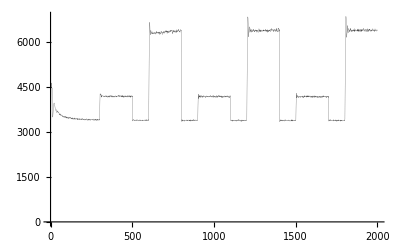

-Graphics-

```mathematica
goptimallm =  ListPlot[Take[optimallm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2031.19,3822.29,5243.69,6254.41,6911.94,7125.4,7162.41,7087.01,6950.77,6898.24,6832.01,6751.66,6565.23,6236.87,5980.69,5634.25,5229.15,4814.02,4566.02,4444.42,4415.38,4387.13,4347.44,4344.56,4346.51,4306.67,4333.67,4279.12,4319.68,4367.47,4400.59,4388.17,4398.05,4402.44,4445.19,4439.79,4435.84,4464.17,4405.01,4445.16,4475.94,4408.15,4400.03,4366.56,4321.24,4314.21,4241.59,4162.45,4139.99,4067.18,4079.2,4057.13,4012.19,4033.93,3958.62,3956.74,3900.71,3873.36,3898.13,3876.33,3904.48,3807.2,3848.46,3862.57,3813.22,3800.15,3774.01,3761.89,3776.93,3730.12,3720.32,3707.82,3666.62,3637.65,3630.8,3620.49,3644.28,3605.1,3618.78,3597.42,3613.38,3591.48,3608.04,3575.82,3604.72,3566.67,3592.57,3590.86,3553.64,3561.47,3588.29,3556.92,3553.71,3552.04,3572.64,3579.58,3570.81,3549.42,3545.42,3568.5,3497.63,3577.71,3560.31,3530.95,3525.74,3529.57,3517.71,3511.79,3537.04,3493.4,3564.04,3497.08,3529.06,3543.75,3518.57,3519.02,3517.35,3501.59,3488.84,3511.09,3509.2,3521.34,3482.,3518.22,3524.05,3492.94,3497.62,3499.88,3467.27,3501.34,3498.88,3502.69,3528.96,3501.32,3481.64,3482.32,3456.93,3512.98,3512.64,3486.13,3468.56,3500.14,3474.32,3489.04,3476.45,3461.14,3478.47,3485.44,3492.28,3475.84,3493.68,3453.49,3500.42,3489.03,3497.26,3468.37,3481.21,3478.2,3466.99,3468.89,3471.6,3498.58,3488.3,3488.31,3449.37,3468.22,3502.59,3476.9,3466.71,3532.4,3428.63,3454.73,3481.24,3464.91,3454.6,3508.01,3447.38,3473.07,3493.16,3474.49,3482.09,3492.88,3457.54,3454.72,3504.36,3486.21,3486.38,3450.43,3485.48,3475.77,3480.73,3502.13,3480.06,3467.64,3469.03,3484.24,3508.22,3500.22,3460.02,3494.01,3474.1,3512.93,3463.02,3505.76,3493.54,3484.77,3475.81,3494.92,3448.08,3498.26,3440.41,3471.68,3492.04,3456.45,3506.32,3488.18,3488.89,3467.33,3473.13,3460.97,3475.69,3479.3,3481.17,3433.19,3473.75,3471.77,3451.6,3449.83,3498.77,3479.04,3459.43,3482.86,3462.68,3479.25,3495.11,3459.82,3488.64,3440.55,3437.76,3454.4,3470.51,3458.77,3473.69,3451.9,3464.94,3453.45,3466.55,3496.08,3480.33,3455.49,3465.03,3463.97,3454.28,3447.01,3478.85,3477.46,3481.49,3484.87,3473.67,3464.86,3473.96,3454.66,3432.99,3480.59,3465.12,3470.54,3450.19,3484.03,3449.54,3462.94,3463.63,3471.39,3457.11,3463.28,3489.71,3488.07,3455.98,3457.83,3493.16,3440.34,3431.92,3462.33,3417.8,3465.12,3469.46,3449.16,3463.37,3463.13,3453.38,3451.31,3444.11,3448.17,3492.7,3459.49,3464.73,3464.51,3439.08,3476.67,3480.29,3457.37,3447.08,3437.54,3473.84,3440.19,3476.02,3458.32,3418.79,3465.76,3462.31,3413.91,3483.37,3446.99,3434.79,3460.53,3429.97,3453.03,3458.84,3443.51,3415.18,3443.75,3428.99,3461.05,3449.88,3470.77,3451.07,3461.81,3444.27,3423.79,3459.41,3428.75,3443.48,3426.7,3467.93,3451.29,3460.13,3456.58,3426.06,3445.7,3431.46,3452.05,3448.98,3434.03,3471.46,3469.88,3456.6,3427.61,3471.56,3452.98,3438.06,3437.65,3479.13,3461.63,3451.98,3450.1,3485.26,3466.8,3419.49,3441.83,3449.97,3446.66,3476.74,3467.64,3414.68,3436.15,3467.66,3460.53,3434.46,3460.39,3475.45,3493.43,3441.67,3460.97,3488.02,3464.64,3438.53,3457.02,3468.71,3444.39,3433.88,3449.56,3433.47,3423.97,3485.96,3433.72,3465.35,3464.43,3459.88,3484.21,3488.75,3477.72,3445.99,3434.39,3451.05,3460.17,3475.34,3444.38,3458.8,3426.07,3453.55,3478.48,3461.32,3431.38,3439.62,3457.62,3451.07,3448.27,3445.29,3461.64,3476.43,3464.51,3451.98,3416.46,3446.99,3442.54,3469.49,3441.31,3460.94,3416.36,3467.49,3447.,3473.99,3458.2,3435.01,3484.47,3441.88,3451.25,3468.56,3434.1,3445.63,3469.72,3484.3,3429.17,3456.53,3456.43,3462.38,3453.06,3403.31,3463.32,3472.27,3447.65,3468.61,3461.92,3439.46,3440.6,3433.25,3466.32,3451.94,3463.28,3459.36,3461.3,3434.26,3451.82,3441.87,3424.4,3462.85,3437.97,3418.94,3455.58,3446.72,3482.81,3443.4,3450.72,3481.01,3429.96,3450.97,3479.89,3454.13,3457.15,3455.85,3473.37,3457.04,3432.48,3450.88,3456.68,3474.88,3469.02,3495.54,3450.17,3459.41,3440.4,3454.41,3423.06,3411.35,3459.43,3470.84,3436.88,3432.17,3429.53,3426.09,3452.7,3453.92,3444.99,3474.22,3479.62,3446.88,3432.92,3437.18,3452.48,3432.21,3436.51,3468.93,3471.53,3423.85,3436.64,3455.14,3411.68,3459.83,3451.34,3434.12,3426.72,3450.53,3448.76,3450.16,3452.15,3448.95,3452.43,3459.04,3437.14,3444.57,3457.19,3492.23,3459.46,3429.16,3452.57,3494.19,3435.,3428.45,3435.8,3428.67,3449.62,3462.21,3448.91,3434.99,3427.94,3439.41,3460.25,3466.05,3417.75,3422.27,3458.81,3437.85,3446.3,3426.79,3497.18,3446.74,3438.32,3458.93,3440.96,3454.78,3465.74,3451.5,3467.96,3461.01,3439.48,3450.64,3471.67,3442.89,3441.7,3434.03,3429.6,3478.81,3443.38,3436.41,3460.76,3438.4,3420.73,3445.2,3458.68,3441.91,3459.52,3468.64,3431.12,3464.18,3453.68,3442.15,3444.96,3457.43,3432.59,3432.86,3426.3,3426.64,3437.12,3485.75,3467.72,3434.75,3453.35,3447.42,3470.97,3431.93,3431.04,3456.69,3455.43,3479.03,3456.71,3440.55,3437.64,3444.01,3471.49,3424.24,3420.3,3414.68,3421.97,3450.17,3485.24,3448.48,3453.45,3450.14,3433.78,3451.12,3434.25,3424.88,3455.14,3428.39,3431.22,3472.07,3469.73,3458.35,3445.45,3474.33,3463.31,3482.29,3430.69,3433.17,3456.17,3450.19,3452.75,3437.41,3439.02,3477.6,3440.96,3440.38,3443.86,3444.02,3445.99,3497.93,3458.99,3447.18,3438.41,3468.61,3451.,3433.63,3464.01,3465.9,3431.3,3426.54,3469.49,3469.91,3421.58,3433.66,3472.94,3469.88,3422.61,3488.57,3451.14,3440.8,3431.83,3451.56,3454.29,3437.17,3460.92,3415.07,3440.08,3449.45,3461.77,3466.06,3444.19,3423.31,3448.52,3422.2,3449.37,3438.06,3434.15,3469.24,3433.56,3422.71,3443.37,3426.18,3463.64,3452.46,3446.74,3407.79,3445.37,3436.51,3462.26,3414.08,3455.14,3471.14,3432.46,3439.65,3451.35,3437.98,3460.98,3453.17,3418.17,3445.69,3437.47,3483.22,3480.4,3424.14,3456.52,3441.27,3444.26,3439.37,3439.4,3438.03,3452.72,3447.09,3453.72,3457.09,3446.79,3450.55,3425.49,3446.41,3446.37,3446.3,3456.09,3476.64,3448.83,3443.16,3462.43,3438.45,3422.91,3457.55,3458.11,3441.31,3456.85,3454.57,3439.23,3412.26,3426.44,3440.4,3421.73,3450.44,3432.86,3409.13,3425.97,3414.03,3456.6,3453.02,3434.04,3451.4,3431.97,3449.51,3425.38,3434.11,3475.02,3451.56,3449.87,3441.05,3459.95,3448.62,3463.87,3445.78,3453.77,3422.8,3446.83,3438.75,3439.43,3446.79,3442.16,3423.8,3421.41,3444.65,3445.9,3444.04,3450.25,3458.48,3441.29,3443.59,3427.88,3487.7,3452.29,3453.41,3466.9,3451.44,3428.05,3426.45,3440.43,3423.25,3468.95,3458.74,3462.87,3448.14,3453.04,3443.16,3438.22,3447.75,3437.6,3433.33,3444.36,3466.5,3432.81,3465.6,3442.46,3438.37,3473.32,3435.4,3443.65,3474.68,3457.72,3447.24,3463.8,3438.03,3443.06,3435.71,3468.7,3448.42,3439.46,3420.63,3428.97,3426.11,3462.01,3439.45,3431.36,3425.39,3447.73,3505.91,3416.63,3470.27,3495.99,3430.63,3428.72,3414.02,3457.88,3445.44,3433.89,3479.53,3437.46,3433.76,3429.15,3420.84,3459.76,3465.59,3470.14,3467.55,3434.37,3439.36,3458.21,3439.68,3458.2,3456.71,3468.06,3425.75,3473.67,3449.86,3419.41,3455.31,3446.19,3444.43,3457.26,3453.72,3446.31,3438.46,3431.45,3459.25,3442.55,3401.71,3441.49,3447.38,3418.27,3415.96,3463.17,3452.6,3437.43,3454.78,3436.63,3458.14,3452.3,3451.38,3431.15,3442.28,3432.37,3459.26,3410.9,3459.4,3454.32,3454.32,3418.23,3451.66,3458.24,3423.99,3467.67,3456.62,3448.28,3451.,3455.52,3443.23,3447.1,3441.37,3431.21,3448.03,3429.47,3471.25,3438.61,3428.08,3442.03,3452.45,3434.21,3435.03,3432.71,3460.13,3433.23,3425.78,3446.59,3453.11,3464.58,3474.95,3433.5,3430.09,3422.17,3475.89,3412.33,3474.82,3460.86,3452.25,3447.36,3472.22,3458.22,3476.36,3457.77,3419.68,3446.24,3450.82,3431.15,3448.06,3418.1,3439.01,3428.76,3453.16,3459.47,3421.88,3433.12,3475.27,3453.54,3454.42,3429.9,3429.13,3449.02,3438.9,3471.44,3432.68,3446.11,3425.79,3449.45,3453.76,3409.17,3474.52,3437.43,3420.65,3439.7,3420.1,3412.85,3431.79,3431.21,3418.09,3464.66,3438.83,3431.13,3438.5,3424.42,3459.84,3425.23,3433.53,3439.37,3438.47,3473.67,3430.83,3427.57,3423.3,3473.01,3461.68,3424.42,3441.17,3469.24,3455.08,3458.85,3429.44,3441.37,3420.38,3441.42,3433.86,3435.3,3408.91,3451.17,3434.7,3428.89,3460.16,3445.01,3451.55,3474.8,3430.57,3442.47,3441.78,3450.86,3411.62,3441.78,3446.52,3421.12,3473.66,3439.6,3431.28,3456.57,3443.49,3452.16,3445.2,3452.09,3463.78,3443.08,3463.36,3427.52,3441.96,3445.85,3424.78,3438.46,3469.75,3438.62,3450.68,3450.07,3463.18,3458.76,3446.7,3441.08,3436.49,3448.54,3433.44,3456.56,3413.32,3450.25,3465.21,3434.5,3440.71,3465.27,3468.11,3458.14,3453.13,3450.47,3452.65,3429.97,3443.61,3481.86,3453.21,3461.89,3466.6,3455.8,3421.42,3457.7,3449.72,3453.37,3438.49,3452.41,3446.31,3457.39,3439.47,3413.6,3443.24,3455.62,3446.14,3451.71,3413.28,3441.62,3462.32,3452.47,3457.14,3454.2,3431.76,3449.07,3461.25,3454.17,3460.9,3434.26,3473.31,3438.35,3447.54,3448.39,3469.05,3425.58,3453.03,3414.68,3457.19,3477.77,3448.79,3430.61,3424.52,3437.37,3442.25,3465.6,3455.48,3431.69,3425.08,3432.89,3446.05,3427.76,3441.48,3455.16,3450.01,3431.15,3429.27,3442.97,3445.24,3449.31,3438.57,3445.93,3461.04,3453.46,3450.73,3454.26,3425.55,3449.56,3475.15,3459.13,3420.02,3469.91,3405.1,3419.18,3451.43,3450.16,3456.01,3445.04,3465.59,3423.05,3462.77,3437.19,3427.4,3474.08,3479.09,3437.3,3449.27,3445.09,3436.02,3461.02,3465.71,3458.41,3427.44,3443.16,3433.3,3414.89,3450.77,3434.66,3423.94,3446.37,3432.44,3482.78,3449.52,3422.72,3489.91,3464.65,3425.38,3454.92,3442.05,3425.53,3444.59,3436.57,3441.86,3451.18,3439.78,3473.26,3439.13,3451.,3449.43,3460.81,3429.91,3458.76,3448.8,3415.11,3430.2,3473.06,3426.4,3424.88,3436.13,3458.78,3443.32,3440.6,3435.56,3445.23,3442.61,3449.86,3429.48,3448.51,3440.21,3446.32,3437.62,3456.14,3432.33,3431.49,3450.21,3465.88,3385.55,3437.28,3474.46,3440.48,3447.76,3443.77,3450.93,3446.,3470.49,3430.17,3400.28,3429.71,3451.74,3448.66,3426.15,3464.15,3447.41,3461.01,3448.75,3441.83,3460.22,3457.63,3423.06,3444.49,3460.8,3432.94,3432.57,3447.87,3443.18,3444.94,3470.43,3457.,3459.94,3426.74,3436.33,3477.23,3455.39,3422.67,3452.28,3454.16,3430.85,3434.41,3431.11,3407.35,3455.18,3432.54,3473.67,3436.9,3445.5,3437.87,3440.29,3435.27,3442.53,3447.2,3453.67,3438.6,3412.11,3429.07,3445.72,3462.48,3416.79,3457.55,3453.45,3453.18,3427.13,3453.12,3443.43,3434.05,3451.82,3459.49,3434.47,3443.02,3443.43,3476.05,3474.5,3458.59,3456.17,3452.44,3428.65,3428.74,3470.77,3465.78,3431.74,3443.89,3437.05,3472.75,3416.49,3416.46,3435.29,3413.09,3410.79,3456.72,3462.2,3454.78,3424.57,3435.35,3438.33,3425.34,3447.32,3435.52,3444.05,3435.62,3463.5,3454.84,3434.75,3443.48,3444.1,3430.97,3455.59,3437.79,3457.52,3438.98,3448.85,3456.91,3472.7,3444.51,3432.2,3433.18,3471.67,3432.44,3438.2,3411.5,3453.31,3415.92,3429.53,3464.88,3455.97,3468.08,3437.16,3416.89,3440.86,3461.82,3441.96,3458.28,3432.75,3478.34,3423.62,3425.61,3450.94,3424.03,3421.85,3453.83,3447.6,3412.4,3441.47,3445.02,3436.21,3426.77,3497.38,3432.88,3402.17,3440.99,3427.52,3440.56,3448.85,3442.16,3417.24,3469.52,3417.97,3463.98,3428.99,3444.84,3439.62,3422.16,3433.74,3450.8,3447.38,3411.42,3455.,3459.7,3449.22,3448.53,3419.59,3422.99,3447.05,3431.05,3450.32,3447.09,3439.41,3478.82,3462.07,3427.12,3441.59,3464.87,3441.52,3456.96,3442.42,3414.78,3467.08,3458.14,3441.03,3447.57,3430.98,3441.04,3471.47,3445.48,3435.39,3409.76,3468.99,3433.13,3459.55,3434.86,3447.31,3455.19,3447.8,3460.45,3413.17,3428.63,3465.94,3465.6,3442.73,3459.19,3447.15,3444.74,3449.17,3437.89,3430.74,3446.17,3438.3,3449.08,3448.49,3444.26,3444.6,3435.52,3437.45,3459.49,3447.76,3466.84,3453.06,3435.73,3465.2,3445.88,3432.02,3458.35,3458.7,3413.2,3459.49,3435.86,3460.82,3428.17,3440.79,3431.22,3465.93,3455.41,3471.44,3474.62,3458.4,3438.94,3441.06,3463.74,3419.92,3445.95,3439.34,3454.88,3455.28,3423.64,3442.34,3446.42,3431.21,3460.,3435.75,3433.76,3418.32,3432.55,3449.94,3460.64,3467.7,3465.75,3437.06,3468.96,3451.53,3437.,3469.88,3429.18,3427.02,3421.44,3414.89,3457.1,3433.54,3438.63,3433.16,3407.23,3440.66,3425.97,3451.86,3443.64,3395.75,3465.57,3454.33,3440.8,3460.72,3445.95,3447.08,3426.49,3458.48,3424.27,3441.82,3443.61,3432.98,3468.12,3445.1,3436.76,3451.01,3460.67,3458.88,3434.47,3437.87,3465.71,3436.78,3461.87,3432.7,3448.76,3420.63,3430.77,3459.18,3474.4,3411.8,3425.37,3442.83,3452.45,3435.61,3441.72,3465.99,3443.31,3483.7,3448.42,3433.77,3433.03,3448.96,3436.78,3425.71,3459.21,3442.5,3460.03,3443.23,3469.57,3470.95,3430.52,3427.05,3448.82,3442.09,3442.7,3458.64,3446.56,3432.58,3440.56,3414.25,3438.91,3448.27,3440.23,3438.18,3455.13,3454.22,3439.18,3455.94,3431.49,3451.21,3457.3,3441.43,3449.61,3469.96,3484.42,3472.12,3435.64,3467.5,3436.95,3433.81,3462.66,3455.56,3451.67,3464.31,3444.81,3429.18,3464.99,3431.11,3422.65,3415.36,3430.98,3433.46,3410.73,3442.32,3440.79,3424.01,3411.77,3428.67,3462.06,3445.19,3439.09,3440.71,3450.04,3444.3,3470.97,3438.39,3455.61,3456.52,3463.24,3424.09,3467.82,3431.2,3441.59,3453.19,3465.17,3425.14,3458.47,3450.32,3434.87,3453.83,3422.7,3436.37,3448.97,3445.76,3401.91,3442.12,3458.21,3424.79,3446.35,3448.24,3447.9,3420.93,3434.47,3430.45,3461.8,3445.45,3448.65,3431.81,3455.7,3452.33,3428.54,3449.21,3456.64,3447.78,3431.7,3432.8,3455.39,3452.01,3427.97,3445.75,3450.14,3411.54,3438.07,3448.01,3444.44,3447.54,3453.01,3454.33,3450.08,3403.02,3418.25,3425.36,3415.79,3441.58,3445.62,3459.42,3463.41,3452.27,3458.26,3448.66,3439.18,3447.72,3426.86,3451.15,3467.93,3462.02,3451.82,3426.27,3444.26,3465.05,3439.96,3426.69,3432.97,3448.21,3489.79,3442.33,3409.47,3445.56,3437.91,3453.67,3449.27,3444.88,3438.99,3436.96,3441.29,3442.86,3446.52,3436.27,3453.32,3448.04,3468.32,3483.92,3459.78,3426.48,3459.03,3442.32,3455.35,3434.3,3468.12,3427.19,3434.91,3472.53,3469.74,3436.89,3436.47,3449.27,3445.6,3439.7,3457.89,3448.11,3438.66,3452.37,3471.1,3450.66,3419.76,3426.23,3448.51,3449.12,3414.07,3429.02,3444.21,3434.76,3430.25,3405.86,3449.84,3436.81,3458.12,3443.01,3458.85,3439.84,3416.79,3425.02,3452.08,3422.92,3443.96,3423.72,3449.61,3441.78,3431.61,3450.15,3466.6,3480.35,3458.63,3460.31,3479.81,3462.7,3433.52,3441.79,3420.73,3452.74,3465.83,3444.21,3443.76,3444.76,3456.59,3428.26,3454.98,3422.82,3436.84,3400.34,3443.,3428.29,3416.78,3431.56,3432.94,3434.51,3467.58,3450.89,3413.32,3453.86,3445.9,3445.77,3444.93,3398.53,3503.64,3444.03,3433.91,3433.84,3436.63,3421.99,3461.99,3458.71,3429.26,3442.8,3440.89,3435.68,3438.83,3467.58,3450.7,3418.16,3450.27,3435.99,3420.18,3427.33,3460.56,3451.29,3440.93,3435.01,3433.19,3468.06,3436.85,3414.44,3429.38,3456.42,3473.43,3450.52,3447.46,3456.8,3441.01,3441.28,3427.94,3446.34,3438.79,3430.95,3454.3,3402.78,3432.42,3420.73,3442.58,3431.34,3413.55,3426.88,3441.91,3465.34,3442.1,3466.47,3443.16,3431.18,3455.91,3428.41,3426.12,3438.68,3429.49,3425.9,3443.44,3455.02,3436.46,3461.57,3424.01,3438.36,3419.32,3418.88,3445.99,3423.25,3419.73,3426.55,3442.16,3431.39,3447.33,3453.62,3421.,3446.43,3413.17,3414.88,3442.36,3463.76,3416.1,3433.92,3428.9,3427.37,3444.58,3433.09,3450.42,3423.39,3428.43,3470.05,3437.6,3461.34,3446.29,3421.29,3461.6,3424.51,3464.16,3463.03,3436.02,3449.54,3437.59,3445.41,3441.12,3438.47,3418.69,3419.62,3404.61,3439.45,3445.35,3446.59,3458.33,3435.69,3464.66,3426.68,3414.29,3439.98,3447.8,3417.96,3439.77,3435.63,3444.65,3434.42,3449.44,3399.55,3430.06,3450.14,3439.6,3440.94,3434.94,3457.,3424.72,3437.6,3459.4,3471.36,3450.63,3429.55,3439.54,3458.79,3407.53,3441.33,3426.,3419.5,3436.71,3448.1,3452.27,3461.52,3444.35,3445.18,3434.98,3449.53,3427.16,3438.47,3449.48,3451.32,3441.59,3444.39,3438.29,3452.46,3425.4,3455.37,3434.65,3414.49,3435.,3468.22,3441.08,3433.68,3428.15,3453.7,3424.,3431.7,3422.92,3440.14,3440.61,3449.87,3452.97,3425.08,3397.8,3449.77,3449.19,3427.19,3424.26,3395.58,3444.81,3441.21,3426.36,3438.65,3436.23,3471.35,3454.74,3441.89,3429.7,3460.27,3446.63,3470.49,3452.89,3467.89,3407.43,3420.58,3446.33,3443.26,3450.38,3431.78,3421.32,3434.02,3467.65,3437.35,3418.64,3462.38,3444.49,3419.06,3434.98,3438.73,3416.47,3453.57,3456.75,3443.41,3462.49,3448.89,3435.65,3451.05,3420.25,3443.87,3419.68,3442.01,3450.72,3430.36,3406.75,3430.56,3425.74,3458.4,3434.59,3444.11,3428.64,3474.31,3433.68,3435.67,3416.52,3426.97,3450.4,3437.68,3458.23},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gcomplexxPm = ListPlot[Take[complexxPm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Red, Thickness[0.001]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2029.79, 3187.93, 3637.22, 3717.18, 3903.2, 3969.98, 4152.76, 4243.51, 4283.78, 4421.35, 4408.99, 4371.5, 4381.02, 4291.73, 4209.98, 4230.38, « 19 », 4368.88, 4409.05, 4406.54, 4345.37, 4338.12, 4289.72, 4346.57, 4352.52, 4332.86, 4361.3, 4342.98, 4344.45, 4323.79, 4330.33, 4251.72, « 1950 »}, « 2 », PlotStyle → {« 1 »}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.79,3187.93,3637.22,3717.18,3903.2,3969.98,4152.76,4243.51,4283.78,4421.35,4408.99,4371.5,4381.02,4291.73,4209.98,4230.38,4245.99,4251.14,4340.38,4416.94,4399.79,4471.02,4388.36,4425.93,4357.,4369.6,4348.51,4332.29,4348.9,4305.36,4323.87,4320.58,4310.75,4278.28,4310.51,4368.88,4409.05,4406.54,4345.37,4338.12,4289.72,4346.57,4352.52,4332.86,4361.3,4342.98,4344.45,4323.79,4330.33,4251.72,4304.44,4209.63,4236.4,4364.25,4341.83,4380.84,4361.91,4374.47,4348.57,4265.18,4359.44,4353.08,4413.01,4359.02,4323.61,4264.93,4276.8,4270.79,4353.86,4372.68,4373.24,4394.28,4311.86,4253.88,4184.01,4251.76,4282.86,4255.16,4331.48,4320.34,4334.94,4295.89,4283.59,4279.53,4310.66,4318.83,4353.23,4302.96,4312.44,4329.21,4313.92,4356.,4281.84,4309.59,4249.92,4215.74,4286.77,4288.64,4233.25,4249.6,4246.99,4336.33,4418.81,4373.52,4345.35,4348.33,4209.38,4248.43,4364.14,4333.4,4284.24,4327.12,4338.69,4354.28,4339.24,4351.22,4355.95,4316.02,4330.09,4403.57,4366.09,4414.33,4291.42,4345.62,4289.75,4357.85,4382.04,4234.26,4198.35,4171.53,4192.57,4241.81,4234.71,4235.01,4293.26,4311.1,4177.6,4211.51,4230.7,4342.2,4330.04,4308.34,4260.64,4311.13,4381.8,4378.76,4389.85,4309.47,4305.58,4316.43,4250.72,4291.55,4286.3,4304.9,4290.68,4340.19,4316.13,4274.7,4347.19,4418.05,4427.37,4428.19,4379.09,4307.15,4314.05,4240.79,4321.19,4413.74,4364.44,4297.84,4242.14,4286.95,4377.45,4320.56,4339.58,4389.03,4423.64,4355.67,4379.58,4314.89,4307.01,4365.48,4375.59,4324.83,4274.06,4265.56,4278.62,4351.86,4305.78,4308.1,4274.08,4272.13,4284.84,4309.06,4361.46,4302.61,4363.79,4322.01,4327.84,4308.52,4361.85,4382.48,4376.5,4312.58,4378.6,4392.52,4360.1,4349.17,4298.74,4402.65,4306.97,4295.17,4286.27,4307.67,4301.25,4288.39,4341.17,4340.95,4326.05,4337.78,4328.15,4385.98,4373.,4333.38,4336.64,4372.5,4375.76,4354.12,4354.91,4334.32,4362.23,4375.62,4380.93,4373.82,4315.87,4298.55,4335.74,4375.3,4392.97,4321.01,4354.05,4327.92,4328.69,4327.15,4315.64,4328.55,4308.64,4311.67,4357.67,4303.8,4244.13,4235.64,4213.36,4339.18,4342.7,4322.12,4341.07,4364.1,4337.76,4369.54,4340.16,4381.13,4446.16,4324.66,4286.27,4261.3,4304.82,4272.93,4402.19,4379.1,4286.23,4298.02,4283.14,4260.38,4323.24,4319.5,4254.81,4343.76,4281.9,4252.92,4272.45,4313.91,4330.43,4331.89,4378.72,4420.73,4437.85,4486.73,4523.05,4479.39,4400.04,4388.16,4376.32,4352.25,4330.15,4321.11,4355.87,4405.45,4411.41,4416.76,4353.09,4344.9,4249.14,4324.23,4295.28,4373.68,4335.16,4344.42,4375.78,4311.9,4364.29,4347.65,4323.3,4300.37,4373.4,4305.72,4282.67,4265.7,4305.19,4292.33,4333.01,4386.56,4439.77,4458.89,4419.08,4368.39,4305.99,4329.41,4275.2,4312.56,4391.33,4364.72,4365.15,4313.39,4299.11,4256.5,4244.89,4299.69,4332.5,4344.64,4311.96,4355.29,4319.74,4329.2,4305.6,4391.7,4398.63,4402.35,4363.65,4357.76,4353.72,4372.15,4395.77,4301.39,4340.02,4263.18,4243.82,4365.5,4339.15,4297.76,4251.38,4312.49,4335.7,4375.33,4379.59,4330.72,4334.16,4379.36,4355.83,4400.52,4388.98,4393.38,4377.59,4375.35,4381.72,4294.85,4397.24,4410.57,4275.46,4289.49,4278.9,4329.32,4309.72,4311.62,4326.61,4204.38,4228.45,4264.14,4289.21,4315.59,4318.97,4406.95,4390.37,4325.98,4455.67,4370.56,4352.42,4313.51,4227.13,4323.7,4296.11,4275.88,4391.98,4393.32,4395.35,4356.34,4264.13,4335.74,4284.52,4319.41,4385.5,4379.12,4413.5,4346.31,4360.37,4406.48,4306.67,4297.64,4394.57,4261.4,4372.65,4330.8,4366.58,4324.64,4326.95,4313.68,4310.52,4382.22,4296.96,4304.9,4321.79,4225.05,4307.97,4333.13,4375.52,4407.71,4394.29,4419.97,4362.52,4373.61,4249.14,4331.3,4362.57,4320.17,4328.31,4369.63,4365.9,4379.41,4310.86,4249.36,4336.05,4379.17,4330.55,4318.6,4288.21,4263.32,4357.7,4272.49,4344.5,4297.28,4288.15,4241.78,4382.34,4387.72,4306.65,4365.5,4311.38,4240.32,4250.4,4307.5,4326.93,4231.15,4239.75,4295.49,4342.16,4341.27,4305.14,4332.93,4312.22,4314.31,4282.66,4332.13,4359.15,4304.53,4301.64,4310.33,4303.59,4328.21,4327.87,4299.4,4351.78,4305.51,4395.71,4420.07,4382.91,4318.58,4280.21,4356.99,4415.7,4439.25,4288.95,4320.6,4266.1,4284.7,4288.03,4262.06,4254.67,4322.35,4386.72,4344.66,4378.48,4416.55,4315.08,4371.58,4336.12,4409.59,4369.71,4367.07,4243.56,4259.36,4242.13,4256.95,4303.09,4342.74,4302.74,4314.95,4319.53,4414.54,4361.16,4399.57,4378.69,4344.77,4287.99,4249.93,4294.96,4279.07,4324.51,4225.29,4288.,4372.77,4343.18,4357.56,4333.88,4351.53,4286.98,4271.99,4339.08,4294.17,4353.67,4328.85,4352.02,4321.56,4287.94,4353.05,4360.93,4320.61,4384.94,4367.15,4357.57,4350.88,4327.64,4331.5,4317.73,4315.87,4327.44,4345.3,4320.17,4327.06,4326.81,4306.24,4288.31,4269.34,4333.38,4272.63,4301.25,4276.69,4380.85,4383.53,4403.42,4380.38,4391.92,4323.36,4337.2,4357.25,4338.47,4315.88,4257.04,4269.17,4285.92,4317.89,4335.62,4282.39,4318.05,4341.26,4296.34,4315.94,4396.72,4277.79,4304.34,4284.1,4267.89,4284.87,4332.47,4294.41,4334.8,4449.54,4375.94,4312.53,4393.63,4314.84,4379.39,4367.19,4304.66,4289.05,4257.79,4241.11,4315.91,4365.65,4346.35,4346.58,4298.33,4433.21,4373.14,4268.92,4274.57,4345.03,4344.63,4326.07,4345.33,4327.65,4302.43,4307.12,4296.58,4294.38,4377.39,4325.15,4325.53,4414.56,4362.85,4410.39,4426.56,4330.33,4333.68,4273.39,4281.56,4308.61,4351.88,4207.93,4226.39,4256.63,4273.74,4334.,4323.03,4356.13,4337.18,4401.32,4281.07,4281.09,4238.53,4298.62,4389.85,4413.54,4354.34,4342.97,4318.7,4333.26,4317.03,4332.04,4250.85,4244.95,4283.61,4297.04,4363.66,4325.54,4354.47,4429.23,4416.39,4328.41,4321.54,4304.,4305.63,4196.29,4265.61,4202.18,4179.01,4270.03,4339.79,4384.67,4356.06,4270.19,4348.67,4431.03,4471.41,4417.47,4386.06,4378.33,4336.53,4341.48,4266.61,4255.15,4269.46,4219.77,4236.53,4221.84,4313.56,4329.76,4285.93,4267.97,4334.89,4390.69,4420.56,4383.84,4436.72,4341.07,4276.73,4253.78,4181.7,4279.27,4279.74,4241.85,4288.46,4280.52,4377.29,4387.6,4359.4,4384.04,4375.16,4396.82,4360.43,4335.14,4337.97,4392.21,4450.6,4411.41,4453.77,4401.19,4412.53,4453.64,4380.25,4322.47,4328.26,4302.35,4270.48,4334.39,4334.67,4324.52,4383.01,4428.5,4426.51,4421.2,4352.56,4294.97,4403.48,4388.12,4419.25,4422.64,4326.23,4302.49,4269.11,4254.69,4356.93,4367.98,4421.41,4329.56,4337.37,4309.37,4313.63,4316.45,4401.23,4387.98,4416.49,4485.65,4340.59,4315.57,4409.38,4379.28,4334.07,4354.31,4303.93,4365.05,4265.44,4374.29,4354.65,4319.23,4362.4,4420.41,4299.08,4319.14,4273.6,4335.82,4299.95,4223.72,4320.49,4278.15,4287.84,4285.54,4361.88,4313.35,4361.98,4263.81,4309.67,4345.78,4365.67,4327.72,4298.7,4307.81,4299.56,4329.25,4318.44,4337.18,4294.1,4282.14,4348.62,4372.22,4377.62,4390.25,4299.04,4348.22,4322.34,4353.51,4359.5,4346.58,4273.35,4298.92,4340.12,4310.81,4372.64,4339.46,4328.23,4329.53,4270.68,4328.58,4353.25,4282.96,4351.94,4330.62,4300.63,4298.23,4234.29,4345.64,4432.44,4392.9,4318.01,4262.78,4252.22,4295.7,4300.3,4311.12,4219.27,4264.86,4238.4,4218.96,4281.27,4255.13,4260.59,4306.17,4315.39,4351.15,4322.64,4344.43,4408.67,4383.9,4441.09,4494.26,4407.25,4273.85,4313.68,4297.13,4372.64,4379.03,4320.89,4345.5,4362.26,4279.98,4312.05,4306.3,4268.33,4263.18,4170.73,4311.52,4309.43,4338.47,4358.05,4415.73,4386.53,4281.26,4299.4,4359.46,4388.54,4378.15,4358.09,4347.82,4363.53,4362.12,4282.28,4254.96,4268.51,4265.44,4308.89,4336.68,4348.47,4250.52,4324.71,4328.21,4353.39,4313.31,4296.47,4315.06,4244.65,4332.74,4441.75,4454.37,4438.67,4431.38,4391.33,4370.68,4326.61,4285.42,4300.96,4292.34,4307.67,4370.6,4366.7,4401.99,4418.85,4397.28,4302.98,4297.78,4334.95,4358.1,4381.5,4347.24,4285.73,4305.17,4255.93,4274.12,4316.35,4425.4,4342.83,4273.68,4258.35,4260.92,4250.39,4200.42,4326.08,4384.54,4419.33,4323.66,4297.49,4250.8,4236.62,4321.54,4357.51,4292.49,4296.11,4283.45,4313.39,4381.81,4360.02,4268.48,4310.33,4277.99,4353.53,4392.16,4346.49,4348.34,4426.85,4396.07,4337.52,4316.42,4334.66,4294.03,4321.06,4220.44,4261.64,4270.4,4286.4,4286.78,4264.26,4252.74,4234.3,4299.99,4342.6,4378.1,4453.38,4478.15,4479.32,4438.13,4352.44,4355.36,4326.68,4328.31,4307.19,4253.94,4308.29,4376.11,4358.52,4313.97,4324.82,4342.27,4363.62,4318.58,4310.1,4283.98,4271.77,4297.34,4395.65,4242.56,4248.15,4278.82,4297.32,4308.66,4327.81,4296.71,4276.28,4264.42,4289.17,4302.23,4370.39,4359.4,4404.94,4432.44,4389.87,4414.78,4349.58,4374.85,4316.7,4213.03,4239.45,4256.77,4316.32,4303.57,4266.96,4330.33,4299.48,4318.28,4391.29,4333.41,4350.93,4313.91,4288.7,4282.11,4290.32,4376.97,4380.46,4375.31,4340.82,4400.67,4316.33,4204.56,4246.92,4255.48,4274.26,4322.24,4325.87,4385.53,4359.33,4263.18,4370.1,4384.59,4299.62,4339.53,4343.15,4341.7,4320.45,4280.5,4249.21,4346.24,4346.34,4376.46,4374.33,4386.98,4328.96,4347.81,4262.96,4234.08,4252.06,4225.2,4263.22,4310.81,4381.59,4371.93,4420.59,4499.77,4450.05,4414.05,4363.15,4314.71,4361.04,4304.7,4319.1,4226.09,4252.02,4233.49,4334.7,4304.3,4349.85,4380.97,4351.51,4372.77,4285.34,4237.17,4282.27,4231.8,4273.07,4334.89,4346.56,4306.85,4308.53,4265.26,4343.03,4288.01,4279.,4267.72,4302.39,4347.52,4365.67,4300.86,4379.89,4327.12,4353.47,4369.3,4309.59,4329.44,4316.93,4328.92,4306.42,4306.12,4321.85,4341.77,4339.2,4273.28,4288.71,4334.07,4347.21,4358.12,4330.2,4264.02,4346.71,4354.46,4285.63,4253.43,4334.58,4296.31,4212.31,4269.71,4278.89,4302.42,4323.93,4346.11,4315.9,4360.92,4330.95,4411.24,4384.81,4321.64,4304.3,4370.22,4425.34,4424.66,4439.51,4405.46,4330.48,4330.32,4279.15,4313.04,4252.99,4287.65,4283.37,4327.74,4302.44,4286.23,4309.,4399.08,4462.61,4423.28,4401.7,4361.35,4381.28,4380.69,4366.93,4342.34,4323.27,4308.95,4338.85,4348.21,4369.43,4348.06,4255.41,4361.82,4252.81,4314.08,4333.68,4350.34,4388.04,4411.,4386.22,4430.41,4364.54,4339.61,4406.63,4336.62,4435.79,4408.3,4341.38,4344.1,4255.16,4331.5,4294.91,4368.97,4338.45,4439.74,4423.6,4298.07,4254.15,4238.4,4223.87,4214.08,4249.39,4252.89,4348.,4299.08,4358.95,4313.04,4306.1,4276.36,4254.72,4290.88,4334.47,4376.56,4414.68,4438.13,4453.98,4402.95,4482.67,4436.22,4446.71,4369.81,4289.95,4216.17,4212.43,4191.57,4152.93,4201.16,4303.92,4365.62,4410.51,4343.46,4354.01,4409.85,4382.24,4338.13,4284.62,4286.64,4262.61,4286.9,4255.77,4304.16,4251.28,4209.62,4276.06,4274.16,4267.86,4220.7,4242.7,4301.12,4363.64,4399.92,4354.95,4386.5,4364.28,4277.94,4354.65,4324.63,4369.17,4379.47,4299.47,4316.05,4306.28,4369.47,4405.36,4370.9,4308.95,4377.48,4320.73,4353.04,4362.38,4275.18,4366.38,4356.01,4340.45,4295.91,4303.58,4194.48,4226.28,4299.54,4268.28,4244.1,4274.29,4323.23,4402.6,4471.99,4473.92,4358.23,4306.59,4300.95,4290.64,4295.96,4363.03,4366.31,4392.27,4381.09,4407.61,4377.93,4334.07,4325.28,4281.42,4321.26,4301.89,4332.03,4381.1,4315.72,4333.97,4283.22,4273.87,4325.79,4329.7,4297.03,4267.78,4313.56,4279.8,4245.21,4363.92,4392.76,4386.32,4323.67,4299.64,4240.02,4288.77,4222.64,4302.5,4295.87,4314.23,4320.21,4371.29,4359.42,4281.61,4363.5,4341.99,4297.18,4277.49,4348.5,4345.43,4310.21,4369.66,4356.47,4339.05,4368.72,4395.93,4361.57,4326.64,4376.18,4353.36,4417.33,4371.21,4222.49,4237.77,4313.68,4340.35,4286.22,4315.94,4345.73,4325.41,4308.54,4408.22,4408.3,4368.73,4330.24,4249.96,4256.01,4231.94,4236.3,4287.14,4347.39,4363.4,4435.94,4439.3,4492.05,4453.29,4400.2,4361.91,4321.8,4311.36,4225.3,4261.2,4304.69,4371.97,4378.39,4310.95,4349.16,4371.73,4377.22,4336.17,4302.69,4238.63,4306.51,4273.01,4261.26,4211.84,4239.02,4383.89,4422.74,4358.76,4307.37,4396.79,4453.49,4411.15,4414.19,4313.86,4254.36,4290.99,4235.57,4278.32,4293.24,4314.75,4302.88,4333.79,4298.45,4264.22,4341.73,4270.8,4312.53,4348.27,4380.56,4347.21,4384.11,4362.08,4379.35,4362.21,4339.05,4241.39,4212.05,4224.22,4277.34,4270.34,4292.57,4377.86,4319.63,4310.88,4294.23,4307.52,4259.96,4264.63,4235.63,4257.17,4284.66,4318.24,4349.37,4425.9,4367.34,4426.93,4386.7,4323.64,4391.86,4429.37,4346.41,4312.63,4300.38,4302.63,4288.12,4289.18,4334.62,4407.58,4431.5,4435.9,4355.79,4310.87,4306.73,4286.82,4321.85,4232.5,4270.23,4267.53,4288.77,4314.94,4293.44,4269.17,4339.68,4363.63,4319.46,4345.98,4354.49,4392.99,4380.98,4284.93,4229.07,4283.3,4252.93,4309.83,4353.01,4326.48,4383.17,4370.78,4348.33,4238.26,4251.09,4266.26,4296.51,4439.83,4404.4,4390.83,4341.38,4342.61,4300.76,4301.72,4292.34,4265.72,4314.05,4253.32,4191.31,4267.19,4337.51,4335.04,4312.2,4345.75,4355.9,4342.2,4333.12,4335.25,4372.64,4409.57,4466.69,4497.31,4388.1,4316.95,4330.49,4338.04,4288.36,4269.45,4272.42,4301.43,4267.4,4322.26,4397.87,4349.48,4371.08,4351.32,4386.13,4409.89,4304.89,4275.67,4270.71,4346.19,4317.17,4310.49,4283.77,4208.25,4211.98,4198.29,4214.41,4287.45,4351.13,4325.92,4305.,4303.41,4358.61,4410.45,4358.58,4333.11,4373.96,4342.18,4222.56,4161.57,4234.32,4214.33,4259.75,4300.62,4297.44,4287.82,4260.32,4234.71,4267.78,4278.94,4334.31,4392.54,4416.29,4429.1,4449.05,4400.18,4416.53,4370.66,4297.99,4342.05,4343.96,4427.,4353.83,4276.89,4328.,4342.3,4294.42,4344.95,4303.31,4319.46,4263.92,4296.74,4263.96,4250.02,4307.85,4326.03,4321.67,4321.13,4383.59,4402.59,4451.84,4362.33,4317.02,4267.38,4355.14,4424.05,4372.95,4349.18,4331.27,4317.7,4357.78,4298.96,4297.82,4246.85,4307.86,4341.75,4327.12,4315.14,4324.26,4328.69,4325.11,4348.28,4424.28,4406.86,4359.25,4333.57,4322.1,4267.67,4266.19,4319.3,4265.27,4278.5,4272.73,4339.81,4340.07,4320.,4389.56,4372.28,4290.01,4285.51,4207.52,4232.8,4210.58,4287.49,4322.84,4408.25,4377.48,4357.,4353.35,4300.43,4354.25,4324.45,4357.14,4295.57,4265.19,4327.32,4380.47,4363.02,4389.05,4349.51,4333.12,4293.84,4279.59,4357.09,4309.31,4311.76,4246.25,4250.9,4182.67,4200.32,4277.98,4349.31,4368.5,4346.54,4319.26,4354.32,4317.76,4379.12,4448.3,4429.77,4340.47,4385.65,4349.69,4353.52,4320.99,4303.5,4330.93,4357.77,4383.46,4491.01,4426.55,4302.93,4239.66,4197.12,4188.46,4229.39,4290.49,4343.46,4357.77,4372.71,4350.58,4398.2,4339.25,4359.64,4311.46,4323.62,4310.95,4288.38,4292.61,4364.94,4304.52,4318.59,4319.03,4340.21,4401.76,4363.55,4343.75,4443.99,4364.19,4297.72,4339.97,4402.23,4382.79,4426.63,4387.55,4371.28,4410.39,4457.53,4334.99,4498.43,4487.34,4475.29,4415.94,4363.96,4292.29,4283.11,4377.28,4365.75,4334.9,4381.4,4320.35,4372.7,4435.5,4378.03,4367.19,4317.64,4308.98,4329.53,4251.74,4332.04,4385.67,4399.79,4385.24,4310.43,4313.8,4335.73,4359.78,4312.6,4294.5,4322.86,4414.51,4348.96,4370.31,4301.78,4264.14,4293.85,4269.43,4295.44,4292.56,4342.06,4417.07,4419.44,4310.22,4368.96,4298.49,4221.44,4253.04,4289.9,4298.37,4267.52,4336.15,4356.38,4394.17,4416.71,4369.03,4329.44,4291.,4260.8,4271.51,4306.9,4287.01,4340.81,4301.89,4351.95,4477.2,4435.16,4470.8,4410.34,4377.31,4418.31,4415.52,4431.9,4336.41,4257.59,4257.14,4296.43,4306.26,4321.34,4375.89,4330.01,4357.22,4321.78,4317.29,4304.75,4283.39,4326.59,4338.79,4354.05,4315.27,4312.55,4474.41,4467.25,4397.03,4343.77,4350.53,4269.88,4184.,4342.51,4339.44,4301.79,4281.74,4386.88,4433.49,4382.63,4457.12,4389.65,4339.03,4291.93,4284.75,4276.05,4341.29,4321.44,4312.01,4254.,4175.49,4237.91,4272.8,4212.29,4218.87,4263.55,4367.72,4340.16,4281.09,4385.55,4362.99,4371.95,4335.38,4280.37,4331.05,4321.13,4234.08,4174.,4297.23,4343.43,4314.61,4381.28,4318.31,4405.62,4347.66,4370.42,4315.18,4358.84,4345.65,4294.31,4340.52,4398.18,4382.47,4392.18,4375.01,4341.69,4366.07,4325.15,4350.02,4303.84,4338.31,4204.21,4247.34,4266.87,4390.34,4350.69,4315.59,4270.82,4320.67,4256.05,4252.96,4277.2,4309.77,4205.5,4253.03,4254.91,4390.38,4408.46,4418.58,4403.2,4408.23,4388.39,4371.45,4314.97,4318.98,4325.74,4346.08,4310.1,4250.86,4321.35,4284.95,4351.96,4316.44,4244.63,4310.06,4320.16,4266.79,4379.14,4380.44,4466.41,4415.27,4280.88,4316.6,4308.99,4244.13,4291.95,4336.82,4279.4,4302.62,4295.52,4302.2,4316.97,4300.81,4375.9,4385.43,4344.09,4373.92,4329.89,4274.03,4296.32,4396.39,4329.81,4323.64,4328.98,4321.14,4460.35,4427.,4391.18,4283.78,4326.9,4142.03,4230.99,4228.6,4227.4,4308.47,4324.69,4385.25,4416.25,4464.86,4348.98,4355.06,4252.2,4243.97,4223.96,4222.,4268.7,4320.88,4344.94,4417.57,4393.58,4360.25,4426.91,4398.86,4322.62,4403.04,4462.86,4398.88,4408.4,4389.6,4231.39,4214.57,4222.8,4301.1},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gcomplexxRm= ListPlot[Take[complexxRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2028.2, 3813.62, 5200.88, 6114.33, 6511.02, 5897.32, 5087.58, 4676.48, 4375., 4226.3, 4095.01, 3981.47, 3896.81, 3883.19, 3855.36, 3834.62, 3786.84, 3833.79, 3785.23, « 13 », 3678.35, 3672.76, 3668.16, 3653.85, 3672.26, 3633.68, 3605.57, 3611.11, 3647.54, 3662.29, 3659.81, 3636.08, 3589.27, 3628.91, 3649.91, 3629.35, 3642.14, 3589.14, « 1950 »}, « 2 », « 9 » → « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2028.2,3813.62,5200.88,6114.33,6511.02,5897.32,5087.58,4676.48,4375.,4226.3,4095.01,3981.47,3896.81,3883.19,3855.36,3834.62,3786.84,3833.79,3785.23,3815.2,3812.62,3767.34,3760.84,3762.57,3688.74,3656.9,3698.48,3652.1,3630.78,3691.86,3717.34,3678.91,3678.35,3672.76,3668.16,3653.85,3672.26,3633.68,3605.57,3611.11,3647.54,3662.29,3659.81,3636.08,3589.27,3628.91,3649.91,3629.35,3642.14,3589.14,3585.39,3600.91,3583.6,3588.72,3578.92,3622.49,3667.93,3618.14,3579.05,3605.88,3592.67,3584.25,3615.85,3597.28,3548.54,3603.01,3601.84,3596.73,3610.75,3624.92,3580.,3579.08,3584.18,3608.37,3570.,3562.43,3581.26,3610.62,3600.58,3603.33,3562.74,3592.35,3585.66,3545.11,3591.82,3564.55,3596.39,3576.11,3561.5,3566.12,3528.19,3597.87,3556.32,3545.33,3540.92,3581.77,3550.96,3539.81,3554.36,3601.92,3612.55,3566.23,3538.25,3566.25,3608.68,3576.24,3586.28,3548.2,3546.63,3537.87,3560.13,3573.02,3573.21,3529.58,3536.17,3572.03,3570.34,3587.92,3572.27,3563.87,3593.31,3581.9,3559.89,3539.16,3543.26,3541.1,3547.82,3551.24,3534.9,3524.02,3556.22,3548.45,3555.29,3530.31,3515.53,3558.53,3526.42,3534.13,3535.9,3525.71,3536.15,3528.42,3533.62,3558.09,3557.72,3543.9,3530.82,3534.51,3570.75,3576.57,3545.31,3589.13,3554.69,3576.8,3553.41,3561.92,3502.94,3549.22,3531.76,3543.3,3509.22,3552.48,3548.52,3546.32,3520.24,3531.42,3486.12,3519.78,3541.75,3552.09,3563.32,3504.96,3545.91,3548.24,3551.55,3532.5,3545.65,3523.48,3514.49,3504.54,3508.74,3538.93,3541.72,3524.51,3555.49,3578.62,3593.63,3546.67,3581.61,3540.49,3532.04,3509.93,3534.56,3546.01,3530.48,3534.15,3579.04,3561.27,3561.01,3561.83,3500.94,3559.06,3557.34,3542.35,3529.13,3533.56,3531.56,3548.86,3583.76,3544.54,3563.75,3525.46,3516.73,3564.43,3560.97,3555.8,3531.1,3530.12,3530.98,3537.7,3525.71,3565.31,3540.64,3570.98,3571.44,3551.73,3563.87,3513.89,3515.02,3536.93,3615.57,3528.23,3516.25,3565.08,3523.91,3535.23,3491.27,3520.18,3518.25,3586.53,3577.75,3542.84,3537.93,3514.51,3563.97,3527.95,3498.58,3505.21,3546.57,3540.03,3514.24,3585.82,3551.12,3547.14,3495.59,3534.47,3557.07,3561.32,3535.73,3531.26,3551.17,3558.93,3589.53,3579.54,3542.02,3527.11,3556.41,3545.,3542.19,3534.39,3565.43,3544.43,3538.59,3541.92,3554.91,3505.97,3495.09,3537.92,3552.94,3562.27,3548.86,3551.93,3508.19,3503.93,3539.34,3554.02,3574.92,3599.89,3556.29,3500.19,3544.01,3564.56,3530.21,3532.16,3541.9,3551.72,3569.91,3546.19,3509.8,3545.93,3521.29,3531.02,3570.,3535.43,3553.59,3522.58,3499.05,3538.07,3525.74,3532.16,3547.04,3542.84,3577.08,3575.55,3519.94,3578.28,3540.61,3550.81,3555.15,3534.52,3525.73,3502.58,3508.62,3544.72,3573.77,3544.42,3513.9,3531.72,3526.2,3535.93,3540.71,3524.,3502.84,3513.36,3548.47,3584.03,3520.88,3542.27,3571.16,3538.65,3550.16,3529.16,3545.86,3538.19,3554.49,3565.25,3562.86,3546.97,3532.89,3548.06,3528.6,3511.74,3493.72,3555.13,3582.59,3573.03,3565.47,3537.29,3552.73,3592.03,3564.86,3533.33,3547.91,3542.51,3517.53,3564.31,3556.53,3566.96,3562.58,3528.79,3543.61,3568.64,3576.88,3546.49,3580.53,3541.76,3526.71,3496.42,3525.32,3539.38,3552.91,3525.85,3505.07,3540.29,3540.8,3552.07,3521.93,3522.58,3570.27,3542.53,3525.41,3551.78,3513.88,3516.72,3514.6,3529.61,3524.53,3530.71,3583.52,3529.47,3485.6,3501.73,3491.39,3499.47,3538.93,3516.81,3528.61,3499.98,3520.81,3481.99,3530.63,3524.04,3539.57,3553.91,3581.41,3552.95,3537.19,3502.68,3529.49,3556.2,3527.81,3511.25,3520.85,3555.62,3540.65,3544.82,3485.61,3506.2,3479.39,3525.24,3522.05,3534.62,3500.63,3526.33,3521.22,3538.7,3512.75,3532.89,3592.31,3527.02,3551.28,3533.88,3543.91,3493.82,3537.37,3485.98,3523.09,3540.92,3497.61,3487.17,3524.53,3567.03,3546.52,3491.3,3523.56,3541.68,3524.01,3553.52,3539.73,3574.27,3515.89,3493.85,3515.26,3592.53,3523.07,3532.38,3560.06,3494.47,3531.78,3503.35,3533.75,3527.79,3532.39,3517.25,3512.51,3511.4,3497.06,3516.17,3557.63,3566.9,3523.4,3537.8,3553.12,3542.1,3513.18,3506.26,3577.03,3565.22,3551.74,3538.26,3539.16,3548.05,3555.88,3552.28,3545.12,3543.8,3533.,3567.97,3568.04,3605.91,3539.49,3567.18,3583.3,3557.52,3583.12,3548.44,3535.45,3594.24,3551.65,3569.2,3554.19,3537.77,3598.65,3567.12,3527.75,3586.95,3595.05,3580.55,3577.79,3550.43,3564.52,3545.62,3562.22,3572.75,3572.18,3580.94,3558.07,3550.56,3573.06,3564.63,3507.99,3550.4,3493.53,3513.16,3513.57,3518.58,3533.64,3528.46,3566.6,3531.47,3535.56,3547.46,3567.67,3570.27,3531.93,3559.44,3560.38,3579.64,3557.97,3537.39,3552.8,3554.16,3556.11,3553.22,3525.48,3597.88,3550.03,3528.22,3538.,3578.55,3554.1,3558.89,3537.08,3529.67,3580.62,3601.29,3549.12,3558.74,3514.87,3538.95,3533.65,3531.74,3549.52,3520.09,3517.04,3528.27,3561.05,3546.72,3569.2,3533.11,3545.23,3549.,3582.37,3570.94,3575.53,3559.05,3526.6,3571.53,3527.92,3537.76,3533.88,3555.3,3532.69,3545.98,3498.74,3526.01,3575.01,3508.21,3517.5,3495.51,3482.13,3495.18,3537.29,3543.33,3529.91,3550.62,3551.79,3560.08,3560.92,3539.55,3568.11,3527.61,3511.94,3528.48,3522.56,3516.92,3509.64,3537.04,3513.13,3455.28,3491.91,3491.94,3501.22,3516.6,3529.34,3539.39,3474.87,3547.71,3498.16,3537.51,3500.14,3478.91,3519.68,3568.8,3561.15,3527.96,3535.74,3555.93,3521.81,3535.31,3529.22,3549.49,3480.5,3528.01,3530.12,3522.62,3560.32,3544.72,3522.01,3552.8,3541.49,3526.23,3509.36,3571.01,3542.76,3548.44,3575.29,3527.7,3533.07,3532.44,3517.44,3550.64,3533.78,3540.55,3526.89,3530.6,3542.76,3558.52,3526.23,3567.1,3546.2,3528.5,3533.86,3548.34,3549.4,3523.54,3528.79,3520.67,3523.45,3481.21,3526.77,3525.63,3503.9,3525.67,3524.59,3567.35,3519.56,3510.81,3525.38,3481.85,3476.21,3515.71,3520.16,3485.59,3524.01,3512.34,3520.,3493.04,3508.63,3548.94,3554.86,3534.78,3526.,3507.68,3517.28,3574.96,3581.99,3555.29,3538.48,3515.53,3535.42,3553.28,3573.76,3591.72,3586.61,3553.5,3585.37,3563.18,3553.07,3543.62,3569.97,3568.73,3514.02,3543.29,3552.92,3556.81,3576.54,3549.26,3579.85,3544.15,3512.56,3515.74,3573.5,3518.73,3524.88,3536.76,3542.11,3535.05,3530.22,3547.8,3518.05,3503.57,3547.63,3573.79,3535.64,3515.,3528.7,3564.67,3535.96,3544.43,3597.95,3591.59,3523.87,3532.79,3549.81,3546.06,3532.15,3593.84,3522.5,3534.93,3536.87,3566.04,3566.13,3523.25,3518.3,3523.47,3568.1,3527.04,3558.82,3577.44,3531.01,3548.13,3561.59,3552.06,3536.92,3537.91,3544.47,3528.65,3522.72,3519.58,3522.41,3545.,3528.62,3551.99,3529.54,3515.66,3532.11,3576.14,3566.04,3557.46,3535.96,3514.38,3511.42,3569.72,3551.41,3553.34,3531.32,3514.23,3491.77,3553.39,3521.87,3537.64,3522.6,3515.45,3561.66,3528.12,3515.7,3552.71,3518.05,3543.65,3526.24,3531.4,3542.59,3532.77,3551.02,3497.34,3523.56,3542.82,3519.2,3517.46,3517.61,3494.91,3480.96,3482.22,3494.86,3547.61,3471.25,3478.79,3510.73,3524.04,3522.47,3487.78,3531.7,3520.57,3515.59,3505.29,3518.65,3498.71,3500.11,3512.45,3538.14,3520.3,3544.83,3530.2,3507.68,3503.92,3502.31,3499.16,3498.67,3505.05,3538.62,3545.48,3541.5,3538.22,3512.74,3506.22,3532.37,3533.15,3514.59,3508.62,3489.4,3514.75,3526.23,3508.23,3524.01,3517.25,3518.,3561.96,3541.2,3536.14,3486.14,3556.02,3579.18,3522.98,3509.35,3530.1,3541.25,3563.05,3601.25,3585.3,3572.98,3510.92,3515.44,3551.75,3533.98,3544.46,3574.93,3539.4,3538.17,3571.6,3499.2,3500.2,3484.32,3507.54,3537.57,3491.72,3546.39,3552.86,3467.85,3497.78,3532.76,3508.52,3512.15,3486.17,3483.79,3525.51,3490.32,3541.,3561.72,3543.74,3496.72,3531.82,3537.37,3580.42,3533.5,3524.44,3517.71,3543.63,3556.65,3584.76,3566.4,3543.56,3581.93,3579.99,3538.16,3543.17,3535.22,3525.95,3536.26,3546.89,3534.93,3560.37,3549.92,3535.7,3523.29,3547.47,3508.34,3486.95,3567.24,3512.23,3541.31,3514.25,3546.45,3552.98,3581.11,3564.05,3502.67,3501.33,3502.86,3550.94,3538.95,3494.45,3497.79,3535.59,3532.71,3533.09,3539.94,3559.67,3521.42,3543.67,3534.92,3558.19,3550.59,3517.43,3544.61,3538.32,3525.82,3544.5,3523.14,3527.5,3528.52,3498.75,3522.62,3511.49,3514.22,3535.14,3541.36,3547.49,3495.88,3548.03,3537.31,3503.24,3492.73,3521.54,3557.78,3560.68,3540.15,3549.51,3518.88,3525.98,3514.84,3559.31,3558.5,3583.15,3562.71,3552.51,3549.72,3506.17,3532.63,3502.83,3554.68,3502.,3543.69,3507.53,3537.8,3548.75,3529.17,3492.97,3507.95,3509.34,3550.59,3538.13,3512.49,3442.61,3464.16,3487.55,3506.96,3513.93,3546.93,3538.51,3578.61,3552.39,3490.56,3558.25,3551.94,3520.25,3526.06,3512.42,3515.07,3494.76,3562.64,3519.73,3523.79,3485.61,3515.04,3518.5,3570.23,3519.46,3502.3,3544.29,3570.19,3517.99,3516.82,3520.26,3510.4,3509.73,3554.81,3567.61,3490.24,3507.66,3478.8,3504.58,3513.82,3559.17,3497.89,3533.55,3485.52,3569.78,3527.5,3513.57,3536.69,3566.83,3541.08,3526.05,3553.4,3574.7,3516.15,3527.59,3576.73,3580.86,3561.9,3561.03,3534.86,3603.67,3545.9,3545.33,3562.27,3555.57,3527.46,3548.49,3510.55,3535.15,3549.54,3533.56,3561.5,3533.64,3562.8,3544.7,3577.29,3540.19,3502.28,3525.87,3535.85,3511.1,3534.56,3509.24,3528.39,3535.88,3521.34,3565.27,3542.14,3541.71,3552.53,3530.16,3560.72,3547.64,3506.51,3520.96,3527.74,3578.34,3521.14,3506.88,3492.76,3528.95,3534.99,3559.86,3549.76,3577.39,3551.83,3550.,3523.91,3502.77,3506.55,3490.1,3511.32,3565.32,3555.11,3535.52,3535.95,3516.92,3538.31,3534.7,3537.4,3534.41,3546.19,3523.26,3508.51,3516.84,3501.18,3501.74,3468.36,3528.2,3539.11,3599.59,3561.57,3536.85,3500.99,3528.86,3539.92,3500.65,3536.23,3546.95,3513.93,3520.03,3493.47,3499.23,3503.54,3519.95,3517.91,3467.61,3493.03,3557.8,3573.01,3542.16,3550.83,3524.69,3555.45,3519.39,3507.69,3509.68,3514.86,3533.02,3548.71,3542.73,3581.62,3569.58,3466.01,3509.36,3550.93,3521.72,3576.56,3551.2,3519.65,3509.08,3546.39,3588.26,3566.31,3522.77,3575.23,3521.4,3551.19,3524.49,3533.93,3535.71,3498.53,3498.64,3514.67,3519.42,3523.01,3543.7,3545.89,3565.6,3546.32,3538.38,3537.01,3533.86,3538.58,3481.7,3483.06,3520.46,3530.14,3562.57,3539.07,3518.09,3500.4,3507.54,3551.69,3567.21,3550.1,3526.73,3555.08,3539.17,3532.76,3521.97,3533.43,3540.73,3541.33,3517.16,3533.41,3475.44,3491.27,3542.12,3538.53,3538.77,3543.27,3542.63,3505.99,3493.61,3517.52,3500.26,3486.45,3492.75,3520.47,3506.42,3544.49,3549.34,3546.12,3595.75,3539.42,3515.29,3485.76,3553.47,3581.53,3568.18,3587.69,3524.52,3542.79,3527.84,3504.18,3492.45,3548.46,3563.29,3537.78,3582.86,3501.88,3512.67,3563.83,3557.07,3521.15,3559.33,3579.97,3545.62,3544.84,3551.03,3523.12,3522.35,3566.26,3552.27,3526.08,3563.89,3556.3,3561.12,3542.32,3549.52,3539.85,3501.43,3527.89,3556.15,3569.57,3531.81,3527.48,3555.7,3498.46,3525.48,3546.39,3500.35,3528.85,3520.75,3511.79,3525.26,3520.88,3515.36,3559.79,3533.6,3519.22,3498.93,3497.05,3522.43,3531.11,3557.21,3548.78,3532.52,3529.23,3532.1,3516.04,3542.06,3516.13,3548.64,3582.71,3538.59,3536.85,3564.07,3558.59,3552.06,3515.49,3551.89,3569.59,3564.8,3577.47,3544.89,3523.51,3543.89,3526.16,3507.66,3487.46,3475.,3506.08,3553.94,3555.81,3562.36,3535.23,3527.44,3545.84,3538.51,3541.09,3538.66,3555.89,3538.5,3506.58,3541.14,3541.47,3583.52,3532.32,3538.53,3517.03,3540.37,3510.72,3504.77,3481.58,3509.48,3495.21,3510.83,3509.51,3566.41,3587.03,3555.28,3502.37,3506.84,3554.26,3567.31,3541.37,3547.71,3519.13,3555.39,3552.37,3511.09,3536.99,3562.92,3506.51,3501.69,3517.19,3529.42,3551.72,3536.32,3485.33,3540.82,3523.92,3495.73,3502.94,3507.28,3506.79,3539.61,3546.09,3539.43,3555.83,3534.72,3533.22,3528.62,3558.41,3528.21,3535.69,3515.99,3539.81,3511.66,3560.65,3530.45,3584.53,3548.7,3512.65,3557.29,3549.65,3544.26,3535.63,3523.97,3529.32,3507.94,3470.3,3510.92,3534.1,3498.2,3532.75,3522.49,3541.34,3547.53,3548.69,3545.33,3521.77,3522.4,3560.42,3534.45,3516.09,3555.58,3534.25,3484.54,3511.48,3505.03,3527.43,3488.82,3515.1,3477.54,3508.14,3536.51,3567.59,3543.47,3534.28,3508.4,3535.03,3532.56,3491.33,3523.67,3566.89,3556.51,3535.09,3553.86,3568.5,3518.81,3560.38,3553.77,3535.22,3544.69,3534.23,3536.77,3536.26,3520.9,3527.83,3532.05,3492.79,3495.63,3516.75,3515.42,3501.89,3506.22,3507.3,3515.89,3497.77,3529.11,3524.67,3498.34,3487.64,3507.,3516.58,3532.85,3505.07,3502.8,3492.55,3528.94,3547.,3530.9,3483.12,3524.28,3541.82,3530.51,3518.01,3493.14,3491.8,3514.45,3488.43,3507.02,3504.98,3485.97,3520.1,3571.78,3512.96,3526.35,3568.53,3528.97,3537.27,3515.22,3508.26,3533.43,3534.85,3535.38,3507.24,3577.85,3578.97,3536.53,3592.09,3575.34,3510.85,3543.47,3539.57,3590.29,3552.68,3479.56,3513.62,3516.39,3518.03,3567.46,3543.11,3505.38,3536.26,3580.96,3529.47,3516.67,3534.51,3532.95,3524.51,3521.29,3509.19,3513.15,3471.62,3508.23,3497.57,3539.92,3504.32,3486.42,3502.46,3538.12,3521.78,3557.27,3514.33,3508.1,3553.71,3515.01,3548.09,3536.58,3543.13,3519.77,3568.18,3552.07,3562.4,3546.83,3550.53,3516.19,3513.64,3529.17,3513.38,3527.88,3560.49,3539.66,3532.37,3534.75,3572.13,3529.57,3580.94,3534.16,3534.92,3547.7,3566.01,3490.86,3495.34,3517.77,3530.99,3521.03,3513.09,3533.6,3506.52,3508.8,3490.97,3513.7,3536.39,3547.51,3555.62,3524.6,3495.57,3529.94,3558.2,3571.55,3554.61,3568.08,3557.83,3539.86,3548.75,3537.6,3543.4,3548.51,3539.94,3554.87,3601.33,3597.29,3541.87,3501.61,3526.4,3580.79,3568.1,3570.11,3550.81,3557.56,3526.48,3520.87,3502.76,3561.24,3578.05,3554.54,3581.91,3523.53,3508.36,3527.7,3577.85,3533.56,3519.71,3566.96,3530.26,3506.06,3510.04,3501.25,3509.04,3545.09,3541.43,3499.54,3536.39,3546.3,3537.77,3512.94,3511.23,3550.99,3555.07,3547.37,3531.93,3542.26,3534.45,3537.8,3537.28,3555.42,3561.41,3516.86,3544.39,3554.07,3573.24,3562.01,3524.77,3505.23,3538.79,3525.15,3564.13,3505.71,3533.91,3546.88,3533.84,3535.86,3550.24,3591.64,3554.85,3536.09,3537.94,3536.36,3553.04,3569.12,3571.58,3566.82,3579.62,3557.97,3550.39,3560.14,3548.43,3547.53,3545.29,3498.62,3524.62,3506.15,3510.37,3524.88,3536.02,3531.28,3489.69,3497.88,3539.4,3593.56,3578.74,3541.83,3546.28,3550.58,3528.78,3502.22,3494.45,3495.26,3535.27,3526.93,3519.85,3525.76,3542.69,3507.27,3532.53,3518.25,3543.85,3527.25,3545.15,3556.74,3548.64,3571.82,3529.41,3583.34,3562.84,3533.02,3528.25,3552.72,3564.4,3568.94,3532.51,3580.24,3535.53,3540.02,3565.09,3521.28,3580.09,3570.84,3572.68,3545.3,3548.35,3580.91,3588.61,3513.2,3515.98,3507.46,3528.67,3533.29,3531.81,3543.02,3526.76,3548.13,3531.63,3537.77,3530.69,3544.42,3543.99,3496.11,3502.61,3514.88,3515.22,3498.61,3505.19,3494.83,3521.33,3513.48,3539.68,3523.33,3510.74,3513.76,3541.76,3559.79,3532.86,3583.77,3499.38,3529.17,3516.07,3547.32,3519.53,3530.9,3546.8,3482.87,3510.37,3554.71,3524.05,3529.53,3541.88,3541.84,3527.52,3550.14,3598.2,3537.36,3522.61,3560.54,3508.72,3518.59,3537.33,3542.97,3543.62,3545.37,3546.44,3534.48,3530.27,3550.59,3545.8,3538.89,3528.82,3543.92,3572.59,3561.85,3568.18,3545.74,3561.92,3541.39,3534.59,3561.78,3524.75,3525.,3495.88,3536.32,3539.05,3558.46,3524.02,3495.74,3520.35,3513.26,3480.73,3501.59,3499.39,3512.13,3510.47,3539.59,3520.92,3533.69,3472.29,3556.39,3523.98,3520.35,3560.14,3537.25,3490.97,3565.29,3557.7,3524.17,3554.65,3554.41,3571.87,3558.05,3583.55,3519.52,3526.42,3512.6,3487.11,3517.14,3537.43,3513.57,3548.47,3497.38,3535.99,3535.92,3514.73,3510.18,3517.32,3520.8,3463.06,3490.84,3537.19,3480.92,3507.78,3560.62,3544.05,3533.65,3566.59,3522.9,3539.4,3538.26,3543.99,3560.19,3506.48,3532.9,3519.95,3537.56,3508.29,3505.73,3502.87,3501.84,3582.49,3566.39,3529.91,3536.35,3532.04,3515.52,3546.9,3502.24,3526.21,3519.91,3534.78,3559.39,3548.6,3505.11,3528.2,3555.06,3556.68,3538.64,3572.05,3541.33,3547.56,3543.5,3538.32,3552.55,3514.77,3520.94,3549.77,3532.45,3552.7,3507.79,3563.62,3578.,3555.74,3553.91,3504.13,3524.96,3538.24,3533.02,3528.19,3557.03,3563.91,3569.17,3552.34,3528.11,3492.5,3492.62,3511.31,3524.14,3492.06,3495.7,3480.92,3520.62,3512.53,3496.37,3513.94,3497.42,3513.57,3541.31,3472.,3547.23,3541.01,3557.7,3516.7,3576.4,3582.7,3577.21,3523.25,3638.78,3578.76,3526.44,3521.33,3554.7,3540.55,3546.29,3511.51,3541.33,3525.02,3561.27,3519.24,3499.71,3510.93,3538.51,3575.06,3579.29,3525.49,3478.19,3522.23,3550.98,3585.88,3534.52,3486.85,3512.71,3540.37,3522.76,3515.96,3566.6,3568.65,3573.69,3557.81,3532.26,3532.26,3562.29,3583.68,3555.82,3522.18,3539.75,3506.22,3530.1,3557.33,3542.77,3499.38,3573.45,3600.43,3549.07,3562.08,3516.34},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}]

```mathematica
gcomplexxm = ListPlot[Take[complexxm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GRAY, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2030.59,3825.81,5255.51,6260.15,6918.16,7124.15,7260.91,7143.28,7124.09,7063.39,7045.89,7009.29,6780.89,6423.73,6166.89,5885.42,5447.32,5073.29,4837.15,4707.6,4552.57,4476.44,4417.84,4251.9,4287.87,4301.38,4292.11,4326.88,4362.83,4421.22,4492.28,4541.19,4522.81,4538.64,4638.73,4613.,4663.11,4681.89,4694.39,4686.87,4726.56,4648.89,4658.95,4641.88,4671.37,4651.37,4673.34,4748.,4690.16,4631.22,4600.79,4609.1,4690.21,4677.06,4586.69,4591.02,4500.65,4487.29,4489.8,4435.52,4447.48,4516.89,4468.48,4408.56,4457.1,4460.64,4395.03,4398.12,4357.79,4354.42,4319.93,4307.73,4321.38,4264.78,4283.72,4308.07,4277.74,4349.4,4318.18,4321.4,4277.41,4208.92,4187.62,4199.86,4226.28,4184.57,4196.77,4139.24,4190.26,4163.46,4126.99,4169.92,4128.54,4117.08,4133.79,4075.6,4111.86,4041.9,4032.22,4049.23,4072.1,4084.03,4032.59,3973.66,4020.92,4082.85,4046.13,4025.04,4003.43,3993.59,3993.28,3978.42,3996.61,3931.63,3981.28,3949.96,3976.71,3936.92,3922.62,3946.02,3968.26,3959.18,3951.85,3947.15,3883.73,3900.42,3902.27,3880.37,3879.18,3941.43,3940.2,3865.36,3857.86,3848.94,3865.02,3819.77,3888.88,3896.44,3919.63,3904.88,3897.74,3904.7,3819.82,3840.03,3871.11,3874.19,3842.38,3887.84,3803.32,3821.38,3786.92,3825.76,3786.57,3851.63,3848.8,3861.79,3833.11,3827.33,3839.86,3814.06,3807.26,3843.63,3816.38,3797.18,3840.14,3850.25,3820.42,3827.63,3797.59,3819.22,3877.07,3756.78,3767.41,3764.57,3819.82,3901.03,3845.55,3813.,3806.04,3764.68,3778.77,3796.69,3789.86,3771.58,3755.55,3757.02,3749.36,3788.12,3745.28,3785.62,3769.7,3743.26,3761.81,3792.85,3780.,3741.5,3718.53,3735.22,3741.6,3753.13,3744.36,3751.81,3729.42,3736.4,3749.65,3752.42,3737.7,3671.95,3730.76,3724.77,3731.17,3752.36,3760.94,3734.23,3715.3,3729.77,3732.99,3725.21,3746.14,3736.95,3725.74,3735.33,3689.56,3706.46,3704.19,3749.92,3675.68,3697.89,3710.15,3680.27,3705.93,3715.54,3711.9,3730.62,3698.27,3694.83,3675.,3698.81,3673.28,3718.48,3662.02,3689.37,3707.49,3673.23,3672.53,3653.48,3675.09,3696.71,3664.45,3655.75,3652.31,3705.71,3674.54,3675.12,3682.26,3675.34,3672.81,3693.79,3642.88,3720.71,3654.48,3669.76,3700.81,3655.69,3702.31,3657.48,3646.65,3668.38,3677.54,3664.6,3665.49,3665.05,3711.41,3704.98,3656.8,3691.2,3673.46,3648.37,3662.63,3624.64,3674.35,3623.1,3645.2,3666.4,3674.73,3652.86,3686.44,3682.85,3676.58,3678.78,3630.71,3626.57,3646.83,3696.76,3646.85,3631.48,3631.28,3626.47,3641.26,3665.95,3645.01,3642.65,3626.18,3682.49,3643.79,3634.72,3672.59,3670.26,3648.46,3625.09,3628.,3635.57,3634.94,3661.1,3630.89,3652.73,3671.73,3636.,3725.16,3658.95,3647.9,3654.43,3651.66,3650.97,3672.34,3682.29,3645.57,3621.09,3639.28,3619.22,3683.45,3708.11,3703.26,3675.56,3636.94,3655.82,3671.66,3610.05,3673.72,3638.95,3662.2,3676.48,3660.79,3672.72,3672.04,3631.45,3644.27,3627.61,3630.93,3667.15,3640.9,3598.52,3557.17,3613.64,3604.77,3575.,3647.44,3590.53,3623.06,3647.59,3593.08,3626.66,3626.74,3610.16,3634.55,3646.91,3611.48,3613.37,3623.41,3625.92,3623.8,3596.7,3611.07,3601.29,3584.16,3586.61,3630.71,3628.53,3605.53,3592.41,3577.16,3617.73,3595.65,3585.96,3619.46,3599.45,3660.59,3596.58,3592.72,3624.51,3640.62,3612.74,3606.21,3642.88,3623.62,3600.32,3588.51,3611.35,3629.98,3619.98,3592.8,3593.81,3575.93,3547.79,3575.38,3567.15,3612.56,3612.11,3627.67,3618.48,3591.36,3604.83,3599.92,3563.23,3583.84,3593.41,3577.53,3558.65,3604.03,3583.63,3551.31,3598.75,3569.79,3595.85,3625.89,3607.16,3576.57,3611.07,3617.47,3619.37,3592.86,3601.56,3627.23,3629.94,3601.56,3600.48,3568.65,3597.32,3576.45,3627.05,3614.59,3594.5,3573.47,3580.63,3586.25,3609.29,3591.45,3651.97,3631.37,3572.31,3590.65,3563.84,3567.45,3590.75,3588.21,3568.52,3568.94,3554.98,3576.1,3582.47,3549.24,3598.4,3607.63,3621.08,3623.41,3619.35,3609.82,3627.81,3616.39,3634.29,3565.33,3595.3,3585.75,3588.77,3578.44,3567.25,3598.05,3595.03,3570.54,3555.49,3555.77,3583.,3587.51,3590.62,3579.47,3590.08,3574.87,3567.08,3578.08,3566.25,3574.25,3571.35,3544.12,3586.16,3602.84,3569.34,3597.54,3542.9,3576.74,3632.71,3607.12,3586.38,3621.74,3570.45,3569.36,3626.56,3571.53,3585.98,3600.2,3585.48,3607.53,3590.43,3575.49,3570.31,3576.91,3552.32,3562.,3567.71,3557.45,3580.9,3560.32,3590.56,3620.46,3592.54,3596.2,3574.72,3605.63,3589.63,3621.54,3559.93,3568.18,3561.89,3573.68,3549.69,3603.63,3593.91,3577.07,3563.11,3600.18,3593.45,3606.08,3599.93,3572.1,3571.91,3574.79,3581.52,3594.54,3591.31,3618.51,3636.7,3622.81,3544.19,3561.37,3572.28,3585.61,3571.33,3551.67,3547.94,3575.16,3585.44,3632.34,3585.83,3594.45,3602.86,3555.91,3581.4,3616.43,3571.02,3587.38,3568.97,3550.07,3559.03,3593.16,3584.16,3622.82,3614.69,3592.7,3589.42,3593.57,3563.89,3596.65,3633.99,3588.95,3611.57,3598.01,3569.07,3604.58,3584.54,3567.28,3554.87,3590.73,3576.89,3572.03,3556.4,3588.96,3553.31,3523.46,3598.22,3583.23,3564.79,3576.98,3550.03,3552.39,3583.31,3563.16,3562.08,3559.25,3556.8,3598.5,3556.52,3564.43,3560.34,3591.67,3523.63,3569.24,3580.46,3563.78,3545.78,3580.97,3573.21,3578.05,3574.58,3525.47,3562.37,3565.3,3551.76,3562.17,3551.25,3571.87,3566.86,3570.77,3564.22,3581.77,3611.6,3574.64,3556.41,3560.39,3564.35,3558.58,3587.98,3586.05,3557.33,3586.82,3552.56,3591.94,3524.7,3546.31,3544.3,3600.86,3550.53,3544.82,3566.06,3512.8,3561.83,3560.07,3560.26,3535.86,3537.29,3542.03,3545.92,3545.87,3529.32,3524.88,3530.41,3563.,3536.49,3550.26,3573.75,3554.41,3565.22,3583.45,3563.04,3571.46,3565.1,3544.55,3525.41,3551.02,3560.37,3557.49,3562.24,3571.08,3546.03,3572.81,3548.49,3515.02,3536.97,3555.27,3559.92,3558.91,3517.82,3518.31,3572.66,3556.83,3547.54,3535.97,3525.93,3559.89,3518.68,3525.82,3540.1,3539.61,3509.2,3525.04,3575.21,3546.64,3503.54,3568.18,3547.61,3565.8,3568.03,3550.06,3545.68,3569.22,3574.06,3587.12,3569.96,3561.88,3573.98,3582.48,3570.63,3571.24,3561.57,3557.66,3559.3,3539.18,3526.95,3493.69,3518.71,3549.41,3532.48,3518.86,3537.63,3556.39,3543.43,3578.76,3538.38,3511.49,3556.95,3586.8,3579.03,3565.1,3550.69,3537.97,3590.61,3559.91,3561.72,3540.54,3542.22,3575.84,3563.84,3562.71,3559.27,3551.48,3571.87,3545.72,3582.92,3535.42,3567.94,3570.21,3566.81,3557.24,3549.67,3560.97,3538.15,3544.37,3566.83,3507.93,3514.1,3565.61,3529.58,3539.55,3547.2,3531.96,3560.16,3572.76,3535.49,3568.72,3553.84,3546.92,3540.42,3567.44,3547.39,3522.09,3565.99,3518.38,3585.38,3566.71,3536.84,3527.89,3539.27,3522.07,3552.96,3531.56,3534.66,3564.59,3560.53,3550.51,3564.1,3582.76,3557.,3554.31,3548.69,3555.84,3496.78,3558.29,3555.8,3557.39,3554.72,3552.34,3568.63,3568.83,3548.22,3555.09,3525.11,3544.73,3563.02,3532.25,3558.55,3576.56,3556.81,3543.79,3534.33,3585.24,3578.91,3553.18,3513.84,3583.68,3549.52,3536.43,3555.38,3550.14,3546.31,3540.42,3531.48,3556.74,3524.49,3518.78,3524.57,3520.94,3513.92,3533.98,3537.55,3539.18,3535.25,3524.15,3567.68,3495.56,3497.79,3522.38,3496.31,3534.42,3550.01,3580.85,3531.99,3530.56,3512.33,3564.56,3574.26,3499.37,3544.57,3537.47,3515.33,3533.25,3543.14,3548.92,3533.93,3555.09,3520.21,3543.91,3543.33,3524.28,3531.03,3535.22,3520.51,3513.08,3529.78,3508.95,3528.58,3509.81,3523.81,3526.07,3521.02,3517.03,3520.29,3527.45,3507.93,3518.23,3504.59,3481.48,3505.23,3525.22,3522.16,3533.52,3545.32,3526.61,3534.56,3533.81,3567.94,3522.61,3523.01,3542.63,3601.1,3550.18,3567.17,3588.82,3543.16,3547.68,3569.41,3524.31,3522.13,3519.86,3524.14,3564.14,3507.24,3526.7,3544.44,3503.71,3519.94,3542.76,3516.77,3540.9,3544.39,3542.01,3522.53,3531.41,3535.35,3546.52,3533.65,3519.58,3533.4,3546.09,3536.22,3527.67,3548.37,3554.13,3522.04,3536.07,3518.77,3542.77,3485.13,3537.02,3541.2,3535.34,3503.11,3527.6,3559.79,3504.59,3523.4,3531.95,3538.03,3536.74,3520.8,3536.7,3485.58,3490.96,3532.84,3532.28,3517.25,3519.95,3511.99,3530.69,3540.07,3558.66,3537.35,3551.66,3504.35,3481.24,3505.94,3531.47,3507.87,3486.28,3539.39,3481.37,3530.64,3522.28,3570.26,3526.67,3493.29,3533.02,3534.41,3550.32,3519.35,3506.02,3551.75,3518.97,3523.82,3525.46,3544.63,3483.39,3514.8,3515.33,3495.32,3530.64,3543.08,3519.59,3513.48,3515.06,3570.15,3523.43,3525.84,3534.44,3486.22,3525.17,3524.26,3503.68,3552.42,3513.22,3520.13,3496.43,3517.1,3543.49,3508.69,3515.31,3546.41,3528.85,3529.78,3490.24,3549.75,3556.53,3519.14,3568.87,3543.56,3520.75,3470.36,3528.9,3537.25,3547.56,3515.39,3494.41,3505.43,3491.14,3542.77,3549.14,3502.35,3516.93,3509.98,3521.63,3523.97,3500.64,3498.34,3521.75,3480.19,3558.94,3530.82,3536.87,3548.33,3514.69,3537.63,3538.24,3515.09,3520.65,3549.28,3544.98,3546.49,3517.65,3517.03,3514.5,3550.67,3494.27,3504.72,3518.62,3500.66,3519.89,3506.95,3483.72,3547.12,3535.53,3506.51,3530.87,3511.,3499.83,3515.18,3511.07,3559.82,3575.87,3529.19,3503.66,3535.46,3550.84,3556.99,3524.97,3512.77,3525.83,3523.38,3520.65,3495.32,3498.66,3525.59,3533.72,3538.2,3500.36,3517.43,3503.29,3505.14,3542.99,3547.9,3538.15,3535.45,3539.65,3538.54,3517.18,3541.87,3531.46,3541.69,3531.1,3548.97,3527.8,3509.98,3574.68,3556.72,3546.32,3512.02,3527.19,3523.48,3538.07,3512.95,3525.45,3513.98,3525.49,3540.98,3546.62,3531.89,3536.21,3498.09,3521.9,3544.53,3522.67,3527.91,3543.15,3554.12,3532.71,3526.6,3579.02,3541.92,3546.28,3524.15,3534.03,3528.33,3499.93,3509.85,3524.14,3541.22,3521.85,3507.24,3489.26,3524.38,3498.01,3528.16,3538.22,3546.27,3511.65,3506.93,3556.89,3551.3,3531.65,3545.19,3526.48,3542.9,3537.14,3506.49,3523.84,3546.46,3506.42,3506.46,3506.64,3538.92,3518.14,3529.05,3522.95,3488.45,3545.87,3532.03,3536.92,3542.68,3510.82,3480.01,3555.76,3551.15,3502.21,3506.66,3548.02,3531.37,3501.34,3524.99,3566.29,3507.62,3508.5,3524.92,3528.96,3533.83,3520.5,3483.04,3524.73,3546.37,3476.69,3498.54,3521.44,3518.05,3528.16,3524.66,3538.71,3530.92,3535.66,3528.3,3505.16,3503.19,3528.89,3526.81,3518.12,3502.82,3540.85,3536.8,3524.38,3542.79,3567.14,3552.21,3530.3,3556.49,3563.7,3534.45,3532.18,3544.43,3563.63,3494.23,3523.07,3534.98,3540.4,3512.77,3527.21,3543.66,3514.78,3529.41,3523.33,3515.37,3518.46,3503.79,3500.42,3518.43,3506.43,3505.72,3478.5,3533.64,3562.06,3530.,3542.97,3524.33,3518.44,3524.14,3515.8,3519.14,3536.53,3541.09,3496.87,3502.78,3508.35,3516.72,3496.05,3523.37,3506.64,3531.68,3501.29,3528.39,3542.53,3542.6,3529.7,3524.71,3558.62,3561.33,3538.02,3531.55,3533.66,3544.67,3526.36,3509.12,3531.22,3551.09,3504.03,3524.9,3527.76,3513.28,3512.96,3491.39,3540.33,3512.5,3522.06,3535.05,3514.72,3521.83,3511.17,3520.88,3529.04,3516.03,3514.45,3476.87,3488.69,3498.45,3535.33,3522.2,3513.95,3571.18,3500.88,3535.67,3534.11,3544.97,3516.23,3499.59,3524.97,3533.18,3547.69,3526.62,3547.22,3505.26,3507.5,3496.28,3545.12,3536.14,3520.01,3540.26,3577.21,3516.05,3539.7,3510.07,3483.11,3500.37,3506.38,3484.97,3495.2,3517.28,3540.8,3523.8,3546.56,3508.91,3515.42,3514.93,3509.39,3479.96,3518.59,3514.92,3496.05,3506.72,3512.1,3502.29,3524.88,3491.27,3509.16,3524.91,3505.73,3528.23,3483.81,3525.64,3507.04,3537.23,3495.03,3544.78,3493.95,3536.59,3519.98,3529.92,3553.85,3542.04,3529.41,3521.74,3550.22,3536.82,3532.31,3540.54,3571.39,3566.12,3549.03,3544.69,3506.18,3501.71,3533.16,3476.03,3487.97,3513.7,3545.74,3486.53,3502.52,3507.57,3524.53,3520.69,3507.2,3543.33,3537.25,3527.94,3513.49,3526.05,3555.12,3525.98,3501.54,3530.04,3536.95,3529.48,3520.43,3518.33,3493.34,3532.97,3502.73,3543.88,3506.84,3548.98,3547.78,3531.92,3531.03,3504.68,3511.43,3480.06,3505.62,3529.34,3530.3,3514.46,3517.69,3513.53,3456.79,3490.26,3496.42,3483.42,3539.47,3524.44,3541.15,3514.76,3506.98,3485.18,3512.22,3503.41,3512.86,3499.18,3508.8,3516.31,3527.57,3502.97,3490.81,3501.08,3525.71,3521.46,3551.61,3528.6,3494.96,3533.37,3479.09,3530.05,3517.62,3540.26,3531.9,3479.2,3520.12,3506.93,3527.19,3499.98,3534.76,3544.2,3547.97,3541.35,3520.38,3488.77,3521.26,3515.36,3524.58,3524.09,3511.7,3511.81,3548.35,3559.58,3513.42,3495.39,3504.96,3520.32,3515.58,3522.23,3510.78,3531.36,3489.52,3537.15,3551.81,3530.06,3505.09,3534.46,3500.18,3505.1,3511.57,3531.07,3509.66,3551.03,3517.63,3501.73,3556.28,3496.39,3496.41,3482.15,3500.73,3543.7,3542.13,3515.93,3509.92,3507.7,3538.92,3509.67,3534.38,3523.97,3507.96,3548.68,3520.17,3518.56,3487.18,3510.39,3516.41,3481.91,3540.15,3541.79,3499.45,3502.7,3512.24,3489.2,3510.58,3512.29,3501.08,3538.82,3470.72,3505.44,3513.94,3526.86,3499.07,3506.22,3511.51,3540.78,3532.33,3522.27,3530.24,3499.1,3498.12,3509.53,3485.91,3511.74,3482.24,3495.37,3505.17,3515.32,3528.77,3493.2,3478.57,3506.24,3509.12,3473.08,3530.43,3495.47,3494.41,3533.21,3517.34,3474.76,3517.26,3521.18,3544.51,3521.11,3504.71,3524.74,3542.16,3527.,3544.33,3521.34,3515.7,3518.32,3536.52,3518.64,3530.52,3510.43,3512.21,3508.29,3523.74,3503.29,3506.8,3509.35,3538.76,3508.53,3522.26,3523.44,3507.97,3470.88,3490.85,3567.69,3513.69,3514.47,3578.73,3562.2,3522.34,3534.74,3537.11,3506.49,3525.33,3538.34,3514.56,3528.38,3514.32,3535.1,3528.99,3478.41,3497.02,3452.57,3513.59,3538.29,3531.89,3503.76,3523.51,3526.78,3504.59,3495.09,3513.69,3520.01,3502.61,3513.99,3529.37,3516.02,3513.,3512.21,3536.98,3531.16,3524.93,3523.56,3535.17,3492.01,3516.3,3542.24,3523.78,3502.41,3536.47,3524.29,3510.17,3504.14,3492.63,3493.69,3499.66,3510.55,3486.05,3499.16,3511.45,3505.11,3533.11,3502.39,3503.86,3498.57,3501.21,3511.53,3518.35,3513.48,3507.54,3517.49,3485.48,3505.65,3510.42,3479.74,3491.11,3485.26,3528.56,3512.04,3509.57,3494.6,3488.2,3519.11,3541.2,3534.16,3501.9,3509.33,3535.22,3494.57,3523.46,3504.83,3519.72,3516.4,3509.93,3524.98,3541.74,3522.4,3541.43,3513.38,3525.67,3535.59,3478.54,3519.31,3521.09,3509.15,3492.73,3496.05,3519.46,3518.75,3537.29,3520.02,3520.86,3498.75,3497.91,3510.7,3488.1,3489.03,3546.47,3511.45,3503.15,3493.87,3486.29,3483.59,3474.33,3502.05,3480.36,3544.34,3505.76,3484.72,3524.46,3504.63,3473.96,3494.41,3479.47,3531.77,3495.06,3509.76,3535.02,3513.28,3549.94,3513.62,3502.14,3481.47,3500.82,3490.04,3495.17,3486.78,3535.76,3508.26,3507.35,3510.42,3522.74,3506.07,3531.9,3510.86,3509.82,3495.76,3515.15,3493.47,3466.67,3502.23,3495.53,3491.38,3519.64,3536.03,3484.42,3476.78,3503.55,3527.88,3522.52,3489.12,3508.23,3494.94,3503.58,3498.26,3524.59,3528.4,3504.88,3508.14,3550.14,3524.52,3516.08,3502.79,3517.07,3546.89,3519.41,3503.04,3523.69,3511.66,3486.14,3499.04,3514.,3493.01,3502.4,3482.97,3495.77,3491.11,3520.99,3464.17,3510.28,3501.45,3476.26,3512.39,3542.18,3492.,3489.81,3523.53,3472.89,3496.87,3509.33,3527.82,3515.29,3478.92,3509.88,3542.67,3499.03,3510.41,3490.52,3484.33,3512.29,3499.06,3484.4,3534.62,3526.66,3479.36,3509.41,3508.84,3501.24,3515.99,3507.46,3499.65,3523.38,3520.89,3539.45,3516.51,3537.72,3530.09,3511.91,3554.88,3502.41,3524.49,3504.02,3505.21,3535.46,3530.08,3522.04,3506.18,3523.21,3518.38,3537.91,3533.3,3504.52,3516.75,3511.51,3513.99,3520.78,3507.48,3542.3,3528.7,3507.21,3481.46,3507.48,3512.88,3514.85,3506.78,3525.82,3513.12,3515.25,3466.06,3495.63,3548.34,3478.64,3488.89,3482.,3505.46,3518.21,3488.13,3490.46,3520.62,3473.47,3522.54,3494.35,3513.09,3494.93,3499.27,3474.06,3498.59,3508.34,3490.67,3493.8,3471.06,3551.07,3501.06,3476.41,3518.82,3496.34,3518.54,3524.19,3513.1,3513.1,3504.69,3512.14,3507.98,3495.26,3511.67,3490.13,3510.93,3499.85,3513.75,3454.42,3498.87,3508.99,3514.59,3487.36,3471.24,3530.5,3507.11,3490.71,3512.19,3505.65,3461.12,3497.1,3489.32,3509.67,3522.44,3545.83,3486.07,3505.42,3463.29,3498.1,3507.1,3484.18,3479.64,3548.27,3507.52,3485.78,3460.77,3529.47,3491.09,3490.93,3478.41,3493.12,3531.44,3515.77,3514.39,3549.,3504.44,3520.39,3512.56,3514.89,3509.69,3546.62,3519.34,3500.56,3504.54,3510.95,3510.84,3480.,3491.04,3509.3,3502.7,3524.07,3498.16,3530.75,3508.87,3532.25,3515.22,3499.86,3496.51,3498.21,3510.88,3496.72,3492.83,3513.41,3478.17,3459.79,3527.54,3546.8,3530.95,3536.57,3537.3,3511.73,3505.72,3513.53,3507.81,3541.9,3513.64,3498.64,3476.79,3502.02,3538.42,3537.44,3508.23,3515.02,3549.51,3478.72,3522.95,3490.15,3498.95,3490.66,3542.33,3504.43,3524.09,3528.31,3503.45,3505.84,3518.55,3506.93,3494.72,3514.28,3528.87,3470.26,3533.26,3508.58,3512.19,3504.22,3550.84,3525.18,3535.1,3505.45,3527.73,3558.37,3521.01,3514.89,3519.44},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}]

```mathematica
gsimpleePm = ListPlot[Take[simpleePm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleePm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleePm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleePm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gsimpleeRm = ListPlot[Take[simpleeRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Thickness[0.002], Dashing->Small}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleeRm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[Take[simpleeRm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {Thickness[0.002], Dashing → Small}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleeRm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{Thickness[0.002],Dashing→Small}]

```mathematica
gsimpleem = ListPlot[Take[simpleem, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001],Dashing->Large}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleem, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleem, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleem,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Large}]

```mathematica
Show[ goptimallm,  gcomplexxRm,gcomplexxm,  PlotRange->{3000,9000},FrameLabel->{"Timesteps (1/100)", "Total Bounty"}, Frame->True]
```

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

Show[ListPlot[{2031.19,3822.29,5243.69,6254.41,6911.94,7125.4,7162.41,7087.01,6950.77,6898.24,6832.01,6751.66,6565.23,6236.87,5980.69,5634.25,5229.15,4814.02,4566.02,4444.42,4415.38,4387.13,4347.44,4344.56,4346.51,4306.67,4333.67,4279.12,4319.68,4367.47,4400.59,4388.17,4398.05,4402.44,4445.19,4439.79,4435.84,4464.17,4405.01,4445.16,4475.94,4408.15,4400.03,4366.56,4321.24,4314.21,4241.59,4162.45,4139.99,4067.18,4079.2,4057.13,4012.19,4033.93,3958.62,3956.74,3900.71,3873.36,3898.13,3876.33,3904.48,3807.2,3848.46,3862.57,3813.22,3800.15,3774.01,3761.89,3776.93,3730.12,3720.32,3707.82,3666.62,3637.65,3630.8,3620.49,3644.28,3605.1,3618.78,3597.42,3613.38,3591.48,3608.04,3575.82,3604.72,3566.67,3592.57,3590.86,3553.64,3561.47,3588.29,3556.92,3553.71,3552.04,3572.64,3579.58,3570.81,3549.42,3545.42,3568.5,3497.63,3577.71,3560.31,3530.95,3525.74,3529.57,3517.71,3511.79,3537.04,3493.4,3564.04,3497.08,3529.06,3543.75,3518.57,3519.02,3517.35,3501.59,3488.84,3511.09,3509.2,3521.34,3482.,3518.22,3524.05,3492.94,3497.62,3499.88,3467.27,3501.34,3498.88,3502.69,3528.96,3501.32,3481.64,3482.32,3456.93,3512.98,3512.64,3486.13,3468.56,3500.14,3474.32,3489.04,3476.45,3461.14,3478.47,3485.44,3492.28,3475.84,3493.68,3453.49,3500.42,3489.03,3497.26,3468.37,3481.21,3478.2,3466.99,3468.89,3471.6,3498.58,3488.3,3488.31,3449.37,3468.22,3502.59,3476.9,3466.71,3532.4,3428.63,3454.73,3481.24,3464.91,3454.6,3508.01,3447.38,3473.07,3493.16,3474.49,3482.09,3492.88,3457.54,3454.72,3504.36,3486.21,3486.38,3450.43,3485.48,3475.77,3480.73,3502.13,3480.06,3467.64,3469.03,3484.24,3508.22,3500.22,3460.02,3494.01,3474.1,3512.93,3463.02,3505.76,3493.54,3484.77,3475.81,3494.92,3448.08,3498.26,3440.41,3471.68,3492.04,3456.45,3506.32,3488.18,3488.89,3467.33,3473.13,3460.97,3475.69,3479.3,3481.17,3433.19,3473.75,3471.77,3451.6,3449.83,3498.77,3479.04,3459.43,3482.86,3462.68,3479.25,3495.11,3459.82,3488.64,3440.55,3437.76,3454.4,3470.51,3458.77,3473.69,3451.9,3464.94,3453.45,3466.55,3496.08,3480.33,3455.49,3465.03,3463.97,3454.28,3447.01,3478.85,3477.46,3481.49,3484.87,3473.67,3464.86,3473.96,3454.66,3432.99,3480.59,3465.12,3470.54,3450.19,3484.03,3449.54,3462.94,3463.63,3471.39,3457.11,3463.28,3489.71,3488.07,3455.98,3457.83,3493.16,3440.34,3431.92,3462.33,3417.8,3465.12,3469.46,3449.16,3463.37,3463.13,3453.38,3451.31,3444.11,3448.17,3492.7,3459.49,3464.73,3464.51,3439.08,3476.67,3480.29,3457.37,3447.08,3437.54,3473.84,3440.19,3476.02,3458.32,3418.79,3465.76,3462.31,3413.91,3483.37,3446.99,3434.79,3460.53,3429.97,3453.03,3458.84,3443.51,3415.18,3443.75,3428.99,3461.05,3449.88,3470.77,3451.07,3461.81,3444.27,3423.79,3459.41,3428.75,3443.48,3426.7,3467.93,3451.29,3460.13,3456.58,3426.06,3445.7,3431.46,3452.05,3448.98,3434.03,3471.46,3469.88,3456.6,3427.61,3471.56,3452.98,3438.06,3437.65,3479.13,3461.63,3451.98,3450.1,3485.26,3466.8,3419.49,3441.83,3449.97,3446.66,3476.74,3467.64,3414.68,3436.15,3467.66,3460.53,3434.46,3460.39,3475.45,3493.43,3441.67,3460.97,3488.02,3464.64,3438.53,3457.02,3468.71,3444.39,3433.88,3449.56,3433.47,3423.97,3485.96,3433.72,3465.35,3464.43,3459.88,3484.21,3488.75,3477.72,3445.99,3434.39,3451.05,3460.17,3475.34,3444.38,3458.8,3426.07,3453.55,3478.48,3461.32,3431.38,3439.62,3457.62,3451.07,3448.27,3445.29,3461.64,3476.43,3464.51,3451.98,3416.46,3446.99,3442.54,3469.49,3441.31,3460.94,3416.36,3467.49,3447.,3473.99,3458.2,3435.01,3484.47,3441.88,3451.25,3468.56,3434.1,3445.63,3469.72,3484.3,3429.17,3456.53,3456.43,3462.38,3453.06,3403.31,3463.32,3472.27,3447.65,3468.61,3461.92,3439.46,3440.6,3433.25,3466.32,3451.94,3463.28,3459.36,3461.3,3434.26,3451.82,3441.87,3424.4,3462.85,3437.97,3418.94,3455.58,3446.72,3482.81,3443.4,3450.72,3481.01,3429.96,3450.97,3479.89,3454.13,3457.15,3455.85,3473.37,3457.04,3432.48,3450.88,3456.68,3474.88,3469.02,3495.54,3450.17,3459.41,3440.4,3454.41,3423.06,3411.35,3459.43,3470.84,3436.88,3432.17,3429.53,3426.09,3452.7,3453.92,3444.99,3474.22,3479.62,3446.88,3432.92,3437.18,3452.48,3432.21,3436.51,3468.93,3471.53,3423.85,3436.64,3455.14,3411.68,3459.83,3451.34,3434.12,3426.72,3450.53,3448.76,3450.16,3452.15,3448.95,3452.43,3459.04,3437.14,3444.57,3457.19,3492.23,3459.46,3429.16,3452.57,3494.19,3435.,3428.45,3435.8,3428.67,3449.62,3462.21,3448.91,3434.99,3427.94,3439.41,3460.25,3466.05,3417.75,3422.27,3458.81,3437.85,3446.3,3426.79,3497.18,3446.74,3438.32,3458.93,3440.96,3454.78,3465.74,3451.5,3467.96,3461.01,3439.48,3450.64,3471.67,3442.89,3441.7,3434.03,3429.6,3478.81,3443.38,3436.41,3460.76,3438.4,3420.73,3445.2,3458.68,3441.91,3459.52,3468.64,3431.12,3464.18,3453.68,3442.15,3444.96,3457.43,3432.59,3432.86,3426.3,3426.64,3437.12,3485.75,3467.72,3434.75,3453.35,3447.42,3470.97,3431.93,3431.04,3456.69,3455.43,3479.03,3456.71,3440.55,3437.64,3444.01,3471.49,3424.24,3420.3,3414.68,3421.97,3450.17,3485.24,3448.48,3453.45,3450.14,3433.78,3451.12,3434.25,3424.88,3455.14,3428.39,3431.22,3472.07,3469.73,3458.35,3445.45,3474.33,3463.31,3482.29,3430.69,3433.17,3456.17,3450.19,3452.75,3437.41,3439.02,3477.6,3440.96,3440.38,3443.86,3444.02,3445.99,3497.93,3458.99,3447.18,3438.41,3468.61,3451.,3433.63,3464.01,3465.9,3431.3,3426.54,3469.49,3469.91,3421.58,3433.66,3472.94,3469.88,3422.61,3488.57,3451.14,3440.8,3431.83,3451.56,3454.29,3437.17,3460.92,3415.07,3440.08,3449.45,3461.77,3466.06,3444.19,3423.31,3448.52,3422.2,3449.37,3438.06,3434.15,3469.24,3433.56,3422.71,3443.37,3426.18,3463.64,3452.46,3446.74,3407.79,3445.37,3436.51,3462.26,3414.08,3455.14,3471.14,3432.46,3439.65,3451.35,3437.98,3460.98,3453.17,3418.17,3445.69,3437.47,3483.22,3480.4,3424.14,3456.52,3441.27,3444.26,3439.37,3439.4,3438.03,3452.72,3447.09,3453.72,3457.09,3446.79,3450.55,3425.49,3446.41,3446.37,3446.3,3456.09,3476.64,3448.83,3443.16,3462.43,3438.45,3422.91,3457.55,3458.11,3441.31,3456.85,3454.57,3439.23,3412.26,3426.44,3440.4,3421.73,3450.44,3432.86,3409.13,3425.97,3414.03,3456.6,3453.02,3434.04,3451.4,3431.97,3449.51,3425.38,3434.11,3475.02,3451.56,3449.87,3441.05,3459.95,3448.62,3463.87,3445.78,3453.77,3422.8,3446.83,3438.75,3439.43,3446.79,3442.16,3423.8,3421.41,3444.65,3445.9,3444.04,3450.25,3458.48,3441.29,3443.59,3427.88,3487.7,3452.29,3453.41,3466.9,3451.44,3428.05,3426.45,3440.43,3423.25,3468.95,3458.74,3462.87,3448.14,3453.04,3443.16,3438.22,3447.75,3437.6,3433.33,3444.36,3466.5,3432.81,3465.6,3442.46,3438.37,3473.32,3435.4,3443.65,3474.68,3457.72,3447.24,3463.8,3438.03,3443.06,3435.71,3468.7,3448.42,3439.46,3420.63,3428.97,3426.11,3462.01,3439.45,3431.36,3425.39,3447.73,3505.91,3416.63,3470.27,3495.99,3430.63,3428.72,3414.02,3457.88,3445.44,3433.89,3479.53,3437.46,3433.76,3429.15,3420.84,3459.76,3465.59,3470.14,3467.55,3434.37,3439.36,3458.21,3439.68,3458.2,3456.71,3468.06,3425.75,3473.67,3449.86,3419.41,3455.31,3446.19,3444.43,3457.26,3453.72,3446.31,3438.46,3431.45,3459.25,3442.55,3401.71,3441.49,3447.38,3418.27,3415.96,3463.17,3452.6,3437.43,3454.78,3436.63,3458.14,3452.3,3451.38,3431.15,3442.28,3432.37,3459.26,3410.9,3459.4,3454.32,3454.32,3418.23,3451.66,3458.24,3423.99,3467.67,3456.62,3448.28,3451.,3455.52,3443.23,3447.1,3441.37,3431.21,3448.03,3429.47,3471.25,3438.61,3428.08,3442.03,3452.45,3434.21,3435.03,3432.71,3460.13,3433.23,3425.78,3446.59,3453.11,3464.58,3474.95,3433.5,3430.09,3422.17,3475.89,3412.33,3474.82,3460.86,3452.25,3447.36,3472.22,3458.22,3476.36,3457.77,3419.68,3446.24,3450.82,3431.15,3448.06,3418.1,3439.01,3428.76,3453.16,3459.47,3421.88,3433.12,3475.27,3453.54,3454.42,3429.9,3429.13,3449.02,3438.9,3471.44,3432.68,3446.11,3425.79,3449.45,3453.76,3409.17,3474.52,3437.43,3420.65,3439.7,3420.1,3412.85,3431.79,3431.21,3418.09,3464.66,3438.83,3431.13,3438.5,3424.42,3459.84,3425.23,3433.53,3439.37,3438.47,3473.67,3430.83,3427.57,3423.3,3473.01,3461.68,3424.42,3441.17,3469.24,3455.08,3458.85,3429.44,3441.37,3420.38,3441.42,3433.86,3435.3,3408.91,3451.17,3434.7,3428.89,3460.16,3445.01,3451.55,3474.8,3430.57,3442.47,3441.78,3450.86,3411.62,3441.78,3446.52,3421.12,3473.66,3439.6,3431.28,3456.57,3443.49,3452.16,3445.2,3452.09,3463.78,3443.08,3463.36,3427.52,3441.96,3445.85,3424.78,3438.46,3469.75,3438.62,3450.68,3450.07,3463.18,3458.76,3446.7,3441.08,3436.49,3448.54,3433.44,3456.56,3413.32,3450.25,3465.21,3434.5,3440.71,3465.27,3468.11,3458.14,3453.13,3450.47,3452.65,3429.97,3443.61,3481.86,3453.21,3461.89,3466.6,3455.8,3421.42,3457.7,3449.72,3453.37,3438.49,3452.41,3446.31,3457.39,3439.47,3413.6,3443.24,3455.62,3446.14,3451.71,3413.28,3441.62,3462.32,3452.47,3457.14,3454.2,3431.76,3449.07,3461.25,3454.17,3460.9,3434.26,3473.31,3438.35,3447.54,3448.39,3469.05,3425.58,3453.03,3414.68,3457.19,3477.77,3448.79,3430.61,3424.52,3437.37,3442.25,3465.6,3455.48,3431.69,3425.08,3432.89,3446.05,3427.76,3441.48,3455.16,3450.01,3431.15,3429.27,3442.97,3445.24,3449.31,3438.57,3445.93,3461.04,3453.46,3450.73,3454.26,3425.55,3449.56,3475.15,3459.13,3420.02,3469.91,3405.1,3419.18,3451.43,3450.16,3456.01,3445.04,3465.59,3423.05,3462.77,3437.19,3427.4,3474.08,3479.09,3437.3,3449.27,3445.09,3436.02,3461.02,3465.71,3458.41,3427.44,3443.16,3433.3,3414.89,3450.77,3434.66,3423.94,3446.37,3432.44,3482.78,3449.52,3422.72,3489.91,3464.65,3425.38,3454.92,3442.05,3425.53,3444.59,3436.57,3441.86,3451.18,3439.78,3473.26,3439.13,3451.,3449.43,3460.81,3429.91,3458.76,3448.8,3415.11,3430.2,3473.06,3426.4,3424.88,3436.13,3458.78,3443.32,3440.6,3435.56,3445.23,3442.61,3449.86,3429.48,3448.51,3440.21,3446.32,3437.62,3456.14,3432.33,3431.49,3450.21,3465.88,3385.55,3437.28,3474.46,3440.48,3447.76,3443.77,3450.93,3446.,3470.49,3430.17,3400.28,3429.71,3451.74,3448.66,3426.15,3464.15,3447.41,3461.01,3448.75,3441.83,3460.22,3457.63,3423.06,3444.49,3460.8,3432.94,3432.57,3447.87,3443.18,3444.94,3470.43,3457.,3459.94,3426.74,3436.33,3477.23,3455.39,3422.67,3452.28,3454.16,3430.85,3434.41,3431.11,3407.35,3455.18,3432.54,3473.67,3436.9,3445.5,3437.87,3440.29,3435.27,3442.53,3447.2,3453.67,3438.6,3412.11,3429.07,3445.72,3462.48,3416.79,3457.55,3453.45,3453.18,3427.13,3453.12,3443.43,3434.05,3451.82,3459.49,3434.47,3443.02,3443.43,3476.05,3474.5,3458.59,3456.17,3452.44,3428.65,3428.74,3470.77,3465.78,3431.74,3443.89,3437.05,3472.75,3416.49,3416.46,3435.29,3413.09,3410.79,3456.72,3462.2,3454.78,3424.57,3435.35,3438.33,3425.34,3447.32,3435.52,3444.05,3435.62,3463.5,3454.84,3434.75,3443.48,3444.1,3430.97,3455.59,3437.79,3457.52,3438.98,3448.85,3456.91,3472.7,3444.51,3432.2,3433.18,3471.67,3432.44,3438.2,3411.5,3453.31,3415.92,3429.53,3464.88,3455.97,3468.08,3437.16,3416.89,3440.86,3461.82,3441.96,3458.28,3432.75,3478.34,3423.62,3425.61,3450.94,3424.03,3421.85,3453.83,3447.6,3412.4,3441.47,3445.02,3436.21,3426.77,3497.38,3432.88,3402.17,3440.99,3427.52,3440.56,3448.85,3442.16,3417.24,3469.52,3417.97,3463.98,3428.99,3444.84,3439.62,3422.16,3433.74,3450.8,3447.38,3411.42,3455.,3459.7,3449.22,3448.53,3419.59,3422.99,3447.05,3431.05,3450.32,3447.09,3439.41,3478.82,3462.07,3427.12,3441.59,3464.87,3441.52,3456.96,3442.42,3414.78,3467.08,3458.14,3441.03,3447.57,3430.98,3441.04,3471.47,3445.48,3435.39,3409.76,3468.99,3433.13,3459.55,3434.86,3447.31,3455.19,3447.8,3460.45,3413.17,3428.63,3465.94,3465.6,3442.73,3459.19,3447.15,3444.74,3449.17,3437.89,3430.74,3446.17,3438.3,3449.08,3448.49,3444.26,3444.6,3435.52,3437.45,3459.49,3447.76,3466.84,3453.06,3435.73,3465.2,3445.88,3432.02,3458.35,3458.7,3413.2,3459.49,3435.86,3460.82,3428.17,3440.79,3431.22,3465.93,3455.41,3471.44,3474.62,3458.4,3438.94,3441.06,3463.74,3419.92,3445.95,3439.34,3454.88,3455.28,3423.64,3442.34,3446.42,3431.21,3460.,3435.75,3433.76,3418.32,3432.55,3449.94,3460.64,3467.7,3465.75,3437.06,3468.96,3451.53,3437.,3469.88,3429.18,3427.02,3421.44,3414.89,3457.1,3433.54,3438.63,3433.16,3407.23,3440.66,3425.97,3451.86,3443.64,3395.75,3465.57,3454.33,3440.8,3460.72,3445.95,3447.08,3426.49,3458.48,3424.27,3441.82,3443.61,3432.98,3468.12,3445.1,3436.76,3451.01,3460.67,3458.88,3434.47,3437.87,3465.71,3436.78,3461.87,3432.7,3448.76,3420.63,3430.77,3459.18,3474.4,3411.8,3425.37,3442.83,3452.45,3435.61,3441.72,3465.99,3443.31,3483.7,3448.42,3433.77,3433.03,3448.96,3436.78,3425.71,3459.21,3442.5,3460.03,3443.23,3469.57,3470.95,3430.52,3427.05,3448.82,3442.09,3442.7,3458.64,3446.56,3432.58,3440.56,3414.25,3438.91,3448.27,3440.23,3438.18,3455.13,3454.22,3439.18,3455.94,3431.49,3451.21,3457.3,3441.43,3449.61,3469.96,3484.42,3472.12,3435.64,3467.5,3436.95,3433.81,3462.66,3455.56,3451.67,3464.31,3444.81,3429.18,3464.99,3431.11,3422.65,3415.36,3430.98,3433.46,3410.73,3442.32,3440.79,3424.01,3411.77,3428.67,3462.06,3445.19,3439.09,3440.71,3450.04,3444.3,3470.97,3438.39,3455.61,3456.52,3463.24,3424.09,3467.82,3431.2,3441.59,3453.19,3465.17,3425.14,3458.47,3450.32,3434.87,3453.83,3422.7,3436.37,3448.97,3445.76,3401.91,3442.12,3458.21,3424.79,3446.35,3448.24,3447.9,3420.93,3434.47,3430.45,3461.8,3445.45,3448.65,3431.81,3455.7,3452.33,3428.54,3449.21,3456.64,3447.78,3431.7,3432.8,3455.39,3452.01,3427.97,3445.75,3450.14,3411.54,3438.07,3448.01,3444.44,3447.54,3453.01,3454.33,3450.08,3403.02,3418.25,3425.36,3415.79,3441.58,3445.62,3459.42,3463.41,3452.27,3458.26,3448.66,3439.18,3447.72,3426.86,3451.15,3467.93,3462.02,3451.82,3426.27,3444.26,3465.05,3439.96,3426.69,3432.97,3448.21,3489.79,3442.33,3409.47,3445.56,3437.91,3453.67,3449.27,3444.88,3438.99,3436.96,3441.29,3442.86,3446.52,3436.27,3453.32,3448.04,3468.32,3483.92,3459.78,3426.48,3459.03,3442.32,3455.35,3434.3,3468.12,3427.19,3434.91,3472.53,3469.74,3436.89,3436.47,3449.27,3445.6,3439.7,3457.89,3448.11,3438.66,3452.37,3471.1,3450.66,3419.76,3426.23,3448.51,3449.12,3414.07,3429.02,3444.21,3434.76,3430.25,3405.86,3449.84,3436.81,3458.12,3443.01,3458.85,3439.84,3416.79,3425.02,3452.08,3422.92,3443.96,3423.72,3449.61,3441.78,3431.61,3450.15,3466.6,3480.35,3458.63,3460.31,3479.81,3462.7,3433.52,3441.79,3420.73,3452.74,3465.83,3444.21,3443.76,3444.76,3456.59,3428.26,3454.98,3422.82,3436.84,3400.34,3443.,3428.29,3416.78,3431.56,3432.94,3434.51,3467.58,3450.89,3413.32,3453.86,3445.9,3445.77,3444.93,3398.53,3503.64,3444.03,3433.91,3433.84,3436.63,3421.99,3461.99,3458.71,3429.26,3442.8,3440.89,3435.68,3438.83,3467.58,3450.7,3418.16,3450.27,3435.99,3420.18,3427.33,3460.56,3451.29,3440.93,3435.01,3433.19,3468.06,3436.85,3414.44,3429.38,3456.42,3473.43,3450.52,3447.46,3456.8,3441.01,3441.28,3427.94,3446.34,3438.79,3430.95,3454.3,3402.78,3432.42,3420.73,3442.58,3431.34,3413.55,3426.88,3441.91,3465.34,3442.1,3466.47,3443.16,3431.18,3455.91,3428.41,3426.12,3438.68,3429.49,3425.9,3443.44,3455.02,3436.46,3461.57,3424.01,3438.36,3419.32,3418.88,3445.99,3423.25,3419.73,3426.55,3442.16,3431.39,3447.33,3453.62,3421.,3446.43,3413.17,3414.88,3442.36,3463.76,3416.1,3433.92,3428.9,3427.37,3444.58,3433.09,3450.42,3423.39,3428.43,3470.05,3437.6,3461.34,3446.29,3421.29,3461.6,3424.51,3464.16,3463.03,3436.02,3449.54,3437.59,3445.41,3441.12,3438.47,3418.69,3419.62,3404.61,3439.45,3445.35,3446.59,3458.33,3435.69,3464.66,3426.68,3414.29,3439.98,3447.8,3417.96,3439.77,3435.63,3444.65,3434.42,3449.44,3399.55,3430.06,3450.14,3439.6,3440.94,3434.94,3457.,3424.72,3437.6,3459.4,3471.36,3450.63,3429.55,3439.54,3458.79,3407.53,3441.33,3426.,3419.5,3436.71,3448.1,3452.27,3461.52,3444.35,3445.18,3434.98,3449.53,3427.16,3438.47,3449.48,3451.32,3441.59,3444.39,3438.29,3452.46,3425.4,3455.37,3434.65,3414.49,3435.,3468.22,3441.08,3433.68,3428.15,3453.7,3424.,3431.7,3422.92,3440.14,3440.61,3449.87,3452.97,3425.08,3397.8,3449.77,3449.19,3427.19,3424.26,3395.58,3444.81,3441.21,3426.36,3438.65,3436.23,3471.35,3454.74,3441.89,3429.7,3460.27,3446.63,3470.49,3452.89,3467.89,3407.43,3420.58,3446.33,3443.26,3450.38,3431.78,3421.32,3434.02,3467.65,3437.35,3418.64,3462.38,3444.49,3419.06,3434.98,3438.73,3416.47,3453.57,3456.75,3443.41,3462.49,3448.89,3435.65,3451.05,3420.25,3443.87,3419.68,3442.01,3450.72,3430.36,3406.75,3430.56,3425.74,3458.4,3434.59,3444.11,3428.64,3474.31,3433.68,3435.67,3416.52,3426.97,3450.4,3437.68,3458.23},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}],ListPlot[{2028.2,3813.62,5200.88,6114.33,6511.02,5897.32,5087.58,4676.48,4375.,4226.3,4095.01,3981.47,3896.81,3883.19,3855.36,3834.62,3786.84,3833.79,3785.23,3815.2,3812.62,3767.34,3760.84,3762.57,3688.74,3656.9,3698.48,3652.1,3630.78,3691.86,3717.34,3678.91,3678.35,3672.76,3668.16,3653.85,3672.26,3633.68,3605.57,3611.11,3647.54,3662.29,3659.81,3636.08,3589.27,3628.91,3649.91,3629.35,3642.14,3589.14,3585.39,3600.91,3583.6,3588.72,3578.92,3622.49,3667.93,3618.14,3579.05,3605.88,3592.67,3584.25,3615.85,3597.28,3548.54,3603.01,3601.84,3596.73,3610.75,3624.92,3580.,3579.08,3584.18,3608.37,3570.,3562.43,3581.26,3610.62,3600.58,3603.33,3562.74,3592.35,3585.66,3545.11,3591.82,3564.55,3596.39,3576.11,3561.5,3566.12,3528.19,3597.87,3556.32,3545.33,3540.92,3581.77,3550.96,3539.81,3554.36,3601.92,3612.55,3566.23,3538.25,3566.25,3608.68,3576.24,3586.28,3548.2,3546.63,3537.87,3560.13,3573.02,3573.21,3529.58,3536.17,3572.03,3570.34,3587.92,3572.27,3563.87,3593.31,3581.9,3559.89,3539.16,3543.26,3541.1,3547.82,3551.24,3534.9,3524.02,3556.22,3548.45,3555.29,3530.31,3515.53,3558.53,3526.42,3534.13,3535.9,3525.71,3536.15,3528.42,3533.62,3558.09,3557.72,3543.9,3530.82,3534.51,3570.75,3576.57,3545.31,3589.13,3554.69,3576.8,3553.41,3561.92,3502.94,3549.22,3531.76,3543.3,3509.22,3552.48,3548.52,3546.32,3520.24,3531.42,3486.12,3519.78,3541.75,3552.09,3563.32,3504.96,3545.91,3548.24,3551.55,3532.5,3545.65,3523.48,3514.49,3504.54,3508.74,3538.93,3541.72,3524.51,3555.49,3578.62,3593.63,3546.67,3581.61,3540.49,3532.04,3509.93,3534.56,3546.01,3530.48,3534.15,3579.04,3561.27,3561.01,3561.83,3500.94,3559.06,3557.34,3542.35,3529.13,3533.56,3531.56,3548.86,3583.76,3544.54,3563.75,3525.46,3516.73,3564.43,3560.97,3555.8,3531.1,3530.12,3530.98,3537.7,3525.71,3565.31,3540.64,3570.98,3571.44,3551.73,3563.87,3513.89,3515.02,3536.93,3615.57,3528.23,3516.25,3565.08,3523.91,3535.23,3491.27,3520.18,3518.25,3586.53,3577.75,3542.84,3537.93,3514.51,3563.97,3527.95,3498.58,3505.21,3546.57,3540.03,3514.24,3585.82,3551.12,3547.14,3495.59,3534.47,3557.07,3561.32,3535.73,3531.26,3551.17,3558.93,3589.53,3579.54,3542.02,3527.11,3556.41,3545.,3542.19,3534.39,3565.43,3544.43,3538.59,3541.92,3554.91,3505.97,3495.09,3537.92,3552.94,3562.27,3548.86,3551.93,3508.19,3503.93,3539.34,3554.02,3574.92,3599.89,3556.29,3500.19,3544.01,3564.56,3530.21,3532.16,3541.9,3551.72,3569.91,3546.19,3509.8,3545.93,3521.29,3531.02,3570.,3535.43,3553.59,3522.58,3499.05,3538.07,3525.74,3532.16,3547.04,3542.84,3577.08,3575.55,3519.94,3578.28,3540.61,3550.81,3555.15,3534.52,3525.73,3502.58,3508.62,3544.72,3573.77,3544.42,3513.9,3531.72,3526.2,3535.93,3540.71,3524.,3502.84,3513.36,3548.47,3584.03,3520.88,3542.27,3571.16,3538.65,3550.16,3529.16,3545.86,3538.19,3554.49,3565.25,3562.86,3546.97,3532.89,3548.06,3528.6,3511.74,3493.72,3555.13,3582.59,3573.03,3565.47,3537.29,3552.73,3592.03,3564.86,3533.33,3547.91,3542.51,3517.53,3564.31,3556.53,3566.96,3562.58,3528.79,3543.61,3568.64,3576.88,3546.49,3580.53,3541.76,3526.71,3496.42,3525.32,3539.38,3552.91,3525.85,3505.07,3540.29,3540.8,3552.07,3521.93,3522.58,3570.27,3542.53,3525.41,3551.78,3513.88,3516.72,3514.6,3529.61,3524.53,3530.71,3583.52,3529.47,3485.6,3501.73,3491.39,3499.47,3538.93,3516.81,3528.61,3499.98,3520.81,3481.99,3530.63,3524.04,3539.57,3553.91,3581.41,3552.95,3537.19,3502.68,3529.49,3556.2,3527.81,3511.25,3520.85,3555.62,3540.65,3544.82,3485.61,3506.2,3479.39,3525.24,3522.05,3534.62,3500.63,3526.33,3521.22,3538.7,3512.75,3532.89,3592.31,3527.02,3551.28,3533.88,3543.91,3493.82,3537.37,3485.98,3523.09,3540.92,3497.61,3487.17,3524.53,3567.03,3546.52,3491.3,3523.56,3541.68,3524.01,3553.52,3539.73,3574.27,3515.89,3493.85,3515.26,3592.53,3523.07,3532.38,3560.06,3494.47,3531.78,3503.35,3533.75,3527.79,3532.39,3517.25,3512.51,3511.4,3497.06,3516.17,3557.63,3566.9,3523.4,3537.8,3553.12,3542.1,3513.18,3506.26,3577.03,3565.22,3551.74,3538.26,3539.16,3548.05,3555.88,3552.28,3545.12,3543.8,3533.,3567.97,3568.04,3605.91,3539.49,3567.18,3583.3,3557.52,3583.12,3548.44,3535.45,3594.24,3551.65,3569.2,3554.19,3537.77,3598.65,3567.12,3527.75,3586.95,3595.05,3580.55,3577.79,3550.43,3564.52,3545.62,3562.22,3572.75,3572.18,3580.94,3558.07,3550.56,3573.06,3564.63,3507.99,3550.4,3493.53,3513.16,3513.57,3518.58,3533.64,3528.46,3566.6,3531.47,3535.56,3547.46,3567.67,3570.27,3531.93,3559.44,3560.38,3579.64,3557.97,3537.39,3552.8,3554.16,3556.11,3553.22,3525.48,3597.88,3550.03,3528.22,3538.,3578.55,3554.1,3558.89,3537.08,3529.67,3580.62,3601.29,3549.12,3558.74,3514.87,3538.95,3533.65,3531.74,3549.52,3520.09,3517.04,3528.27,3561.05,3546.72,3569.2,3533.11,3545.23,3549.,3582.37,3570.94,3575.53,3559.05,3526.6,3571.53,3527.92,3537.76,3533.88,3555.3,3532.69,3545.98,3498.74,3526.01,3575.01,3508.21,3517.5,3495.51,3482.13,3495.18,3537.29,3543.33,3529.91,3550.62,3551.79,3560.08,3560.92,3539.55,3568.11,3527.61,3511.94,3528.48,3522.56,3516.92,3509.64,3537.04,3513.13,3455.28,3491.91,3491.94,3501.22,3516.6,3529.34,3539.39,3474.87,3547.71,3498.16,3537.51,3500.14,3478.91,3519.68,3568.8,3561.15,3527.96,3535.74,3555.93,3521.81,3535.31,3529.22,3549.49,3480.5,3528.01,3530.12,3522.62,3560.32,3544.72,3522.01,3552.8,3541.49,3526.23,3509.36,3571.01,3542.76,3548.44,3575.29,3527.7,3533.07,3532.44,3517.44,3550.64,3533.78,3540.55,3526.89,3530.6,3542.76,3558.52,3526.23,3567.1,3546.2,3528.5,3533.86,3548.34,3549.4,3523.54,3528.79,3520.67,3523.45,3481.21,3526.77,3525.63,3503.9,3525.67,3524.59,3567.35,3519.56,3510.81,3525.38,3481.85,3476.21,3515.71,3520.16,3485.59,3524.01,3512.34,3520.,3493.04,3508.63,3548.94,3554.86,3534.78,3526.,3507.68,3517.28,3574.96,3581.99,3555.29,3538.48,3515.53,3535.42,3553.28,3573.76,3591.72,3586.61,3553.5,3585.37,3563.18,3553.07,3543.62,3569.97,3568.73,3514.02,3543.29,3552.92,3556.81,3576.54,3549.26,3579.85,3544.15,3512.56,3515.74,3573.5,3518.73,3524.88,3536.76,3542.11,3535.05,3530.22,3547.8,3518.05,3503.57,3547.63,3573.79,3535.64,3515.,3528.7,3564.67,3535.96,3544.43,3597.95,3591.59,3523.87,3532.79,3549.81,3546.06,3532.15,3593.84,3522.5,3534.93,3536.87,3566.04,3566.13,3523.25,3518.3,3523.47,3568.1,3527.04,3558.82,3577.44,3531.01,3548.13,3561.59,3552.06,3536.92,3537.91,3544.47,3528.65,3522.72,3519.58,3522.41,3545.,3528.62,3551.99,3529.54,3515.66,3532.11,3576.14,3566.04,3557.46,3535.96,3514.38,3511.42,3569.72,3551.41,3553.34,3531.32,3514.23,3491.77,3553.39,3521.87,3537.64,3522.6,3515.45,3561.66,3528.12,3515.7,3552.71,3518.05,3543.65,3526.24,3531.4,3542.59,3532.77,3551.02,3497.34,3523.56,3542.82,3519.2,3517.46,3517.61,3494.91,3480.96,3482.22,3494.86,3547.61,3471.25,3478.79,3510.73,3524.04,3522.47,3487.78,3531.7,3520.57,3515.59,3505.29,3518.65,3498.71,3500.11,3512.45,3538.14,3520.3,3544.83,3530.2,3507.68,3503.92,3502.31,3499.16,3498.67,3505.05,3538.62,3545.48,3541.5,3538.22,3512.74,3506.22,3532.37,3533.15,3514.59,3508.62,3489.4,3514.75,3526.23,3508.23,3524.01,3517.25,3518.,3561.96,3541.2,3536.14,3486.14,3556.02,3579.18,3522.98,3509.35,3530.1,3541.25,3563.05,3601.25,3585.3,3572.98,3510.92,3515.44,3551.75,3533.98,3544.46,3574.93,3539.4,3538.17,3571.6,3499.2,3500.2,3484.32,3507.54,3537.57,3491.72,3546.39,3552.86,3467.85,3497.78,3532.76,3508.52,3512.15,3486.17,3483.79,3525.51,3490.32,3541.,3561.72,3543.74,3496.72,3531.82,3537.37,3580.42,3533.5,3524.44,3517.71,3543.63,3556.65,3584.76,3566.4,3543.56,3581.93,3579.99,3538.16,3543.17,3535.22,3525.95,3536.26,3546.89,3534.93,3560.37,3549.92,3535.7,3523.29,3547.47,3508.34,3486.95,3567.24,3512.23,3541.31,3514.25,3546.45,3552.98,3581.11,3564.05,3502.67,3501.33,3502.86,3550.94,3538.95,3494.45,3497.79,3535.59,3532.71,3533.09,3539.94,3559.67,3521.42,3543.67,3534.92,3558.19,3550.59,3517.43,3544.61,3538.32,3525.82,3544.5,3523.14,3527.5,3528.52,3498.75,3522.62,3511.49,3514.22,3535.14,3541.36,3547.49,3495.88,3548.03,3537.31,3503.24,3492.73,3521.54,3557.78,3560.68,3540.15,3549.51,3518.88,3525.98,3514.84,3559.31,3558.5,3583.15,3562.71,3552.51,3549.72,3506.17,3532.63,3502.83,3554.68,3502.,3543.69,3507.53,3537.8,3548.75,3529.17,3492.97,3507.95,3509.34,3550.59,3538.13,3512.49,3442.61,3464.16,3487.55,3506.96,3513.93,3546.93,3538.51,3578.61,3552.39,3490.56,3558.25,3551.94,3520.25,3526.06,3512.42,3515.07,3494.76,3562.64,3519.73,3523.79,3485.61,3515.04,3518.5,3570.23,3519.46,3502.3,3544.29,3570.19,3517.99,3516.82,3520.26,3510.4,3509.73,3554.81,3567.61,3490.24,3507.66,3478.8,3504.58,3513.82,3559.17,3497.89,3533.55,3485.52,3569.78,3527.5,3513.57,3536.69,3566.83,3541.08,3526.05,3553.4,3574.7,3516.15,3527.59,3576.73,3580.86,3561.9,3561.03,3534.86,3603.67,3545.9,3545.33,3562.27,3555.57,3527.46,3548.49,3510.55,3535.15,3549.54,3533.56,3561.5,3533.64,3562.8,3544.7,3577.29,3540.19,3502.28,3525.87,3535.85,3511.1,3534.56,3509.24,3528.39,3535.88,3521.34,3565.27,3542.14,3541.71,3552.53,3530.16,3560.72,3547.64,3506.51,3520.96,3527.74,3578.34,3521.14,3506.88,3492.76,3528.95,3534.99,3559.86,3549.76,3577.39,3551.83,3550.,3523.91,3502.77,3506.55,3490.1,3511.32,3565.32,3555.11,3535.52,3535.95,3516.92,3538.31,3534.7,3537.4,3534.41,3546.19,3523.26,3508.51,3516.84,3501.18,3501.74,3468.36,3528.2,3539.11,3599.59,3561.57,3536.85,3500.99,3528.86,3539.92,3500.65,3536.23,3546.95,3513.93,3520.03,3493.47,3499.23,3503.54,3519.95,3517.91,3467.61,3493.03,3557.8,3573.01,3542.16,3550.83,3524.69,3555.45,3519.39,3507.69,3509.68,3514.86,3533.02,3548.71,3542.73,3581.62,3569.58,3466.01,3509.36,3550.93,3521.72,3576.56,3551.2,3519.65,3509.08,3546.39,3588.26,3566.31,3522.77,3575.23,3521.4,3551.19,3524.49,3533.93,3535.71,3498.53,3498.64,3514.67,3519.42,3523.01,3543.7,3545.89,3565.6,3546.32,3538.38,3537.01,3533.86,3538.58,3481.7,3483.06,3520.46,3530.14,3562.57,3539.07,3518.09,3500.4,3507.54,3551.69,3567.21,3550.1,3526.73,3555.08,3539.17,3532.76,3521.97,3533.43,3540.73,3541.33,3517.16,3533.41,3475.44,3491.27,3542.12,3538.53,3538.77,3543.27,3542.63,3505.99,3493.61,3517.52,3500.26,3486.45,3492.75,3520.47,3506.42,3544.49,3549.34,3546.12,3595.75,3539.42,3515.29,3485.76,3553.47,3581.53,3568.18,3587.69,3524.52,3542.79,3527.84,3504.18,3492.45,3548.46,3563.29,3537.78,3582.86,3501.88,3512.67,3563.83,3557.07,3521.15,3559.33,3579.97,3545.62,3544.84,3551.03,3523.12,3522.35,3566.26,3552.27,3526.08,3563.89,3556.3,3561.12,3542.32,3549.52,3539.85,3501.43,3527.89,3556.15,3569.57,3531.81,3527.48,3555.7,3498.46,3525.48,3546.39,3500.35,3528.85,3520.75,3511.79,3525.26,3520.88,3515.36,3559.79,3533.6,3519.22,3498.93,3497.05,3522.43,3531.11,3557.21,3548.78,3532.52,3529.23,3532.1,3516.04,3542.06,3516.13,3548.64,3582.71,3538.59,3536.85,3564.07,3558.59,3552.06,3515.49,3551.89,3569.59,3564.8,3577.47,3544.89,3523.51,3543.89,3526.16,3507.66,3487.46,3475.,3506.08,3553.94,3555.81,3562.36,3535.23,3527.44,3545.84,3538.51,3541.09,3538.66,3555.89,3538.5,3506.58,3541.14,3541.47,3583.52,3532.32,3538.53,3517.03,3540.37,3510.72,3504.77,3481.58,3509.48,3495.21,3510.83,3509.51,3566.41,3587.03,3555.28,3502.37,3506.84,3554.26,3567.31,3541.37,3547.71,3519.13,3555.39,3552.37,3511.09,3536.99,3562.92,3506.51,3501.69,3517.19,3529.42,3551.72,3536.32,3485.33,3540.82,3523.92,3495.73,3502.94,3507.28,3506.79,3539.61,3546.09,3539.43,3555.83,3534.72,3533.22,3528.62,3558.41,3528.21,3535.69,3515.99,3539.81,3511.66,3560.65,3530.45,3584.53,3548.7,3512.65,3557.29,3549.65,3544.26,3535.63,3523.97,3529.32,3507.94,3470.3,3510.92,3534.1,3498.2,3532.75,3522.49,3541.34,3547.53,3548.69,3545.33,3521.77,3522.4,3560.42,3534.45,3516.09,3555.58,3534.25,3484.54,3511.48,3505.03,3527.43,3488.82,3515.1,3477.54,3508.14,3536.51,3567.59,3543.47,3534.28,3508.4,3535.03,3532.56,3491.33,3523.67,3566.89,3556.51,3535.09,3553.86,3568.5,3518.81,3560.38,3553.77,3535.22,3544.69,3534.23,3536.77,3536.26,3520.9,3527.83,3532.05,3492.79,3495.63,3516.75,3515.42,3501.89,3506.22,3507.3,3515.89,3497.77,3529.11,3524.67,3498.34,3487.64,3507.,3516.58,3532.85,3505.07,3502.8,3492.55,3528.94,3547.,3530.9,3483.12,3524.28,3541.82,3530.51,3518.01,3493.14,3491.8,3514.45,3488.43,3507.02,3504.98,3485.97,3520.1,3571.78,3512.96,3526.35,3568.53,3528.97,3537.27,3515.22,3508.26,3533.43,3534.85,3535.38,3507.24,3577.85,3578.97,3536.53,3592.09,3575.34,3510.85,3543.47,3539.57,3590.29,3552.68,3479.56,3513.62,3516.39,3518.03,3567.46,3543.11,3505.38,3536.26,3580.96,3529.47,3516.67,3534.51,3532.95,3524.51,3521.29,3509.19,3513.15,3471.62,3508.23,3497.57,3539.92,3504.32,3486.42,3502.46,3538.12,3521.78,3557.27,3514.33,3508.1,3553.71,3515.01,3548.09,3536.58,3543.13,3519.77,3568.18,3552.07,3562.4,3546.83,3550.53,3516.19,3513.64,3529.17,3513.38,3527.88,3560.49,3539.66,3532.37,3534.75,3572.13,3529.57,3580.94,3534.16,3534.92,3547.7,3566.01,3490.86,3495.34,3517.77,3530.99,3521.03,3513.09,3533.6,3506.52,3508.8,3490.97,3513.7,3536.39,3547.51,3555.62,3524.6,3495.57,3529.94,3558.2,3571.55,3554.61,3568.08,3557.83,3539.86,3548.75,3537.6,3543.4,3548.51,3539.94,3554.87,3601.33,3597.29,3541.87,3501.61,3526.4,3580.79,3568.1,3570.11,3550.81,3557.56,3526.48,3520.87,3502.76,3561.24,3578.05,3554.54,3581.91,3523.53,3508.36,3527.7,3577.85,3533.56,3519.71,3566.96,3530.26,3506.06,3510.04,3501.25,3509.04,3545.09,3541.43,3499.54,3536.39,3546.3,3537.77,3512.94,3511.23,3550.99,3555.07,3547.37,3531.93,3542.26,3534.45,3537.8,3537.28,3555.42,3561.41,3516.86,3544.39,3554.07,3573.24,3562.01,3524.77,3505.23,3538.79,3525.15,3564.13,3505.71,3533.91,3546.88,3533.84,3535.86,3550.24,3591.64,3554.85,3536.09,3537.94,3536.36,3553.04,3569.12,3571.58,3566.82,3579.62,3557.97,3550.39,3560.14,3548.43,3547.53,3545.29,3498.62,3524.62,3506.15,3510.37,3524.88,3536.02,3531.28,3489.69,3497.88,3539.4,3593.56,3578.74,3541.83,3546.28,3550.58,3528.78,3502.22,3494.45,3495.26,3535.27,3526.93,3519.85,3525.76,3542.69,3507.27,3532.53,3518.25,3543.85,3527.25,3545.15,3556.74,3548.64,3571.82,3529.41,3583.34,3562.84,3533.02,3528.25,3552.72,3564.4,3568.94,3532.51,3580.24,3535.53,3540.02,3565.09,3521.28,3580.09,3570.84,3572.68,3545.3,3548.35,3580.91,3588.61,3513.2,3515.98,3507.46,3528.67,3533.29,3531.81,3543.02,3526.76,3548.13,3531.63,3537.77,3530.69,3544.42,3543.99,3496.11,3502.61,3514.88,3515.22,3498.61,3505.19,3494.83,3521.33,3513.48,3539.68,3523.33,3510.74,3513.76,3541.76,3559.79,3532.86,3583.77,3499.38,3529.17,3516.07,3547.32,3519.53,3530.9,3546.8,3482.87,3510.37,3554.71,3524.05,3529.53,3541.88,3541.84,3527.52,3550.14,3598.2,3537.36,3522.61,3560.54,3508.72,3518.59,3537.33,3542.97,3543.62,3545.37,3546.44,3534.48,3530.27,3550.59,3545.8,3538.89,3528.82,3543.92,3572.59,3561.85,3568.18,3545.74,3561.92,3541.39,3534.59,3561.78,3524.75,3525.,3495.88,3536.32,3539.05,3558.46,3524.02,3495.74,3520.35,3513.26,3480.73,3501.59,3499.39,3512.13,3510.47,3539.59,3520.92,3533.69,3472.29,3556.39,3523.98,3520.35,3560.14,3537.25,3490.97,3565.29,3557.7,3524.17,3554.65,3554.41,3571.87,3558.05,3583.55,3519.52,3526.42,3512.6,3487.11,3517.14,3537.43,3513.57,3548.47,3497.38,3535.99,3535.92,3514.73,3510.18,3517.32,3520.8,3463.06,3490.84,3537.19,3480.92,3507.78,3560.62,3544.05,3533.65,3566.59,3522.9,3539.4,3538.26,3543.99,3560.19,3506.48,3532.9,3519.95,3537.56,3508.29,3505.73,3502.87,3501.84,3582.49,3566.39,3529.91,3536.35,3532.04,3515.52,3546.9,3502.24,3526.21,3519.91,3534.78,3559.39,3548.6,3505.11,3528.2,3555.06,3556.68,3538.64,3572.05,3541.33,3547.56,3543.5,3538.32,3552.55,3514.77,3520.94,3549.77,3532.45,3552.7,3507.79,3563.62,3578.,3555.74,3553.91,3504.13,3524.96,3538.24,3533.02,3528.19,3557.03,3563.91,3569.17,3552.34,3528.11,3492.5,3492.62,3511.31,3524.14,3492.06,3495.7,3480.92,3520.62,3512.53,3496.37,3513.94,3497.42,3513.57,3541.31,3472.,3547.23,3541.01,3557.7,3516.7,3576.4,3582.7,3577.21,3523.25,3638.78,3578.76,3526.44,3521.33,3554.7,3540.55,3546.29,3511.51,3541.33,3525.02,3561.27,3519.24,3499.71,3510.93,3538.51,3575.06,3579.29,3525.49,3478.19,3522.23,3550.98,3585.88,3534.52,3486.85,3512.71,3540.37,3522.76,3515.96,3566.6,3568.65,3573.69,3557.81,3532.26,3532.26,3562.29,3583.68,3555.82,3522.18,3539.75,3506.22,3530.1,3557.33,3542.77,3499.38,3573.45,3600.43,3549.07,3562.08,3516.34},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}],ListPlot[{2030.59,3825.81,5255.51,6260.15,6918.16,7124.15,7260.91,7143.28,7124.09,7063.39,7045.89,7009.29,6780.89,6423.73,6166.89,5885.42,5447.32,5073.29,4837.15,4707.6,4552.57,4476.44,4417.84,4251.9,4287.87,4301.38,4292.11,4326.88,4362.83,4421.22,4492.28,4541.19,4522.81,4538.64,4638.73,4613.,4663.11,4681.89,4694.39,4686.87,4726.56,4648.89,4658.95,4641.88,4671.37,4651.37,4673.34,4748.,4690.16,4631.22,4600.79,4609.1,4690.21,4677.06,4586.69,4591.02,4500.65,4487.29,4489.8,4435.52,4447.48,4516.89,4468.48,4408.56,4457.1,4460.64,4395.03,4398.12,4357.79,4354.42,4319.93,4307.73,4321.38,4264.78,4283.72,4308.07,4277.74,4349.4,4318.18,4321.4,4277.41,4208.92,4187.62,4199.86,4226.28,4184.57,4196.77,4139.24,4190.26,4163.46,4126.99,4169.92,4128.54,4117.08,4133.79,4075.6,4111.86,4041.9,4032.22,4049.23,4072.1,4084.03,4032.59,3973.66,4020.92,4082.85,4046.13,4025.04,4003.43,3993.59,3993.28,3978.42,3996.61,3931.63,3981.28,3949.96,3976.71,3936.92,3922.62,3946.02,3968.26,3959.18,3951.85,3947.15,3883.73,3900.42,3902.27,3880.37,3879.18,3941.43,3940.2,3865.36,3857.86,3848.94,3865.02,3819.77,3888.88,3896.44,3919.63,3904.88,3897.74,3904.7,3819.82,3840.03,3871.11,3874.19,3842.38,3887.84,3803.32,3821.38,3786.92,3825.76,3786.57,3851.63,3848.8,3861.79,3833.11,3827.33,3839.86,3814.06,3807.26,3843.63,3816.38,3797.18,3840.14,3850.25,3820.42,3827.63,3797.59,3819.22,3877.07,3756.78,3767.41,3764.57,3819.82,3901.03,3845.55,3813.,3806.04,3764.68,3778.77,3796.69,3789.86,3771.58,3755.55,3757.02,3749.36,3788.12,3745.28,3785.62,3769.7,3743.26,3761.81,3792.85,3780.,3741.5,3718.53,3735.22,3741.6,3753.13,3744.36,3751.81,3729.42,3736.4,3749.65,3752.42,3737.7,3671.95,3730.76,3724.77,3731.17,3752.36,3760.94,3734.23,3715.3,3729.77,3732.99,3725.21,3746.14,3736.95,3725.74,3735.33,3689.56,3706.46,3704.19,3749.92,3675.68,3697.89,3710.15,3680.27,3705.93,3715.54,3711.9,3730.62,3698.27,3694.83,3675.,3698.81,3673.28,3718.48,3662.02,3689.37,3707.49,3673.23,3672.53,3653.48,3675.09,3696.71,3664.45,3655.75,3652.31,3705.71,3674.54,3675.12,3682.26,3675.34,3672.81,3693.79,3642.88,3720.71,3654.48,3669.76,3700.81,3655.69,3702.31,3657.48,3646.65,3668.38,3677.54,3664.6,3665.49,3665.05,3711.41,3704.98,3656.8,3691.2,3673.46,3648.37,3662.63,3624.64,3674.35,3623.1,3645.2,3666.4,3674.73,3652.86,3686.44,3682.85,3676.58,3678.78,3630.71,3626.57,3646.83,3696.76,3646.85,3631.48,3631.28,3626.47,3641.26,3665.95,3645.01,3642.65,3626.18,3682.49,3643.79,3634.72,3672.59,3670.26,3648.46,3625.09,3628.,3635.57,3634.94,3661.1,3630.89,3652.73,3671.73,3636.,3725.16,3658.95,3647.9,3654.43,3651.66,3650.97,3672.34,3682.29,3645.57,3621.09,3639.28,3619.22,3683.45,3708.11,3703.26,3675.56,3636.94,3655.82,3671.66,3610.05,3673.72,3638.95,3662.2,3676.48,3660.79,3672.72,3672.04,3631.45,3644.27,3627.61,3630.93,3667.15,3640.9,3598.52,3557.17,3613.64,3604.77,3575.,3647.44,3590.53,3623.06,3647.59,3593.08,3626.66,3626.74,3610.16,3634.55,3646.91,3611.48,3613.37,3623.41,3625.92,3623.8,3596.7,3611.07,3601.29,3584.16,3586.61,3630.71,3628.53,3605.53,3592.41,3577.16,3617.73,3595.65,3585.96,3619.46,3599.45,3660.59,3596.58,3592.72,3624.51,3640.62,3612.74,3606.21,3642.88,3623.62,3600.32,3588.51,3611.35,3629.98,3619.98,3592.8,3593.81,3575.93,3547.79,3575.38,3567.15,3612.56,3612.11,3627.67,3618.48,3591.36,3604.83,3599.92,3563.23,3583.84,3593.41,3577.53,3558.65,3604.03,3583.63,3551.31,3598.75,3569.79,3595.85,3625.89,3607.16,3576.57,3611.07,3617.47,3619.37,3592.86,3601.56,3627.23,3629.94,3601.56,3600.48,3568.65,3597.32,3576.45,3627.05,3614.59,3594.5,3573.47,3580.63,3586.25,3609.29,3591.45,3651.97,3631.37,3572.31,3590.65,3563.84,3567.45,3590.75,3588.21,3568.52,3568.94,3554.98,3576.1,3582.47,3549.24,3598.4,3607.63,3621.08,3623.41,3619.35,3609.82,3627.81,3616.39,3634.29,3565.33,3595.3,3585.75,3588.77,3578.44,3567.25,3598.05,3595.03,3570.54,3555.49,3555.77,3583.,3587.51,3590.62,3579.47,3590.08,3574.87,3567.08,3578.08,3566.25,3574.25,3571.35,3544.12,3586.16,3602.84,3569.34,3597.54,3542.9,3576.74,3632.71,3607.12,3586.38,3621.74,3570.45,3569.36,3626.56,3571.53,3585.98,3600.2,3585.48,3607.53,3590.43,3575.49,3570.31,3576.91,3552.32,3562.,3567.71,3557.45,3580.9,3560.32,3590.56,3620.46,3592.54,3596.2,3574.72,3605.63,3589.63,3621.54,3559.93,3568.18,3561.89,3573.68,3549.69,3603.63,3593.91,3577.07,3563.11,3600.18,3593.45,3606.08,3599.93,3572.1,3571.91,3574.79,3581.52,3594.54,3591.31,3618.51,3636.7,3622.81,3544.19,3561.37,3572.28,3585.61,3571.33,3551.67,3547.94,3575.16,3585.44,3632.34,3585.83,3594.45,3602.86,3555.91,3581.4,3616.43,3571.02,3587.38,3568.97,3550.07,3559.03,3593.16,3584.16,3622.82,3614.69,3592.7,3589.42,3593.57,3563.89,3596.65,3633.99,3588.95,3611.57,3598.01,3569.07,3604.58,3584.54,3567.28,3554.87,3590.73,3576.89,3572.03,3556.4,3588.96,3553.31,3523.46,3598.22,3583.23,3564.79,3576.98,3550.03,3552.39,3583.31,3563.16,3562.08,3559.25,3556.8,3598.5,3556.52,3564.43,3560.34,3591.67,3523.63,3569.24,3580.46,3563.78,3545.78,3580.97,3573.21,3578.05,3574.58,3525.47,3562.37,3565.3,3551.76,3562.17,3551.25,3571.87,3566.86,3570.77,3564.22,3581.77,3611.6,3574.64,3556.41,3560.39,3564.35,3558.58,3587.98,3586.05,3557.33,3586.82,3552.56,3591.94,3524.7,3546.31,3544.3,3600.86,3550.53,3544.82,3566.06,3512.8,3561.83,3560.07,3560.26,3535.86,3537.29,3542.03,3545.92,3545.87,3529.32,3524.88,3530.41,3563.,3536.49,3550.26,3573.75,3554.41,3565.22,3583.45,3563.04,3571.46,3565.1,3544.55,3525.41,3551.02,3560.37,3557.49,3562.24,3571.08,3546.03,3572.81,3548.49,3515.02,3536.97,3555.27,3559.92,3558.91,3517.82,3518.31,3572.66,3556.83,3547.54,3535.97,3525.93,3559.89,3518.68,3525.82,3540.1,3539.61,3509.2,3525.04,3575.21,3546.64,3503.54,3568.18,3547.61,3565.8,3568.03,3550.06,3545.68,3569.22,3574.06,3587.12,3569.96,3561.88,3573.98,3582.48,3570.63,3571.24,3561.57,3557.66,3559.3,3539.18,3526.95,3493.69,3518.71,3549.41,3532.48,3518.86,3537.63,3556.39,3543.43,3578.76,3538.38,3511.49,3556.95,3586.8,3579.03,3565.1,3550.69,3537.97,3590.61,3559.91,3561.72,3540.54,3542.22,3575.84,3563.84,3562.71,3559.27,3551.48,3571.87,3545.72,3582.92,3535.42,3567.94,3570.21,3566.81,3557.24,3549.67,3560.97,3538.15,3544.37,3566.83,3507.93,3514.1,3565.61,3529.58,3539.55,3547.2,3531.96,3560.16,3572.76,3535.49,3568.72,3553.84,3546.92,3540.42,3567.44,3547.39,3522.09,3565.99,3518.38,3585.38,3566.71,3536.84,3527.89,3539.27,3522.07,3552.96,3531.56,3534.66,3564.59,3560.53,3550.51,3564.1,3582.76,3557.,3554.31,3548.69,3555.84,3496.78,3558.29,3555.8,3557.39,3554.72,3552.34,3568.63,3568.83,3548.22,3555.09,3525.11,3544.73,3563.02,3532.25,3558.55,3576.56,3556.81,3543.79,3534.33,3585.24,3578.91,3553.18,3513.84,3583.68,3549.52,3536.43,3555.38,3550.14,3546.31,3540.42,3531.48,3556.74,3524.49,3518.78,3524.57,3520.94,3513.92,3533.98,3537.55,3539.18,3535.25,3524.15,3567.68,3495.56,3497.79,3522.38,3496.31,3534.42,3550.01,3580.85,3531.99,3530.56,3512.33,3564.56,3574.26,3499.37,3544.57,3537.47,3515.33,3533.25,3543.14,3548.92,3533.93,3555.09,3520.21,3543.91,3543.33,3524.28,3531.03,3535.22,3520.51,3513.08,3529.78,3508.95,3528.58,3509.81,3523.81,3526.07,3521.02,3517.03,3520.29,3527.45,3507.93,3518.23,3504.59,3481.48,3505.23,3525.22,3522.16,3533.52,3545.32,3526.61,3534.56,3533.81,3567.94,3522.61,3523.01,3542.63,3601.1,3550.18,3567.17,3588.82,3543.16,3547.68,3569.41,3524.31,3522.13,3519.86,3524.14,3564.14,3507.24,3526.7,3544.44,3503.71,3519.94,3542.76,3516.77,3540.9,3544.39,3542.01,3522.53,3531.41,3535.35,3546.52,3533.65,3519.58,3533.4,3546.09,3536.22,3527.67,3548.37,3554.13,3522.04,3536.07,3518.77,3542.77,3485.13,3537.02,3541.2,3535.34,3503.11,3527.6,3559.79,3504.59,3523.4,3531.95,3538.03,3536.74,3520.8,3536.7,3485.58,3490.96,3532.84,3532.28,3517.25,3519.95,3511.99,3530.69,3540.07,3558.66,3537.35,3551.66,3504.35,3481.24,3505.94,3531.47,3507.87,3486.28,3539.39,3481.37,3530.64,3522.28,3570.26,3526.67,3493.29,3533.02,3534.41,3550.32,3519.35,3506.02,3551.75,3518.97,3523.82,3525.46,3544.63,3483.39,3514.8,3515.33,3495.32,3530.64,3543.08,3519.59,3513.48,3515.06,3570.15,3523.43,3525.84,3534.44,3486.22,3525.17,3524.26,3503.68,3552.42,3513.22,3520.13,3496.43,3517.1,3543.49,3508.69,3515.31,3546.41,3528.85,3529.78,3490.24,3549.75,3556.53,3519.14,3568.87,3543.56,3520.75,3470.36,3528.9,3537.25,3547.56,3515.39,3494.41,3505.43,3491.14,3542.77,3549.14,3502.35,3516.93,3509.98,3521.63,3523.97,3500.64,3498.34,3521.75,3480.19,3558.94,3530.82,3536.87,3548.33,3514.69,3537.63,3538.24,3515.09,3520.65,3549.28,3544.98,3546.49,3517.65,3517.03,3514.5,3550.67,3494.27,3504.72,3518.62,3500.66,3519.89,3506.95,3483.72,3547.12,3535.53,3506.51,3530.87,3511.,3499.83,3515.18,3511.07,3559.82,3575.87,3529.19,3503.66,3535.46,3550.84,3556.99,3524.97,3512.77,3525.83,3523.38,3520.65,3495.32,3498.66,3525.59,3533.72,3538.2,3500.36,3517.43,3503.29,3505.14,3542.99,3547.9,3538.15,3535.45,3539.65,3538.54,3517.18,3541.87,3531.46,3541.69,3531.1,3548.97,3527.8,3509.98,3574.68,3556.72,3546.32,3512.02,3527.19,3523.48,3538.07,3512.95,3525.45,3513.98,3525.49,3540.98,3546.62,3531.89,3536.21,3498.09,3521.9,3544.53,3522.67,3527.91,3543.15,3554.12,3532.71,3526.6,3579.02,3541.92,3546.28,3524.15,3534.03,3528.33,3499.93,3509.85,3524.14,3541.22,3521.85,3507.24,3489.26,3524.38,3498.01,3528.16,3538.22,3546.27,3511.65,3506.93,3556.89,3551.3,3531.65,3545.19,3526.48,3542.9,3537.14,3506.49,3523.84,3546.46,3506.42,3506.46,3506.64,3538.92,3518.14,3529.05,3522.95,3488.45,3545.87,3532.03,3536.92,3542.68,3510.82,3480.01,3555.76,3551.15,3502.21,3506.66,3548.02,3531.37,3501.34,3524.99,3566.29,3507.62,3508.5,3524.92,3528.96,3533.83,3520.5,3483.04,3524.73,3546.37,3476.69,3498.54,3521.44,3518.05,3528.16,3524.66,3538.71,3530.92,3535.66,3528.3,3505.16,3503.19,3528.89,3526.81,3518.12,3502.82,3540.85,3536.8,3524.38,3542.79,3567.14,3552.21,3530.3,3556.49,3563.7,3534.45,3532.18,3544.43,3563.63,3494.23,3523.07,3534.98,3540.4,3512.77,3527.21,3543.66,3514.78,3529.41,3523.33,3515.37,3518.46,3503.79,3500.42,3518.43,3506.43,3505.72,3478.5,3533.64,3562.06,3530.,3542.97,3524.33,3518.44,3524.14,3515.8,3519.14,3536.53,3541.09,3496.87,3502.78,3508.35,3516.72,3496.05,3523.37,3506.64,3531.68,3501.29,3528.39,3542.53,3542.6,3529.7,3524.71,3558.62,3561.33,3538.02,3531.55,3533.66,3544.67,3526.36,3509.12,3531.22,3551.09,3504.03,3524.9,3527.76,3513.28,3512.96,3491.39,3540.33,3512.5,3522.06,3535.05,3514.72,3521.83,3511.17,3520.88,3529.04,3516.03,3514.45,3476.87,3488.69,3498.45,3535.33,3522.2,3513.95,3571.18,3500.88,3535.67,3534.11,3544.97,3516.23,3499.59,3524.97,3533.18,3547.69,3526.62,3547.22,3505.26,3507.5,3496.28,3545.12,3536.14,3520.01,3540.26,3577.21,3516.05,3539.7,3510.07,3483.11,3500.37,3506.38,3484.97,3495.2,3517.28,3540.8,3523.8,3546.56,3508.91,3515.42,3514.93,3509.39,3479.96,3518.59,3514.92,3496.05,3506.72,3512.1,3502.29,3524.88,3491.27,3509.16,3524.91,3505.73,3528.23,3483.81,3525.64,3507.04,3537.23,3495.03,3544.78,3493.95,3536.59,3519.98,3529.92,3553.85,3542.04,3529.41,3521.74,3550.22,3536.82,3532.31,3540.54,3571.39,3566.12,3549.03,3544.69,3506.18,3501.71,3533.16,3476.03,3487.97,3513.7,3545.74,3486.53,3502.52,3507.57,3524.53,3520.69,3507.2,3543.33,3537.25,3527.94,3513.49,3526.05,3555.12,3525.98,3501.54,3530.04,3536.95,3529.48,3520.43,3518.33,3493.34,3532.97,3502.73,3543.88,3506.84,3548.98,3547.78,3531.92,3531.03,3504.68,3511.43,3480.06,3505.62,3529.34,3530.3,3514.46,3517.69,3513.53,3456.79,3490.26,3496.42,3483.42,3539.47,3524.44,3541.15,3514.76,3506.98,3485.18,3512.22,3503.41,3512.86,3499.18,3508.8,3516.31,3527.57,3502.97,3490.81,3501.08,3525.71,3521.46,3551.61,3528.6,3494.96,3533.37,3479.09,3530.05,3517.62,3540.26,3531.9,3479.2,3520.12,3506.93,3527.19,3499.98,3534.76,3544.2,3547.97,3541.35,3520.38,3488.77,3521.26,3515.36,3524.58,3524.09,3511.7,3511.81,3548.35,3559.58,3513.42,3495.39,3504.96,3520.32,3515.58,3522.23,3510.78,3531.36,3489.52,3537.15,3551.81,3530.06,3505.09,3534.46,3500.18,3505.1,3511.57,3531.07,3509.66,3551.03,3517.63,3501.73,3556.28,3496.39,3496.41,3482.15,3500.73,3543.7,3542.13,3515.93,3509.92,3507.7,3538.92,3509.67,3534.38,3523.97,3507.96,3548.68,3520.17,3518.56,3487.18,3510.39,3516.41,3481.91,3540.15,3541.79,3499.45,3502.7,3512.24,3489.2,3510.58,3512.29,3501.08,3538.82,3470.72,3505.44,3513.94,3526.86,3499.07,3506.22,3511.51,3540.78,3532.33,3522.27,3530.24,3499.1,3498.12,3509.53,3485.91,3511.74,3482.24,3495.37,3505.17,3515.32,3528.77,3493.2,3478.57,3506.24,3509.12,3473.08,3530.43,3495.47,3494.41,3533.21,3517.34,3474.76,3517.26,3521.18,3544.51,3521.11,3504.71,3524.74,3542.16,3527.,3544.33,3521.34,3515.7,3518.32,3536.52,3518.64,3530.52,3510.43,3512.21,3508.29,3523.74,3503.29,3506.8,3509.35,3538.76,3508.53,3522.26,3523.44,3507.97,3470.88,3490.85,3567.69,3513.69,3514.47,3578.73,3562.2,3522.34,3534.74,3537.11,3506.49,3525.33,3538.34,3514.56,3528.38,3514.32,3535.1,3528.99,3478.41,3497.02,3452.57,3513.59,3538.29,3531.89,3503.76,3523.51,3526.78,3504.59,3495.09,3513.69,3520.01,3502.61,3513.99,3529.37,3516.02,3513.,3512.21,3536.98,3531.16,3524.93,3523.56,3535.17,3492.01,3516.3,3542.24,3523.78,3502.41,3536.47,3524.29,3510.17,3504.14,3492.63,3493.69,3499.66,3510.55,3486.05,3499.16,3511.45,3505.11,3533.11,3502.39,3503.86,3498.57,3501.21,3511.53,3518.35,3513.48,3507.54,3517.49,3485.48,3505.65,3510.42,3479.74,3491.11,3485.26,3528.56,3512.04,3509.57,3494.6,3488.2,3519.11,3541.2,3534.16,3501.9,3509.33,3535.22,3494.57,3523.46,3504.83,3519.72,3516.4,3509.93,3524.98,3541.74,3522.4,3541.43,3513.38,3525.67,3535.59,3478.54,3519.31,3521.09,3509.15,3492.73,3496.05,3519.46,3518.75,3537.29,3520.02,3520.86,3498.75,3497.91,3510.7,3488.1,3489.03,3546.47,3511.45,3503.15,3493.87,3486.29,3483.59,3474.33,3502.05,3480.36,3544.34,3505.76,3484.72,3524.46,3504.63,3473.96,3494.41,3479.47,3531.77,3495.06,3509.76,3535.02,3513.28,3549.94,3513.62,3502.14,3481.47,3500.82,3490.04,3495.17,3486.78,3535.76,3508.26,3507.35,3510.42,3522.74,3506.07,3531.9,3510.86,3509.82,3495.76,3515.15,3493.47,3466.67,3502.23,3495.53,3491.38,3519.64,3536.03,3484.42,3476.78,3503.55,3527.88,3522.52,3489.12,3508.23,3494.94,3503.58,3498.26,3524.59,3528.4,3504.88,3508.14,3550.14,3524.52,3516.08,3502.79,3517.07,3546.89,3519.41,3503.04,3523.69,3511.66,3486.14,3499.04,3514.,3493.01,3502.4,3482.97,3495.77,3491.11,3520.99,3464.17,3510.28,3501.45,3476.26,3512.39,3542.18,3492.,3489.81,3523.53,3472.89,3496.87,3509.33,3527.82,3515.29,3478.92,3509.88,3542.67,3499.03,3510.41,3490.52,3484.33,3512.29,3499.06,3484.4,3534.62,3526.66,3479.36,3509.41,3508.84,3501.24,3515.99,3507.46,3499.65,3523.38,3520.89,3539.45,3516.51,3537.72,3530.09,3511.91,3554.88,3502.41,3524.49,3504.02,3505.21,3535.46,3530.08,3522.04,3506.18,3523.21,3518.38,3537.91,3533.3,3504.52,3516.75,3511.51,3513.99,3520.78,3507.48,3542.3,3528.7,3507.21,3481.46,3507.48,3512.88,3514.85,3506.78,3525.82,3513.12,3515.25,3466.06,3495.63,3548.34,3478.64,3488.89,3482.,3505.46,3518.21,3488.13,3490.46,3520.62,3473.47,3522.54,3494.35,3513.09,3494.93,3499.27,3474.06,3498.59,3508.34,3490.67,3493.8,3471.06,3551.07,3501.06,3476.41,3518.82,3496.34,3518.54,3524.19,3513.1,3513.1,3504.69,3512.14,3507.98,3495.26,3511.67,3490.13,3510.93,3499.85,3513.75,3454.42,3498.87,3508.99,3514.59,3487.36,3471.24,3530.5,3507.11,3490.71,3512.19,3505.65,3461.12,3497.1,3489.32,3509.67,3522.44,3545.83,3486.07,3505.42,3463.29,3498.1,3507.1,3484.18,3479.64,3548.27,3507.52,3485.78,3460.77,3529.47,3491.09,3490.93,3478.41,3493.12,3531.44,3515.77,3514.39,3549.,3504.44,3520.39,3512.56,3514.89,3509.69,3546.62,3519.34,3500.56,3504.54,3510.95,3510.84,3480.,3491.04,3509.3,3502.7,3524.07,3498.16,3530.75,3508.87,3532.25,3515.22,3499.86,3496.51,3498.21,3510.88,3496.72,3492.83,3513.41,3478.17,3459.79,3527.54,3546.8,3530.95,3536.57,3537.3,3511.73,3505.72,3513.53,3507.81,3541.9,3513.64,3498.64,3476.79,3502.02,3538.42,3537.44,3508.23,3515.02,3549.51,3478.72,3522.95,3490.15,3498.95,3490.66,3542.33,3504.43,3524.09,3528.31,3503.45,3505.84,3518.55,3506.93,3494.72,3514.28,3528.87,3470.26,3533.26,3508.58,3512.19,3504.22,3550.84,3525.18,3535.1,3505.45,3527.73,3558.37,3521.01,3514.89,3519.44},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}],PlotRange→{3000,9000},FrameLabel→{Timesteps (1/100),Total Bounty},Frame→True]

```mathematica
Export["c:\dfreelan\exp2.pdf", Out[141]]
```

c:\dfreelan\exp2.pdf

```mathematica
Mean[rlrandommm]
```

4316.12